## Basic Setup

### Get theory for energy of states vs interaction strength and B field in an ideal trap

#### Hamiltonian conventions and Units

1D conventions first:

My calculation says g1d/(√π) Binomial[(m-1)/2,m/2] energy correction (compared to E=1/2, 3/2, ...) for Hamiltonian -Graphics-
	(this is definitely correct).
which comes from a hamiltonian in normal SI units that is -Graphics-
where z = (z1-z2)/√2 and where Z = (z1+z2)/√2 , provided one makes the definition 
	g1D = (-√2)/a1d
	H=-1/2((∂_z)^2+(∂_Z)^2) + 1/2 (z^2+Z)^2 + g1D δ(z)
	and puts length and energy in units ℏω and l = √(ℏ/mω) (and likewise expresses a1D in SHO units).
		Proof:
			H0 (SI units) reexpressed in SHO length and energy units is 
			-1/2((∂_z1)^2+(∂_z2)^2) + 1/2 (z1^2+z2)^2 + -2 ℏ^2/(m l a1D)1/(ℏ ω)δ(l(z1-z2))
				convert the delta function to the new units using δ(f(x)) = (f'(x))^-1)δ(x)
			=-1/2((∂_z1)^2+(∂_z2)^2) + 1/2 (z1^2+z2)^2 + -2 ℏ^2/(m l^2 a1D)1/(ℏ ω)δ(z1-z2)
			=-1/2((∂_z1)^2+(∂_z2)^2) + 1/2 (z1^2+z2)^2 + -2/a1Dδ(z1-z2)
			Now replace z1 and z2 with Z and z to get 
				(quadratic operators are preserved because this is just a coordinate rotation)
			=-1/2((∂_z)^2+(∂_Z)^2) + 1/2 (z^2+Z)^2 + -2/a1Dδ(√2 z)
			=-1/2((∂_z)^2+(∂_Z)^2) + 1/2 (z^2+Z)^2 + -(√2)/a1Dδ(z)
			This now matches our Hamiltonian with g1D if we define g1D in the appropriate way. 

Busch paper says energy correction is -(√2)/a1d 1/(√π) Binomial[(m-1)/2,m/2], but does not provide a definition of a1D or a Hamiltonian (thanks a lot...), but by comparing the known energy corrections, we can see that the definition of a1D, g1D and the original Hamiltonian in SI units must be what is specified above for the correct energy correction to result in Busch’s paper. So then we can infer Busch’s Hamiltonian in SI units as well.

3D conventions second:

These conventions are more explicitly stated in the Busch and Idziasek papers.
The bare Hamiltonian in 3D, with the s wave scattering is the normal kinetic and trap terms, plus
	-Graphics-
	upon converting this to SHO length and energy units (and putting a3D in SHO length units), this becomes 
	4π ℏ^2 (l a3d) /(m ℏ ω)/(l^3)δ_reg(r1-r2)
	= 4π a3d δ_reg(r1-r2)
	Then making the usual change of variables r = (r1-r2)/√2 and R = (r1 + r2)/√2 one obtains a few more √2s. 
		-Graphics-
	From here it is immediately obvious to define g3d = √2π a3D so that
		g3d = √2π a3D
		H =-1/2((∇_r)^2+(∇_R)^2) + 1/2 (r^2+R)^2 + g3d δ_reg(r)

In these units, the low interaction limits of the energy satisfy the following relations:
	1D:
	-Graphics-
	3D:
	-Graphics-

For the anistropic 3D solution, following Z.  Idziaszek  and  T.  Calarco,  Phys.  Rev.  A 71,  050701(2005), the exact solution for an anisotropic trap is
	-Graphics-
These values of a3D are already in SHO length units along the parallel axis.

#### Read in scattering Length Data

This notebook reads in the theoretical data for the scattering length from Simoni in units of Gauss and Bohr radii.

We measured the location of the zero crossing very accurately, so we will shift the theoretical data horizontally to reproduce the location of the zero crossing correctly, then we will use this data to produce the scattering length for the fits in the paper.

/Users/thomashartke/Desktop

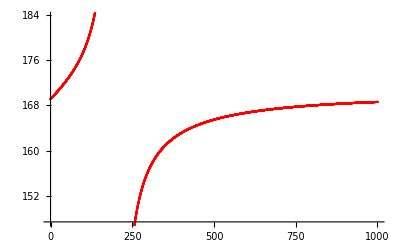

InterpolatingFunction::dmval: Input value {0.0204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

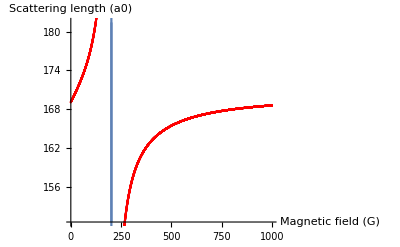

```mathematica
SetDirectory[NotebookDirectory[]]
scatDat = Import["K409halfs7halfsScatFromSimoni/as_MM_mn_8.txt","Table"];
scatInterpOfBTheory = Interpolation[scatDat]; (*For comparing data to best fit*)
datPlot = ListPlot[scatDat, PlotStyle -> Red]

Show[{Plot[scatInterpOfBTheory[B],{B,0,1000},AxesLabel -> {"Magnetic field (G)", "Scattering length (a0)"}],
Plot[scatInterpOfBTheory[B],{B,208,210},AxesLabel -> {"Magnetic field (G)", "Scattering length (a0)"}],
Plot[scatInterpOfBTheory[B],{B,201.3,202},AxesLabel -> {"Magnetic field (G)", "Scattering length (a0)"}],datPlot }]
```

Now we will find the location of the zero crossing and resonance, approximately, from the theory, so that we can shift the theory to match the zero crossing location to the experiment. 
	We assume the theory gets the overall shape right, but is just potentially slightly off on the actual location of the resonance. 

Chop the data to only contain stuff near the zero crossing, and fit

Then chop the data to only contain stuff near the resonance, and fit 1/a with a polynomial and find the zero of that.

-3710.68+74.2888 BB-0.557793 BB^2+0.00186162 BB^3-2.33021×10^-6 BB^4

-1.62736×10^8+3.09594×10^6 BB-22089.4 BB^2+70.0546 BB^3-0.0833233 BB^4

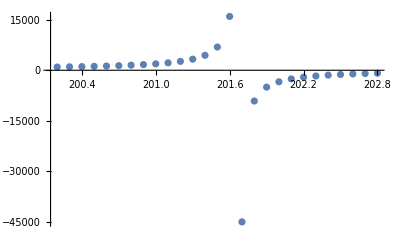
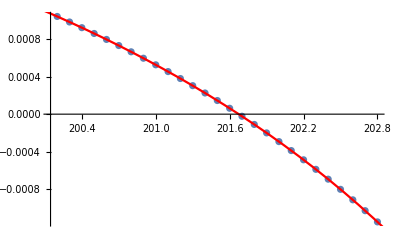
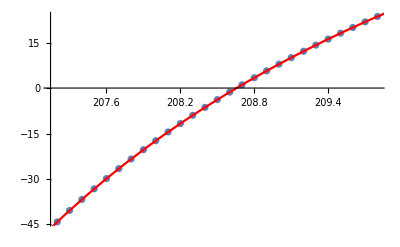

```mathematica
scatDatNearFeshbach = Take[scatDat, {1980,2050}];
scatDatNear0Cross = Take[scatDat, {2050,2120}];
scatDatNearFeshbach = Take[scatDat, {2002,2028}];
scatDatNear0Cross = Take[scatDat, {2072,2098}];
scatDatInverseNearFeshbach = Table[{scatDatNearFeshbach[[ii]][[1]],1/scatDatNearFeshbach[[ii]][[2]] }, {ii, 1, Length[scatDatNearFeshbach]}];
(*Now fit things to find the zero crossing and *)
fitscatDatInverseNearFeshbach = Fit[scatDatInverseNearFeshbach,{1,BB,BB^2, BB^3, BB^4}, BB ]
fitscatDatNear0Cross= Fit[scatDatNear0Cross,{1,BB,BB^2,BB^3, BB^4}, BB ]
{ListPlot[scatDatNearFeshbach, PlotRange -> All],
Show[{ListPlot[scatDatInverseNearFeshbach , PlotRange -> All], Plot[fitscatDatInverseNearFeshbach /. BB -> B,{B,198,204}, PlotStyle -> Red]}],
Show[{ListPlot[scatDatNear0Cross, PlotRange -> All], Plot[fitscatDatNear0Cross /. BB -> B,{B,204,212}, PlotStyle -> Red]}]}
```

```mathematica
zerosscatDatInverseNearFeshbach = NSolve[fitscatDatInverseNearFeshbach==0,BB]
zerosscatDatNear0Cross = NSolve[fitscatDatNear0Cross==0,BB]
```

{{BB→194.289},{BB→201.472-7.0435 ⅈ},{BB→201.472+7.0435 ⅈ},{BB→201.674}}

{{BB→208.442-6.62314 ⅈ},{BB→208.442+6.62314 ⅈ},{BB→208.656},{BB→215.217}}

```mathematica
B0FromTheory = (BB/. zerosscatDatInverseNearFeshbach[[4]])
BCrossFromTheory = (BB/. zerosscatDatNear0Cross[[3]])
ΔBFromTheory = BCrossFromTheory-B0FromTheory
```

201.674

208.656

6.98144

Now we will generate an interpolating function which has a nice form everywhere for the scattering length data. In particular, we will use the fact that 1/a is behaved nicely near the resonance to make a piecewise definition of the interpolating function that uses the fitted nice form near the resonance instead of the interpolating function for a.

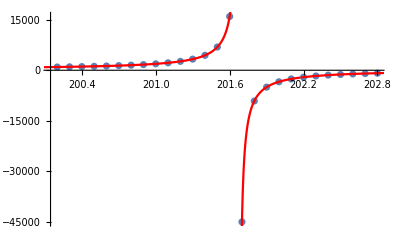

```mathematica
deltaBForPiecewiseFunctionDefinition = 0.5; (*fit for 1/a is very accurate everywhere near +/- 0.5 G of the resonance, see above. Don't want to get too close though *)
scatInterpOfBTheoryFinal[B_] := Piecewise[{
{scatInterpOfBTheory [B],B<  B0FromTheory- deltaBForPiecewiseFunctionDefinition},
{(1/fitscatDatInverseNearFeshbach /. BB -> B), (B ≥ B0FromTheory- deltaBForPiecewiseFunctionDefinition ) && (B ≤  B0FromTheory+ deltaBForPiecewiseFunctionDefinition) },
{scatInterpOfBTheory [B],B>  B0FromTheory+ deltaBForPiecewiseFunctionDefinition}
}]
Show[{ListPlot[scatDatNearFeshbach , PlotRange -> All], Plot[scatInterpOfBTheoryFinal[BB],{BB,198,204}, PlotStyle -> Red, PlotRange -> All]}]
```

```mathematica
scatInterpOfBTheoryFinal[BCrossFromTheory] (*Check that 0 of the scattering length matches the calibrated location, otherwise it won't when we shift the theory curve over by a bit. *)
```

0.00141242

```mathematica
(*Now, just for reference, find the fit value for the background scattering length by fitting the right formula*)
```

```mathematica
abgdat = Table[{abg,NIntegrate[(scatInterpOfBTheoryFinal[B]- abg*(1- (BCrossFromTheory-B0FromTheory)/(B-B0FromTheory)))^2,{B,B0FromTheory+0.1,BCrossFromTheory+6}]}, {abg,167.25,167.75,0.025}];
fitabg = Fit[abgdat,{1,abg, abg^2}, abg ]
bestGuessBackgroundScat= abg /.  NMinimize[fitabg,abg][[2]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in B near {B} = {201.8}. NIntegrate obtained 54.4987 and 0.00291879 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in B near {B} = {201.812}. NIntegrate obtained 47.1223 and 0.00233826 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in B near {B} = {201.811}. NIntegrate obtained 40.313 and 0.00213053 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

1.20419×10^7-143693. abg+428.664 abg^2

167.606

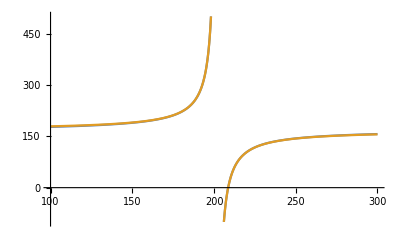

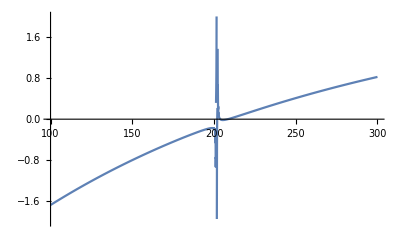

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in B near {B} = {201.806}. NIntegrate obtained 4.54623 and 0.000540949 for the integral and error estimates.

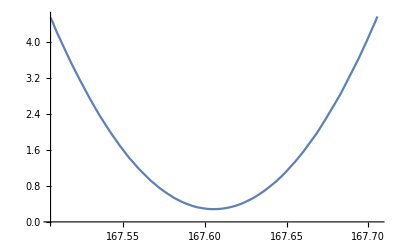

```mathematica
(*Plot a few things to make sure stuff is ok *)
Plot[{scatInterpOfBTheoryFinal[B], bestGuessBackgroundScat*(1- (BCrossFromTheory-B0FromTheory)/(B-B0FromTheory))}, {B,100,300}, PlotRange -> {-100,500}]
Plot[{scatInterpOfBTheoryFinal[B] -bestGuessBackgroundScat*(1- (BCrossFromTheory-B0FromTheory)/(B-B0FromTheory))}, {B,100,300}, PlotRange -> {-2,2}]
Plot[NIntegrate[(scatInterpOfBTheoryFinal[B]- abg*(1- (BCrossFromTheory-B0FromTheory)/(B-B0FromTheory)))^2,{B,B0FromTheory+0.1,BCrossFromTheory}], {abg,bestGuessBackgroundScat-0.1, bestGuessBackgroundScat+0.1}, PlotPoints -> 3]
```

#### Parameter Settings

```mathematica
SetDirectory[NotebookDirectory[]];
(*Experimental parameters*)
BCrossSetpointInCicero = 209.126; (*location of 0 crossing in Gauss, measured in Cicero*)

(*Low lattice depth parameters*)
ωPar = 25094*2π; (*Hz frequency calibrated, times 2 pi*)
ωPerpx = 96840*2π; 
ωPerpy = 96554*2π;  (*average 2 measurments of 2 omega*)
zeroInteractionsEnergyGap = 140.7615;  (*Hz*)

(*
(*Medium lattice depth parameters*)
ωPar= 38503*2π; (*Hz frequency calibrated, times 2 pi*)
ωPerpx = 149530*2π; 
ωPerpy = 150290*2π; 
zeroInteractionsEnergyGap = 138.3046;  (*Hz*)
*)

(*
(*Highest lattice depth parameters*)
ωPar= 51754*2π; (*Hz frequency calibrated, times 2 pi*)
ωPerpx = 198830*2π; 
ωPerpy = 198717*2π;  (*average 2 measurments of 2 omega*)
zeroInteractionsEnergyGap = 137.3784;  (*Hz*)
*)

bohrRadius = 5.29177211 10^-11;
mAtom=6.63617807 10^-26;
ℏ=1.054571817 10^-34;

(*All magnetic fields measured in the experiment were recorded in terms of a cicero setpoint, but the actual field was calibrated to be slightly different. This is that calibration*)
Bactual[Bset_]:= -103.93830843058895+2.5017420650577376 Bset-0.00721643766841785 Bset^2+0.000011530300269469465 Bset^3
BCross = Bactual[BCrossSetpointInCicero]; 
BTheoryCrossMinusBCross = BCrossFromTheory - BCross ;
(*Ie when Bactual is BCross, I should use B = BTheoryCross to get the right theory scattering length out. That is, any input to theory should be shifted by BTheoryCrossMinusBCross before being used to get a number calculated from theory*)
B0 =BCross- ΔBFromTheory;
(*
(* Old scattering length functions *)
B0= 202.1; (*1-2 Feshbach resonance*)
ΔB = BCross-B0;
a3D0= 169.67 5.29177211 10^-11;168.6724129 5.29177211 10^-11;  (*background *)
a3D[B_]:= (a3D0/lPar)(1-ΔB/(B-B0)); (*This is in SHO units*)
*)
a3D[Bactual_]:= bohrRadius/lPar scatInterpOfBTheoryFinal[Bactual+BTheoryCrossMinusBCross] (*Actual function used to set the scattering length in all calculations below. The value we input to the theory for a given real B field is shifted according to above reasoning. *)

(*Derived parameters*)
ηeff=N[(√(ωPerpx*ωPerpy))/ωPar] ;(*true trap ratio from measured harmonic frequencies etc*)
E0 =  1/2 + ηeff; (*ground state energy of relative wavefunction including parallel and perp ground state energies*)
zeroInteractionsEnergyGapSHOUnits =  zeroInteractionsEnergyGap /ωPar/(2π);
lPar=√(ℏ/(mAtom ωPar));


Print["Trap ratio is: ", ηeff]
Print["Zero crossing Field is: ", BCross]
Print["Feshbach resonance is at: ", B0]
Print["Delta B is: ", BCross-B0]
```

Trap ratio is: 3.85339

Zero crossing Field is: 209.094

Feshbach resonance is at: 202.113

Delta B is: 6.98144

Now for reference create a few sets of pairs of scattering length values and B field values for plotting things in the data.

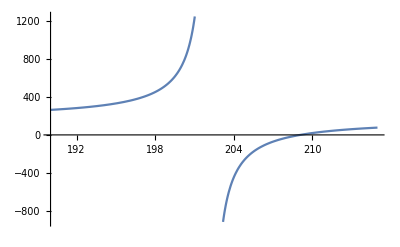

InterpolatingFunction::dmval: Input value {1989.56} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1159.11} lies outside the range of data in the interpolating function. Extrapolation will be used.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

InterpolatingFunction::dmval: Input value {1989.56} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

InterpolatingFunction::dmval: Input value {-1864.44} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-829.437} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1835.33} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{{200.707,1000},{201.994,10000},{202.101,100000},{202.113,-100000000},{202.124,-100000},{202.228,-10000},{203.115,-1000},{206.485,-100},{206.839,-80},{206.936,-75},{207.49,-50},{207.749,-40},{208.034,-30},{208.35,-20},{208.701,-10},{208.931,-4},{209.012,-2},{209.053,-1},{209.094,0},{209.136,1},{209.178,2},{209.265,4},{209.537,10},{210.039,20},{210.615,30},{211.281,40},{212.06,50},{214.741,75},{215.46,80},{219.394,100}}

a3DBpairs.txt

```mathematica
Plot[a3D[B]*lPar/bohrRadius, {B,190,215}]
(*Get B fields where certain a3D values show up*)
desireda3DValsBelow = {10^3,10^4,10^5};
desireda3DValsAbove= {-10^8,-10^5,-10^4,-10^3,-10^2,-80,-75,-50,-40, -30, -20, -10^1,-4,-2,-1,0,1,2,4,10^1,20,30,40,50,75, 80,10^2};
a3DBpairsBelow = Table[{B/.FindRoot[a3D[B]*lPar/bohrRadius==aaa, {B,180}],aaa},{aaa,desireda3DValsBelow }] (*give it a guess below resonance*);
a3DBpairsAbove = Table[{B/.FindRoot[a3D[B]*lPar/bohrRadius==aaa, {B,206}],aaa},{aaa,desireda3DValsAbove }](*give it a guess above resonance*);
a3DBpairs = Join[a3DBpairsBelow,a3DBpairsAbove]

Export["a3DBpairs.txt", a3DBpairs, "Table"]
```

#### Function Definitions

```mathematica
(*Lowest order interaction energy valid for small interactions*)
ApproxInteractionFreqGuess[B_]:= 
(4π ℏ^2)/mAtom(Abs[a3D[B]]*lPar)/(lPar * √(ℏ/(mAtom ωPerpx))√(ℏ/(mAtom ωPerpy)))1/(√(2π))^3 1/(2π ℏ)1/2
(*convert a3D back to SI, divide by SHO length for the 3 directions, divide by √π for the SHO wavefunction, and divide by √2 three times for the conversion of coordinates, then divide by 2 to get the expected frequency for beating between the two quantum states (not full U)*)

(*This approximate interaction strength roughly matches what is expected if we extrapolate down to 152.1 Gauss and reduce omega_z (from x lattice) and omega_z (from y lattice) to around 5 kHz from 18 kHz. 
The interaction energy of ground state atoms is 2 times what is listed here (since here is the beatnote between U and U/2). The scaling with omega_z is omega_z^3/2 because we have 3 powers of lPar in the denominator (a3D*lPar is some fixed length scale determined by the magnetic field).

When you take into account B -> 152.1 G instead of 208 G that changes a3D, and multiply by 2 for ground state U, and multiply by (omega_zlow/omega_zhigh)^3/2, then 703 Hz observed at 25 kHz omega_z at 208 G implies 1 kHz at 152.1 G at around 6 kHz omega_z which is what we measured a long time ago.
*)
```

```mathematica
(*Write down the g coupling values (defined as coefficients of terms in the Hamiltonian in SHO units of eneryg and length) as a function of the energy (in SHO units), following the conventions in the write up*)
g3DForIsotropic3DSHO[x_]:= π(Gamma[1/4-x/2]/Gamma[3/4-x/2])
g1DFor1DSHO[x_]:=-2(Gamma[3/4-x/2]/Gamma[1/4-x/2])
a3DForIntegernForAnisotropic3DSHO[yy_,n_] :=((Gamma[1/4 (1+2 n-2 yy)] (-1+2 n-2 yy-2 ∑_(m=1)^(-1+n) Hypergeometric2F1[1,1/2 (1/2+n-yy),1/2+1/2 (1/2+n-yy),ⅇ^((2 ⅈ m π)/n)]))/(2 √2 Gamma[1/4 (3+2 n-2 yy)]))^-1; (*From Idziasek paper exact for integral trap ratio*)
g3DForIntegernForAnisotropic3DSHO[x_,n_] :=√2 π a3DForIntegernForAnisotropic3DSHO[x,n] (*This definition follows from the g3D definition in terms of a3D for an isotropic 3D case*)
(*From Idziasek paper exact for nonintegral trap ratio*)
tMinIntegrationLimit=10^-5;
tMaxIntegrationLimit= 10^5;
ϵEn = 0.000001; (*Have to restrict the solving regions so that mathematica doesn't have errors *)
ridiculouslyLargeNegativeEnergy = -100000000000 ηeff; (*Use this to have a non-infinite value to set the molecular binding energy to when it is really -infinity.*)
FFforXAboveMinusEta[x_, η_]:= Piecewise[{{ NIntegrate[((η ⅇ^(-x t))/(√(1-ⅇ^-t)(1 - ⅇ^(-η t)))- t^(-3/2)), {t,tMinIntegrationLimit,tMaxIntegrationLimit}] , x≥ 0}
(*This works for x > 0 so integral converges. FOr x <0 there is a recursion relation using Gamma functions *),
{ NIntegrate[((η ⅇ^(-(x+η) t))/(√(1-ⅇ^-t)(1 - ⅇ^(-η t)))- t^(-3/2)), {t,tMinIntegrationLimit,tMaxIntegrationLimit}]+ η √π Gamma[x]/Gamma[x + 1/2] , -η ≤ x< 0}}]
a3DForNonIntegernForAnisotropic3DSHO[energy_, η_]:= -(√(2π))/FFforXAboveMinusEta[(-(energy - η - 1/2))/2, η] (*works for relative energy compared to bround state below 2 eta only*)

(*Convert these to normalized g values which have the same slope of energy vs. g_normed for the lowest state, again with conventions according to write up *)
gbar3DForIsotropic3DSHO[x_]:= g3DForIsotropic3DSHO[x]/(√π)^3
gbar1DFor1DSHO[x_]:=g1DFor1DSHO[x]/√π
gbar3DForIntegernForAnisotropic3DSHO[x_,n_]:=n g3DForIntegernForAnisotropic3DSHO[x,n]/(√π)^3
```

Now convert to real units of magnetic field, etc

```mathematica
(*This function finds the interaction setpoint leading to a certain energy. We will solve it (invert it) so we can find the energy for a given interaction setpoint*)(*Then we will find the interaction setpoint for a given b field, and plug that into the inverting function*)
(*We manually find the roots (the energy) for a given value of the scattering length,and we have to carefully choose the region of energy we look in for each scattering length if we want a certain state (like the 3rd state),since the mapping from scattering length to state energy is not single valued.For example see below*)

(*Now define the inverting function to get E vs interaction setpoint*)
	(*Have to do findroot with 1/function so that it doesn't have machine precision errors as much.*)
	(*Also have to do it carefully in different regions of a (when a is positive, need to search for energy in some region, and when negative, search for a in a different region*)
E1ForAlla[a_]:= Piecewise[{
{energy /. FindRoot[ a/a3DForNonIntegernForAnisotropic3DSHO[energy, ηeff]==1, {energy,E0 +ϵEn,E0 +2-ϵEn }],a>0},
{energy /. FindRoot[a/a3DForNonIntegernForAnisotropic3DSHO[energy, ηeff]==1, {energy,-1000, E0 -ϵEn }],a<0},
{E0,a==0}
}]
E2ForAlla[a_]:=Piecewise[{
{energy /. FindRoot[a/a3DForNonIntegernForAnisotropic3DSHO[energy, ηeff]==1, {energy,E0 +2+ϵEn,E0 +4-ϵEn }],a>0},
{energy /. FindRoot[a/a3DForNonIntegernForAnisotropic3DSHO[energy, ηeff]==1, {energy,E0 +ϵEn,E0 +2-ϵEn  }],a<0},
{E0+2,a==0}
}]
E3ForAlla[a_]:=Piecewise[{
{energy /. FindRoot[a/a3DForNonIntegernForAnisotropic3DSHO[energy, ηeff]==1, {energy,E0 +4+ϵEn,E0 +6-ϵEn  }],a>0},
{energy /. FindRoot[a/a3DForNonIntegernForAnisotropic3DSHO[energy, ηeff]==1, {energy,E0 +2+ϵEn,E0 +4-ϵEn  }],a<0},
{E0+4,a==0}
}]
EbForAlla[a_]:= Piecewise[{
{energy /. FindRoot[ a/a3DForNonIntegernForAnisotropic3DSHO[energy, ηeff]==1, {energy,-1000,E0-ϵEn }],a>0},
{ridiculouslyLargeNegativeEnergy,a<0},
{ridiculouslyLargeNegativeEnergy,a==0}
}]
(*Set it to some finite but ridiculously negative value so the plots don't take forever to evaluate*)

(*Now convert things to magnetic field dependence.Define state index (ie what we call it) depending on character at the 0 crossing around 209 Gauss*)
E1[B_] :=Piecewise[{
{EbForAlla[a3D[B]], B<= B0},
{E1ForAlla[a3D[B]], B> B0}
}]
E2[B_] :=Piecewise[{
{E1ForAlla[a3D[B]], B<= B0},
{E2ForAlla[a3D[B]], B> B0}
}]
E3[B_] :=Piecewise[{
{E2ForAlla[a3D[B]], B<= B0},
{E3ForAlla[a3D[B]], B> B0}
}]

(*Lastly define two states for avoided crossing near 209G between|0,2>and|2,0>.We know the splitting at the 0 crossing between the two states in Hz is recoilEHzPar.So in SHO units this is recoilEHzPar/(ωPar/2π).The two states involved are the 02 state (corresponding to E2) and the 20 state (corresponding to E1+2 energy)
Just use the usual avoided crossing formula*)
E0C2R[B_] := E2[B];
E2C0R[B_] := E1[B]+2;
EUpper[B_]:= (E0C2R[B]+E2C0R[B])/2+√(((E0C2R[B]-E2C0R[B])/2)^2+(zeroInteractionsEnergyGapSHOUnits/2)^2)
ELower[B_]:= (E0C2R[B]+E2C0R[B])/2-√(((E0C2R[B]-E2C0R[B])/2)^2+(zeroInteractionsEnergyGapSHOUnits/2)^2)
relativeDetuning[B_] := (E2C0R[B]-E0C2R[B])/zeroInteractionsEnergyGapSHOUnits;
```

Lastly define a few functions that are useful for plotting purposes.

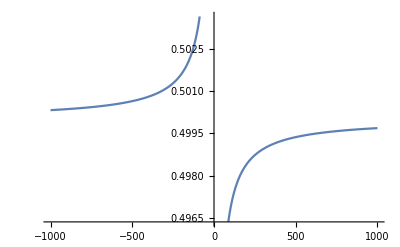

```mathematica
(*This is a function that takes an interaction strength setpoint (g1D from hamiltonian) and should rectify it to go from 0 to 1 as the interaction goes from 0 to +infinty/-infity and back to - and then back to 0. Purely for plotting purposes *)

ArcTanPositive[gbar_]:= Piecewise[{
{ArcTan[gbar]/π,gbar>0},
{(ArcTan[gbar]+π)/π ,gbar<0},{0,gbar==0}}]

Plot[ArcTanPositive[gbar], {gbar,-1000,1000}]
```

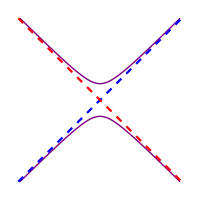

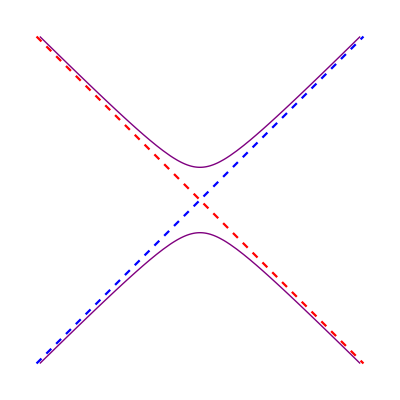

```mathematica
(*Define a function to interpolate colors between blue and red depending on the relative values of a gap and detuning in a wavefunction, for use in showing avoided crossings. *)
ham[Delta_, Omega_] := {{Delta/2, Omega/2},{Omega/2,-Delta/2}};
Eigensystem[ham[Delta, Omega]]/. Omega -> 1;
(*Put everything in units of Omega*)
lowerStateVec = Normalize[{Delta-√(1+Delta^2),1}];
upperStateVec = Normalize[{Delta+√(1+Delta^2),1}];
(*Define the color functions, that can now be replaced with any delta from -infinity to infinity*)
upperStateColor[zz_]:= Blend[{Blue, Red},lowerStateVec[[1]]^2 /. Delta-> zz]
lowerStateColor[zz_]:= Blend[{Red,Blue},lowerStateVec[[1]]^2 /. Delta -> zz]

pltMax = 5;
pltMin = -5;
aspectUse = 1;
(*Actual plots to demonstrate color functions*)
plotUpper = Plot[(√(1+Delta^2))/2, {Delta,pltMin,pltMax},ColorFunction ->{Function[{Delta}, upperStateColor[Delta]]},ColorFunctionScaling->False,  PlotStyle -> Thick, PlotRange -> {{pltMin, pltMax}, {pltMin/2, pltMax/2}}, Axes -> None, AspectRatio -> aspectUse];
plotLower = Plot[-(√(1+Delta^2))/2, {Delta,pltMin,pltMax},ColorFunction ->{Function[{Delta},lowerStateColor[Delta]]},ColorFunctionScaling->False,     PlotStyle -> Thick, PlotRange -> {{pltMin, pltMax}, {pltMin/2, pltMax/2}}, Axes -> None, AspectRatio -> aspectUse];
plotDashed = Plot[{ Delta/2, -Delta/2}, {Delta,pltMin,pltMax},PlotStyle -> {{Blue, Dashed}, {Red, Dashed}}, PlotRange -> {{pltMin, pltMax}, {pltMin/2, pltMax/2}}, Axes -> None, AspectRatio -> aspectUse];
Show[plotUpper,plotLower,plotDashed, ImageResolution -> 600, ImageSize -> 200]
Show[plotUpper,plotLower,plotDashed, ImageResolution -> 600, ImageSize -> 400]
```

#### Plots of theoretical energy vs normalized interaction comparing isotropic 3D, anisotropic 3D, and 1D situations

Now let' s plot things in these normalized units. Furthermore let’s subtract off the relevant ground state energy in each case so that we have everything starting from 0 energy at 0 interactions for the plot

Plot each energy (with ground state energy subtracted) vs the normalized interaction parameter gbar.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity+ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+«7»+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+«49» encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

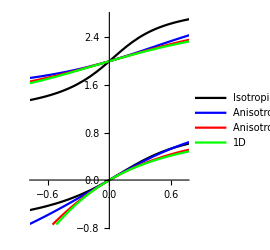

```mathematica
(*Not zoomed*)
gmin = -5;
gmax = 5;
Emin = -11; 
Emax = 24;
AspectToUse =2.0; 

(*zoomed on first two states*)
gmin = -0.75;
gmax =0.75;
Emin =-0.75; 
Emax = 2.75;
AspectToUse =1.25;

prmtrcplt1D=ParametricPlot[{gbar1DFor1DSHO[x],x-1/2},{x,Emin+1/2,Emax+1/2},PlotRange->{{gmin,gmax},{Emin,Emax}},PlotStyle -> {Green},PlotLegends -> {"1D"}] ;
prmtrcplt3DIso=ParametricPlot[{gbar3DForIsotropic3DSHO[x],x-3/2},{x,Emin+3/2,Emax+3/2},PlotRange->{{gmin,gmax},{Emin,Emax}},PlotStyle -> Black, PlotLegends -> {"Isotropic 3D"}];
ηtest = 4;
prmtrcplt3DAniso4=ParametricPlot[{gbar3DForIntegernForAnisotropic3DSHO[x,ηtest ] ,x-(1/2+ηtest)},{x,Emin+(1/2+ηtest),Emax+(1/2+ηtest)},PlotRange->{{gmin,gmax},{Emin,Emax}},PlotStyle -> Blue, PlotLegends -> {"Anisotropic 3D, η=4, exact"}];
ηtest = 100;
prmtrcplt3DAniso100=ParametricPlot[{gbar3DForIntegernForAnisotropic3DSHO[x,ηtest ] ,x-(1/2+ηtest)},{x,Emin+(1/2+ηtest),Emax+(1/2+ηtest)},PlotRange->{{gmin,gmax},{Emin,Emax}},PlotStyle -> Red, PlotLegends -> {"Anisotropic 3D, η=100, exact"}];
figInteractionTheoryPlot = Show[prmtrcplt3DIso,prmtrcplt3DAniso4,prmtrcplt3DAniso100,prmtrcplt1D, ImageSize-> 200, TicksStyle ->Medium, AspectRatio ->AspectToUse ]

(*Export["figInteractionTheoryPlot.pdf",figInteractionTheoryPlot, ImageResolution -> 2000]*)
```

#### Examine CIR physics and location of relative wavefunction node in anisotropic 3D SHO

Explore where the exited COM state (2x excited) crosses the lowest repulsive state near strong positive interactions. 
	Looking for crossings near E0

```mathematica
(*Do a sweep to even more anisotropic to see the limit*)
ηTab= Table[ηtest,{ηtest, 2,200,4}];
ϵEnVal = 0.00000000001;
whereE2Equals1SHOHigherThanGroundState = Table[{ηtest,Re[N[a3DForIntegernForAnisotropic3DSHO[1/2+ηtest+1.0+ϵEnVal ,ηtest]]]}, {ηtest,ηTab}];
whereCOMExcitedMoleculeEquals1SHOHigherThanGroundState = Table[{ηtest,Re[N[a3DForIntegernForAnisotropic3DSHO[1/2+ηtest+1.0+ϵEnVal  - 2ηtest,ηtest]]]}, {ηtest,ηTab}];
Print["If this quantity is zero, COM excited state always crosses first state at the same spot the first state gains 1 SHO energy, regardless of η: ", Total[whereCOMExcitedMoleculeEquals1SHOHigherThanGroundState- whereE2Equals1SHOHigherThanGroundState ]];
whereCOMExcitedMoleculeEqualsGroundState = Table[{ηtest,Re[N[a3DForIntegernForAnisotropic3DSHO[1/2+ηtest+ ϵEnVal - 2ηtest,ηtest]]]}, {ηtest,ηTab}];
CIRResonanceScatteringLength=Table[{ηtest,(√2)/1.4603 1/(√ηtest)}, {ηtest,ηTab}];

ListLogLogPlot[{whereE2Equals1SHOHigherThanGroundState , whereCOMExcitedMoleculeEqualsGroundState,CIRResonanceScatteringLength} , Joined -> True,Mesh -> True, PlotRange -> All, PlotLabels ->{"E2=+1","EM=-2η","CIR location"}, AxesLabel -> {"η of trap", "Scattering length (SHO units)"}, ImageSize -> Large]

(*Now check out what E2 is doing when the excited molecule hits the ground state energy, solve for energy where aScat is the a found for that crossing*)
E2MinusGroundStatewhereCOMExcitedMoleculeEqualsGroundState = Table[
{ηtest,
(energy /. FindRoot[1 == Re[N[a3DForIntegernForAnisotropic3DSHO[1/2+ηtest+ ϵEnVal - 2ηtest,ηtest]]]/a3DForIntegernForAnisotropic3DSHO[energy, ηtest], {energy,(ηtest + 1/2) +0.99}])-(1/2+ηtest)}, 
{ηtest,ηTab}];
E2MinusGroundStateAtCIRFormula= Table[
{ηtest,
(energy /. FindRoot[1 ==((√2)/Abs[N[Zeta[1/2,1.0]]] 1/(√ηtest))/a3DForIntegernForAnisotropic3DSHO[energy, ηtest], {energy,(ηtest + 1/2) +0.99}])-(1/2+ηtest)}, 
{ηtest,ηTab}];

ListLogLogPlot[{E2MinusGroundStatewhereCOMExcitedMoleculeEqualsGroundState,E2MinusGroundStateAtCIRFormula} , Joined -> True,Mesh -> True, PlotRange -> All, PlotLabels ->{"E2-ground state energy, at scat length where molecule crosses ground state energy","E2-ground state energy, at scat length for CIR"}, AxesLabel -> {"η of trap", "Energy (SHO units)"}, ImageSize -> Large]
```

If this quantity is zero, COM excited state always crosses first state at the same spot the first state gains 1 SHO energy, regardless of η: {0,-6.24525×10^-10}

-Graphics-

-Graphics-

One should expect that the CIR scattering length associated with the transverse direction converges to the location that the wavefunction in the z direction develops a node, since this is also where the effective 1D scattering length is infinite (wavepackets in z would be reflected). Even if you don’t have a truly 1D system without confinement in the z direction (ie a waveguide), if all of the basis wavefunctions of your system have this form (where the even functions are identical to the absolute value of the odd wavefunctions) then all wavefunctions will end up being reflected, no matter what. 

What seems to be odd is that the location of the node of the z wavefunction doesn’t seem to converge to the location CIR very quickly (although it may in the end), and the node seems to not occur when the energy is 1 parallel SHO higher, as one would expect it to do in 1D. 


CAUTION - I don’t think this wavefunction is normalized correctly? It seems to fail for some energy values.

```mathematica
(*Lets examine the relative wavefunctions, from Eq. 13 of Idziasek paper*) psiRel[z_,ρ_, ηtest_, ϵ_, Nmax_] :=1/(2^ηtest(*Trying to normalize*)) (ηtest ⅇ^(-ηtest ρ^2/2))/(2 π^(3/2)2^(ϵ/2))Sum[ 2^(ηtest m)Gamma[(2 ηtest m - ϵ)/2]LaguerreL[m,ηtest ρ^2]ParabolicCylinderD[ϵ-2ηtest m, Abs[z] √2], {m,0,Nmax}]
NmaxUsedForRelWavefunction= 10;

busch3DIsotropicSol[r_, ν_]:= 1/2 π^(-3/2)Exp[-r^2/2]Gamma[-ν]Re[HypergeometricU[-ν,3/2,r^2]] (* THis is the Busch formula, but without the gamma function. ν is related to the energy E = 2 ν + 3/2*)
```

First take a look at the 3D Isotropic solutions a bit

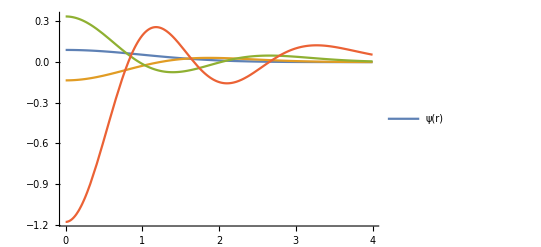

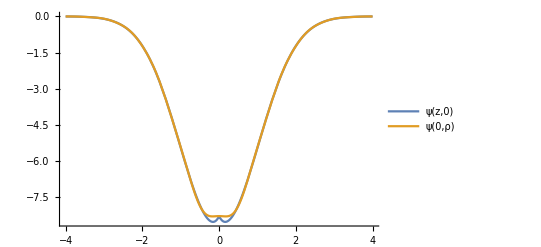

```mathematica
(*Busch first 4 states, unnormalized*)
Plot[{busch3DIsotropicSol[Abs[r] , 0.00000],
busch3DIsotropicSol[Abs[r],1.0],
busch3DIsotropicSol[Abs[r],2.0],
busch3DIsotropicSol[Abs[r],3.0]
},{r,0.0001,4}, PlotLegends -> {"ψ(r)"}, PlotRange -> All] 

(*Idziasek first state for isotropci solution*)
ηTest =1;
Etest = (ηTest + 1/2)+0.01; (*really close to the effective CIR point in terms of energy*)
Plot[{psiRel[x,0.0,ηTest, Etest-(ηTest + 1/2), NmaxUsedForRelWavefunction],psiRel[0.0,x, ηTest, Etest-(ηTest + 1/2),NmaxUsedForRelWavefunction]},{x,-4,4}, PlotLegends -> {"ψ(z,0)","ψ(0,ρ)"}, PlotRange -> All]
```

0.211889

21188.9

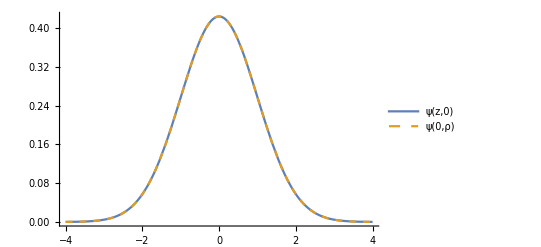

```mathematica
ηTest =1;
Etest = (ηTest + 1/2)+0.00001; (*really close to the effective CIR point in terms of energy*)
buschNormalizationFactor = √NIntegrate[busch3DIsotropicSol[Abs[x] , 0.00000]^2 4π x^2,{x,0,100}]
idziasekNormalizationFactor = √NIntegrate[(psiRel[x,0.0,ηTest, Etest-(ηTest + 1/2), NmaxUsedForRelWavefunction])^2 4π x^2,{x,0,100}]

Plot[{(-psiRel[x,0.0,ηTest, Etest-(ηTest + 1/2), NmaxUsedForRelWavefunction])/idziasekNormalizationFactor,busch3DIsotropicSol[Abs[x] , 0.00000]/buschNormalizationFactor},{x,-4,4}, PlotLegends -> {"ψ(z,0)","ψ(0,ρ)"}, PlotRange -> All, PlotStyle -> {Automatic, Dashed}] 
(*This shows the two solutions are identical for low energies.*)
```

4.25713

2.14466

2.13439

2.13074

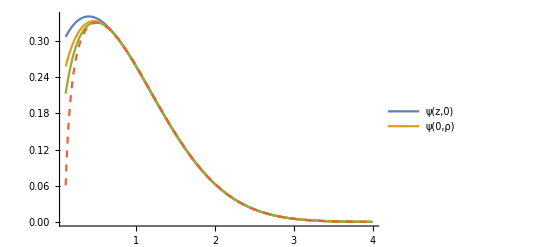

```mathematica
(*Check equality of solutions at finite displacement from 0 energy. Careful the units of Busch and Idziasek are not the same. the ν definition for Busch is such that energy is scaled by 2x that. *)
(*I think the Idziasek solutions are sensitive to the summation number in the series, so have to be careful about that too. *)
ηTest =1;
EoffsetReal = 0.1;
Etest = (ηTest + 1/2)+EoffsetReal; (*really close to the effective CIR point in terms of energy*)
EOffsetBusch =EoffsetReal/2;
buschNormalizationFactor = √NIntegrate[busch3DIsotropicSol[Abs[x] , EOffsetBusch]^2 4π x^2,{x,0,100}]
idziasekNormalizationFactor4 = √NIntegrate[(psiRel[x,0.0,ηTest, Etest-(ηTest + 1/2), 4])^2 4π x^2,{x,0,100}]
idziasekNormalizationFactor10 = √NIntegrate[(psiRel[x,0.0,ηTest, Etest-(ηTest + 1/2), 10])^2 4π x^2,{x,0,100}]
idziasekNormalizationFactor20 = √NIntegrate[(psiRel[x,0.0,ηTest, Etest-(ηTest + 1/2), 20])^2 4π x^2,{x,0,100}]

Plot[{(-psiRel[x,0.0,ηTest, Etest-(ηTest + 1/2), 4])/idziasekNormalizationFactor4,(-psiRel[x,0.0,ηTest, Etest-(ηTest + 1/2), 10])/idziasekNormalizationFactor10,(-psiRel[x,0.0,ηTest, Etest-(ηTest + 1/2), 20])/idziasekNormalizationFactor20,(-busch3DIsotropicSol[Abs[x] , EOffsetBusch])/buschNormalizationFactor},{x,0.1,4}, PlotLegends -> {"ψ(z,0)","ψ(0,ρ)"}, PlotRange -> All, PlotStyle -> {Automatic,Automatic, Automatic, Dashed}] 
(*This shows the two solutions are identical for low energies.*)
```

Yeah it looks like the summation order of the Idziasek solution matters a ton for correctly reproducing the behavior near 0, but not much for away from 0 stuff. 
Also looks like the wavefunction of the 3D isotropic trap more or less immediately gets a node as soon as you turn on interactions? or at least immediately reverses sign at the origin.

And let' s take a look at things at finite anisotropy, and see how the solution depends on the summation order in the Idziasek solution. 
	It looks like it does depend on it up to a decent order of summation, but then eventually it stabilizes, even for the node at r=0. We explore this more below.

General::munfl: 1.81339×10^-46 2.14402×10^-266 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.13337×10^-47 3.81729×10^-275 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 7.08357×10^-49 6.13367×10^-284 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

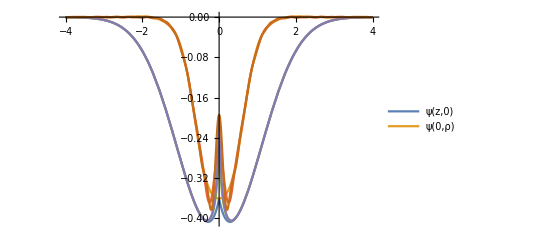

```mathematica
ηTest =4;
Etest = (ηTest + 1/2)+0.1; (*really close to the effective CIR point in terms of energy*)
Plot[{psiRel[x,0.0,ηTest, Etest-(ηTest + 1/2),4],psiRel[0.0,x, ηTest, Etest-(ηTest + 1/2),4],
psiRel[x,0.0,ηTest, Etest-(ηTest + 1/2),20],psiRel[0.0,x, ηTest, Etest-(ηTest + 1/2),20],
psiRel[x,0.0,ηTest, Etest-(ηTest + 1/2),40],psiRel[0.0,x, ηTest, Etest-(ηTest + 1/2),40]},{x,-4,4}, PlotLegends -> {"ψ(z,0)","ψ(0,ρ)"}, PlotRange -> All]
```

Note that the ground state wavefunction at roughly 0 interactions in the anisotropic trap has less extent in the perpendicular direction than in the parallel direction, by √η, as one would expect. 

Now let’s look numerically for the location of the node in various geometries. Unfortuantely, this seems to depend on the number of terms one retains in the formula for the wavefunction (which should in principle be infinite)

50

Energy relative to ground state energy: 0.128

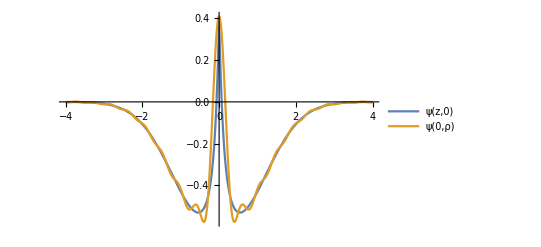

```mathematica
NmaxUsedForRelWavefunction = 50

ηTest =1;
Etest = ηTest + 1/2+0.128;
Print["Energy relative to ground state energy: ",Etest - (1/2 + ηTest)]
Plot[{psiRel[x,0.0,ηTest, Etest-(ηTest + 1/2), NmaxUsedForRelWavefunction],psiRel[0.0,x, ηTest, Etest-(ηTest + 1/2),NmaxUsedForRelWavefunction]},{x,-4,4}, PlotLegends -> {"ψ(z,0)","ψ(0,ρ)"}, PlotRange -> All]
```

Check out what happens near a scattering length of 0.05 for various trap ratios.

30

8.82073

Energy relative to ground state energy: 0.320728

General::munfl: 1.95756×10^-46 3.73244×10^-266 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 7.64672×10^-49 1.07385×10^-283 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.987×10^-51 2.06982×10^-301 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

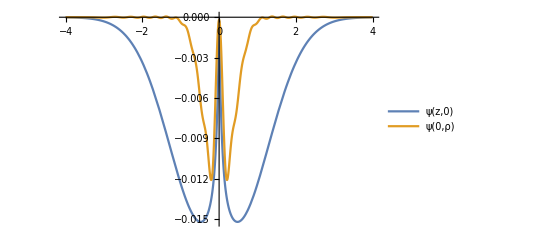

4.67473

Energy relative to ground state energy: 0.174726

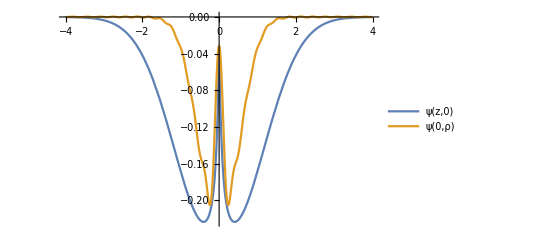

```mathematica
NmaxUsedForRelWavefunction = 30

ηTest =8;
aScatTest = 0.056;
Etest =Re[ (energy /. FindRoot[1 ==(aScatTest)/a3DForIntegernForAnisotropic3DSHO[energy, ηTest], {energy,(ηTest + 1/2) +0.99}])]
Print["Energy relative to ground state energy: ",Etest - (1/2 + ηTest)]
Plot[{psiRel[x,0.0,ηTest, Etest-(ηTest + 1/2), NmaxUsedForRelWavefunction],psiRel[0.0,x, ηTest, Etest-(ηTest + 1/2),NmaxUsedForRelWavefunction]},{x,-4,4}, PlotLegends -> {"ψ(z,0)","ψ(0,ρ)"}, PlotRange -> All] 

ηTest =4;
aScatTest = 0.056;
Etest =Re[ (energy /. FindRoot[1 ==(aScatTest)/a3DForIntegernForAnisotropic3DSHO[energy, ηTest], {energy,(ηTest + 1/2) +0.99}])]
Print["Energy relative to ground state energy: ",Etest - (1/2 + ηTest)]
Plot[{psiRel[x,0.0,ηTest, Etest-(ηTest + 1/2), NmaxUsedForRelWavefunction],psiRel[0.0,x, ηTest, Etest-(ηTest + 1/2),NmaxUsedForRelWavefunction]},{x,-4,4}, PlotLegends -> {"ψ(z,0)","ψ(0,ρ)"}, PlotRange -> All]
```

For a few values of Eta, let’s find the energy relative to the ground state where the node exists.

```mathematica
Plot[{psiRel[0.0,0.0,ηTest, Etest-(ηTest + 1/2), NmaxUsedForRelWavefunction],psiRel[0.0,x, ηTest, Etest-(ηTest + 1/2),NmaxUsedForRelWavefunction]},{x,-4,4}, PlotLegends -> {"ψ(z,0)","ψ(0,ρ)"}, PlotRange -> All]
```

General::munfl: 3.546×10^-46 2.75858×10^-264 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.773×10^-46 1.82106×10^-266 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 8.865×10^-47 1.19427×10^-268 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 3.546×10^-46 2.75858×10^-264 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.773×10^-46 1.82106×10^-266 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 8.865×10^-47 1.19427×10^-268 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

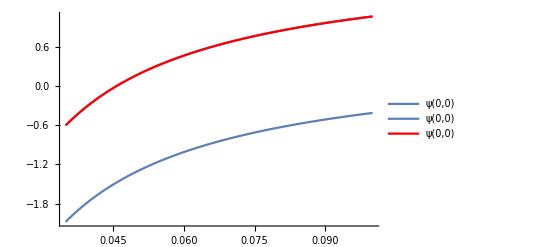

```mathematica
pltTab = {};
ηTest = 1; 
epltmin = 0.035;
epltmax= 0.1;

NmaxUsedForRelWavefunction = 10;
AppendTo[pltTab,Plot[{psiRel[0,0, ηTest, Eextra, NmaxUsedForRelWavefunction]},{Eextra,epltmin,epltmax}, PlotLegends -> {"ψ(0,0)"}, PlotRange -> All] ];
NmaxUsedForRelWavefunction = 200;
AppendTo[pltTab,Plot[{psiRel[0,0, ηTest, Eextra, NmaxUsedForRelWavefunction]},{Eextra,epltmin,epltmax}, PlotLegends -> {"ψ(0,0)"}, PlotRange -> All] ];
NmaxUsedForRelWavefunction = 500;
AppendTo[pltTab,Plot[{psiRel[0,0, ηTest, Eextra, NmaxUsedForRelWavefunction]},{Eextra,epltmin,epltmax}, PlotLegends -> {"ψ(0,0)"}, PlotRange -> All, PlotStyle -> Red] ];

Show[pltTab]
```

General::munfl: 1.8134×10^-46 2.14404×10^-266 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.13337×10^-47 3.81733×10^-275 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 7.08358×10^-49 6.13374×10^-284 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 1.8134×10^-46 2.14404×10^-266 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.13337×10^-47 3.81733×10^-275 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 7.08358×10^-49 6.13374×10^-284 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

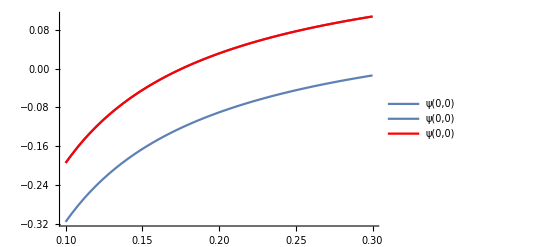

```mathematica
pltTab = {};
ηTest = 4; 
epltmin = 0.1;
epltmax= 0.3;

NmaxUsedForRelWavefunction = 10;
AppendTo[pltTab,Plot[{psiRel[0,0, ηTest, Eextra, NmaxUsedForRelWavefunction]},{Eextra,epltmin,epltmax}, PlotLegends -> {"ψ(0,0)"}, PlotRange -> All] ];
NmaxUsedForRelWavefunction = 100;
AppendTo[pltTab,Plot[{psiRel[0,0, ηTest, Eextra, NmaxUsedForRelWavefunction]},{Eextra,epltmin,epltmax}, PlotLegends -> {"ψ(0,0)"}, PlotRange -> All] ];
NmaxUsedForRelWavefunction = 200;
AppendTo[pltTab,Plot[{psiRel[0,0, ηTest, Eextra, NmaxUsedForRelWavefunction]},{Eextra,epltmin,epltmax}, PlotLegends -> {"ψ(0,0)"}, PlotRange -> All, PlotStyle -> Red] ];

Show[pltTab]
```

General::munfl: 8.1369×10^-49 1.69226×10^-283 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-733.059] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-816.471] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 8.1369×10^-49 1.69226×10^-283 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-733.059] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-816.471] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 8.1369×10^-49 1.69226×10^-283 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-733.059] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-816.471] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

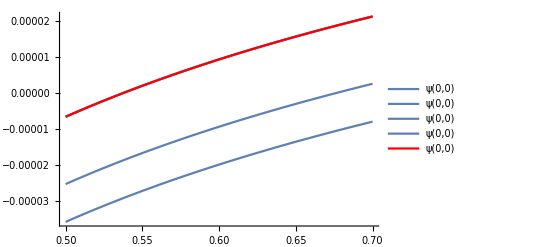

```mathematica
pltTab = {};
ηTest = 16; 
epltmin = 0.5;
epltmax= 0.7;

NmaxUsedForRelWavefunction = 2;
AppendTo[pltTab,Plot[{psiRel[0,0, ηTest, Eextra, NmaxUsedForRelWavefunction]},{Eextra,epltmin,epltmax}, PlotLegends -> {"ψ(0,0)"}, PlotRange -> All] ];
NmaxUsedForRelWavefunction = 4;
AppendTo[pltTab,Plot[{psiRel[0,0, ηTest, Eextra, NmaxUsedForRelWavefunction]},{Eextra,epltmin,epltmax}, PlotLegends -> {"ψ(0,0)"}, PlotRange -> All] ];
NmaxUsedForRelWavefunction = 30;
AppendTo[pltTab,Plot[{psiRel[0,0, ηTest, Eextra, NmaxUsedForRelWavefunction]},{Eextra,epltmin,epltmax}, PlotLegends -> {"ψ(0,0)"}, PlotRange -> All] ];
NmaxUsedForRelWavefunction = 60;
AppendTo[pltTab,Plot[{psiRel[0,0, ηTest, Eextra, NmaxUsedForRelWavefunction]},{Eextra,epltmin,epltmax}, PlotLegends -> {"ψ(0,0)"}, PlotRange -> All] ];
NmaxUsedForRelWavefunction =100;
AppendTo[pltTab,Plot[{psiRel[0,0, ηTest, Eextra, NmaxUsedForRelWavefunction]},{Eextra,epltmin,epltmax}, PlotLegends -> {"ψ(0,0)"}, PlotRange -> All, PlotStyle -> Red] ];

Show[pltTab]
```

General::munfl: 8.13691×10^-49 1.69228×10^-283 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-816.471] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-987.202] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 8.13691×10^-49 1.69228×10^-283 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-816.471] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-987.202] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 8.13691×10^-49 1.69228×10^-283 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-816.471] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-987.202] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

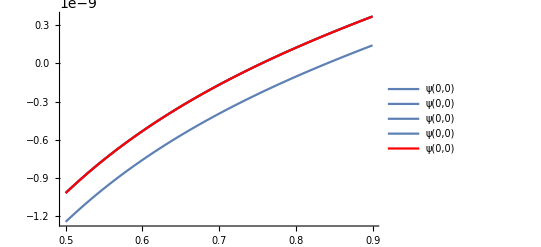

```mathematica
pltTab = {};
ηTest = 32; 
epltmin = 0.5;
epltmax= 0.9;

NmaxUsedForRelWavefunction = 2;
AppendTo[pltTab,Plot[{psiRel[0,0, ηTest, Eextra, NmaxUsedForRelWavefunction]},{Eextra,epltmin,epltmax}, PlotLegends -> {"ψ(0,0)"}, PlotRange -> All] ];
NmaxUsedForRelWavefunction = 4;
AppendTo[pltTab,Plot[{psiRel[0,0, ηTest, Eextra, NmaxUsedForRelWavefunction]},{Eextra,epltmin,epltmax}, PlotLegends -> {"ψ(0,0)"}, PlotRange -> All] ];
NmaxUsedForRelWavefunction = 30;
AppendTo[pltTab,Plot[{psiRel[0,0, ηTest, Eextra, NmaxUsedForRelWavefunction]},{Eextra,epltmin,epltmax}, PlotLegends -> {"ψ(0,0)"}, PlotRange -> All] ];
NmaxUsedForRelWavefunction = 60;
AppendTo[pltTab,Plot[{psiRel[0,0, ηTest, Eextra, NmaxUsedForRelWavefunction]},{Eextra,epltmin,epltmax}, PlotLegends -> {"ψ(0,0)"}, PlotRange -> All] ];
NmaxUsedForRelWavefunction =100;
AppendTo[pltTab,Plot[{psiRel[0,0, ηTest, Eextra, NmaxUsedForRelWavefunction]},{Eextra,epltmin,epltmax}, PlotLegends -> {"ψ(0,0)"}, PlotRange -> All, PlotStyle -> Red] ];

Show[pltTab]
```

General::munfl: Exp[-815.551] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1161.56] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1523.76] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-815.551] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1161.56] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1523.76] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

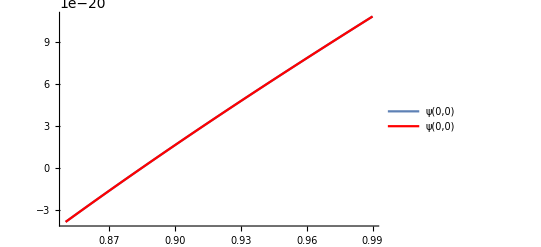

```mathematica
pltTab = {};
ηTest = 64; 
epltmin = 0.85;
epltmax= 0.99;


NmaxUsedForRelWavefunction = 60;
AppendTo[pltTab,Plot[{psiRel[0,0, ηTest, Eextra, NmaxUsedForRelWavefunction]},{Eextra,epltmin,epltmax}, PlotLegends -> {"ψ(0,0)"}, PlotRange -> All] ];
NmaxUsedForRelWavefunction =100;
AppendTo[pltTab,Plot[{psiRel[0,0, ηTest, Eextra, NmaxUsedForRelWavefunction]},{Eextra,epltmin,epltmax}, PlotLegends -> {"ψ(0,0)"}, PlotRange -> All, PlotStyle -> Red] ];

Show[pltTab]
```

General::munfl: Exp[-1161.56] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1898.86] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2679.72] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1161.56] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1898.86] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2679.72] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

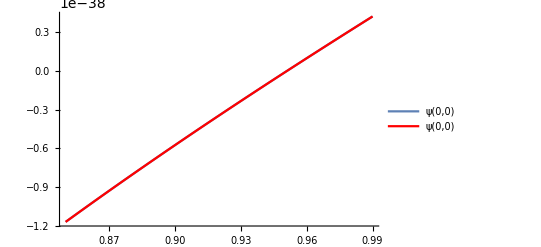

```mathematica
pltTab = {};
ηTest = 128; 
epltmin = 0.85;
epltmax= 0.99;


NmaxUsedForRelWavefunction = 100;
AppendTo[pltTab,Plot[{psiRel[0,0, ηTest, Eextra, NmaxUsedForRelWavefunction]},{Eextra,epltmin,epltmax}, PlotLegends -> {"ψ(0,0)"}, PlotRange -> All] ];
NmaxUsedForRelWavefunction =400;
AppendTo[pltTab,Plot[{psiRel[0,0, ηTest, Eextra, NmaxUsedForRelWavefunction]},{Eextra,epltmin,epltmax}, PlotLegends -> {"ψ(0,0)"}, PlotRange -> All, PlotStyle -> Red] ];

Show[pltTab]
```

It seems very roughly like the location of the node goes close to 1 SHO extra energy at a rate like 1 - 1/Log[η]. In particular, every time eta is doubled, the distance remaining to 1 seems to go down by a factor of 2, roughly, which suggests a log base2 scaling.

```mathematica
(*Look at things in terms of the energy, then in terms of the scattering length*)
approxNodeLocsRelativeEnergy = {{4,0.175}, {16,0.54}, {32,0.75}, {64, 0.885}, {128, 0.9525}};
pltApproxValues = ListPlot[approxNodeLocsRelativeEnergy, PlotRange ->{{3,140}, {0,1}}, ScalingFunctions -> { "Log",Automatic}, PlotStyle -> Red, PlotLabels -> "Approx energy found where node occurs"];
pltGuessFunc = Plot[{1 - 8/x}, {x,4,130},  PlotRange ->{{3,140}, {0,1}}, ScalingFunctions -> { "Log",Automatic}, PlotLabels -> "Approx formula for energy of node"];
pltE2MinusGroundStatewhereCOMExcitedMoleculeEqualsGroundState  = ListPlot[{E2MinusGroundStatewhereCOMExcitedMoleculeEqualsGroundState,E2MinusGroundStateAtCIRFormula}, PlotRange ->{{3,140}, {0,1}}, Joined -> True,Mesh -> True, ScalingFunctions -> { "Log",Automatic}, PlotStyle ->{Green, Orange} , PlotLabels ->{"Energy where excited molecule equals non-int ground state","Energy at CIR formula for aScat"}];
Show[{pltGuessFunc,pltApproxValues,pltE2MinusGroundStatewhereCOMExcitedMoleculeEqualsGroundState},AxesLabel -> {"η of trap", "Energy (SHO units)"}, ImageSize -> Large]

(*Now in terms of scattering length*)
(*Now in terms of scattering length*)
approxNodeLocsScatLength = Table[{approxNodeLocsRelativeEnergy[[tabInd]][[1]],
Re[N[a3DForIntegernForAnisotropic3DSHO[1/2+approxNodeLocsRelativeEnergy[[tabInd]][[1]]+approxNodeLocsRelativeEnergy[[tabInd]][[2]],approxNodeLocsRelativeEnergy[[tabInd]][[1]]]]]
}, {tabInd,1,5}]
ListLogLogPlot[{whereE2Equals1SHOHigherThanGroundState , whereCOMExcitedMoleculeEqualsGroundState,CIRResonanceScatteringLength,approxNodeLocsScatLength} , Joined -> True,Mesh -> True, PlotRange -> All, PlotLabels ->{"E2=+1","EM=-2η","CIR location", "Wavefunction node location"}, AxesLabel -> {"η of trap", "Scattering length (SHO units)"}, ImageSize -> Large]
```

-Graphics-

{{4,0.0560906},{16,0.0579105},{32,0.0580456},{64,0.056011},{128,0.0516224}}

-Graphics-

So, it looks like the location of the wavefunction node eventually converges to the CIR formula resonance location, but honestly not all that fast.

Summary : 
 	Energies:
 		The excited molecular wavefunction in the COM direction (with 2 η higher energy than the ground state molecule) crosses the interacting repulsive 0th harmonic oscillator state at EXACTLY the moment when that state has 1 ℏω energy injected out of the 2ℏω interpolation.
 		This location converges to the location of the CIR, and converges to the location where the molecule crosses the absolute non-interacting ground state energy, but it is not exactly the same thing 
 	Scattering resonances:
 		The r=0 part of the wavefunction in a 3D isotropic trap seems to go negative essentially the tiniest amount of interactions you add. 
 		If you trap is isotropic, then you have to add more interactions to drive the node down below 0. 
 			The resulting energy where the node appears goes like (1/2+ η) + 1 - 8/η roughly, which converges to +1 SHO energy, which is the same energy that the CIR converges to.
 			However, it looks very conclusively like this is a lower energy compared to the CIR energy
 		In the 1D limit, the scattering length and energy at which the node happens is the CIR, and +1 SHO energy along the shallow direction compared to the ground state.
 			This is exactly what one should expect for a scattering resonance (when the node appears, that is the “infinite effective interactions” moment).

#### Plot Injecting 2 ℏω of normalized energies across an interaction resonance in a purely 1D system

We have the function gbar1DFor1DSHO[x] which gives the interaction corresponding to the energy x (real energy, but only the relative part) in 1D. 

We want to plot as the x axis the interaction energy, where 0 is 0, and 0.5 is +infinity, 0.51 is -infinity, and 1 is 0 again, and 1.1 is slightly positive. 
We want it to be roughly linear in the interaction strength at low strengths, then nonlinear near infinity? Could use something like Arctan(gbar)/pi? Yes this function works well.

Now make a plot where the avoided crossing is included in the actual plot too (schematically)

```mathematica
(*This function generates a parametric plot of the energy vs. normed interaction value using the ArcTanPositive function *)

globalEnergyOffset = 0.5 ; (*to add in background ground state COM energy too *)
epsPlot = 0.000000000001;

plotSpecificState0toInfAndBack[emin_, emax_, EplotOffset_,interactionsplotOffset_, gminplt_,gmaxplt_,Eminplt_,Emaxplt_,color_]:= ParametricPlot[{ArcTanPositive[gbar1DFor1DSHO[x]]+interactionsplotOffset,x+EplotOffset+globalEnergyOffset},{x,emin+epsPlot,emax-epsPlot},PlotRange->{{gminplt,gmaxplt},{Eminplt,Emaxplt}},PlotStyle -> {color}]
(*
emin and emax are the range of real physical energies to calculate between. These are in units of relative energy for a single 1D SHO. 
	Ex. 1/2+ a little bit  will find a positive interaction energy corresponding to the slightly upward shifted ground state energy at positive interactions
		5/2 + a little bit will find the 2nd excited state at slightly positive interactions
		3/2 will find the ground state at infinite interactions (shifted up). Remember this doesn't find any energies that correspond to the asymmetric wavefunctions (original energy 3/2 for the 1st harmonic excited state, for example, doesnt disperse with interactions).  

EplotOffset is used to shift the energy plotted (ie shift the data) up or down everywhere. This is to be able to plot the energies of COM excited states which are simply shifted up relative to the lowest state. 
interactionsplotOffset lets us shift the data relative to the x axis left or right by some amount. 
gminplt_,gmaxplt_,Eminplt_,Emaxplt_ set the plot size, that's all. 
*)
```

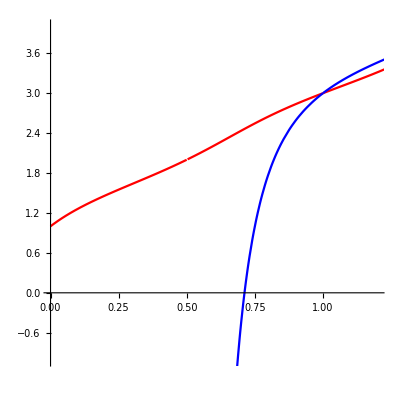

InterpolatingFunction[…]

InterpolatingFunction[…]

Plot::plln: Limiting value gmin in {g,gmin,1.9} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[{Plot[{redblueUpper[g]},{g,gmin,1.9},ColorFunction→{Function[{g},upperStateColor[redblueRelativeDetuning[«1»]]]},ColorFunctionScaling→False,PlotStyle→Thick,PlotRange→{Full,Full},ImageSize→300,TicksStyle→Medium,AspectRatio→1,Axes→None],Plot[{redblueLower[g]},{g,gmin,1.9},ColorFunction→{Function[{g},lowerStateColor[redblueRelativeDetuning[«1»]]]},ColorFunctionScaling→False,PlotStyle→Thick,PlotRange→{Full,Full},ImageSize→300,TicksStyle→Medium,AspectRatio→1,Axes→None]},ImageResolution→600,ImageSize→150,AspectRatio→1].

Show[{Plot[{redblueUpper[g]},{g,gmin,1.9},ColorFunction→{Function[{g},upperStateColor[redblueRelativeDetuning[g]]]},ColorFunctionScaling→False,PlotStyle→Thick,PlotRange→{Full,Full},ImageSize→300,TicksStyle→Medium,AspectRatio→1,Axes→None],Plot[{redblueLower[g]},{g,gmin,1.9},ColorFunction→{Function[{g},lowerStateColor[redblueRelativeDetuning[g]]]},ColorFunctionScaling→False,PlotStyle→Thick,PlotRange→{Full,Full},ImageSize→300,TicksStyle→Medium,AspectRatio→1,Axes→None]},ImageResolution→600,ImageSize→150,AspectRatio→1]

```mathematica
fakeGap = 0.1; 

(*Test out how to make interpolating functions to make an avoided crossing with shading for the relevant states*)
pltRedLeft= ParametricPlot[{ArcTanPositive[gbar1DFor1DSHO[x]]+0,x+globalEnergyOffset},{x,1/2+epsPlot,5/2-epsPlot},PlotRange->{{0,1.2},{-1,4}},PlotStyle -> {Red}];
pltBlueLeft = ParametricPlot[{ArcTanPositive[gbar1DFor1DSHO[x]]+0,x+2 +globalEnergyOffset},{x,-100+epsPlot,1/2-epsPlot},PlotRange->{{0,1.2},{-1,4}},PlotStyle -> {Blue}];
pltRedRight= ParametricPlot[{ArcTanPositive[gbar1DFor1DSHO[x]]+1,x+globalEnergyOffset},{x,5/2+epsPlot,9/2-epsPlot},PlotRange->{{0,1.2},{-1,4}},PlotStyle -> {Red}];
pltBlueRight = ParametricPlot[{ArcTanPositive[gbar1DFor1DSHO[x]]+1,x+2 +globalEnergyOffset},{x,1/2+epsPlot,5/2-epsPlot},PlotRange->{{0,1.2},{-1,4}},PlotStyle -> {Blue}];
Show[pltRedLeft, pltBlueLeft, pltRedRight, pltBlueRight, AspectRatio -> 1]

(*Need to make an interpolating function for each since its really hard to invert these otherwise *)
redStateDat = Join[Table[{ArcTanPositive[gbar1DFor1DSHO[x]]+0,x+globalEnergyOffset},{x,1/2+epsPlot,5/2-epsPlot, 0.01}],Table[{ArcTanPositive[gbar1DFor1DSHO[x]]+1,x+globalEnergyOffset},{x,5/2+epsPlot,9/2-epsPlot,0.01}]];
blueStateDat = Join[Table[{ArcTanPositive[gbar1DFor1DSHO[x]]+0,x+2 +globalEnergyOffset},{x,-100+epsPlot,1/2-epsPlot, 0.01}],Table[{ArcTanPositive[gbar1DFor1DSHO[x]]+1,x+2 +globalEnergyOffset},{x,1/2+epsPlot,5/2-epsPlot, 0.01}]];
redStateInterp = Interpolation[redStateDat]
blueStateInterp = Interpolation[blueStateDat]

redblueUpper[g_]:= (redStateInterp[g]+blueStateInterp[g])/2+√(((redStateInterp[g]-blueStateInterp[g])/2)^2+(fakeGap/2)^2)
redblueLower[g_]:= (redStateInterp[g]+blueStateInterp[g])/2-√(((redStateInterp[g]-blueStateInterp[g])/2)^2+(fakeGap/2)^2)
redblueRelativeDetuning[B_] := (blueStateInterp[g]-redStateInterp[g])/fakeGap;

plotUpper = Plot[{redblueUpper[g]},{g,gmin,1.9},ColorFunction ->{Function[{g}, upperStateColor[redblueRelativeDetuning[g]] ]},ColorFunctionScaling->False, PlotStyle -> Thick,PlotRange -> {Full,Full},ImageSize-> 300, TicksStyle ->Medium, AspectRatio  -> 1 , Axes -> None];
plotLower = Plot[{redblueLower[g]},{g,gmin,1.9},ColorFunction ->{Function[{g}, lowerStateColor[redblueRelativeDetuning[g]] ]},ColorFunctionScaling->False, PlotStyle -> Thick,PlotRange -> {Full,Full},ImageSize-> 300, TicksStyle ->Medium, AspectRatio  -> 1 , Axes -> None];
Show[{plotUpper,plotLower}, ImageResolution -> 600, ImageSize -> 150,AspectRatio -> 1]
```

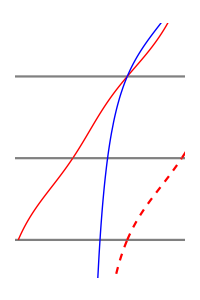

```mathematica
(*Make the simple plot *)

(*Set the overall plot range and aspect ratio*)
gmin =0.0;
gmax = 1.5;
Emin =0.6; 
Emax = 3.6;
AspectToUse1 =1.5; 
colorForOtherStates = Black;
colorForBackgroundLines = Gray;

pltTable = {}; (*to be filled*)

(*
(*A vertical line at 0 and 1 interactions*)
AppendTo[pltTable,ParametricPlot[{0,x},{x,-100,100},PlotRange->{{gmin,gmax},{Emin,Emax}},PlotStyle -> {colorForBackgroundLines}]];
AppendTo[pltTable,ParametricPlot[{1,x},{x,-100,100},PlotRange->{{gmin,gmax},{Emin,Emax}},PlotStyle -> {colorForBackgroundLines}]];
AppendTo[pltTable,ParametricPlot[{0.5,x},{x,-100,100},PlotRange->{{gmin,gmax},{Emin,Emax}},PlotStyle -> {colorForBackgroundLines}]];
*)
(*Horizontal lines *)
(*AppendTo[pltTable,ParametricPlot[{x,0},{x,-100,100},PlotRange->{{gmin,gmax},{Emin,Emax}},PlotStyle -> {colorForBackgroundLines, Thin}]]; *)
AppendTo[pltTable,ParametricPlot[{x,1},{x,-100,100},PlotRange->{{gmin,gmax},{Emin,Emax}},PlotStyle -> {colorForBackgroundLines}]];
AppendTo[pltTable,ParametricPlot[{x,2},{x,-100,100},PlotRange->{{gmin,gmax},{Emin,Emax}},PlotStyle -> {colorForBackgroundLines}]];
AppendTo[pltTable,ParametricPlot[{x,3},{x,-100,100},PlotRange->{{gmin,gmax},{Emin,Emax}},PlotStyle -> {colorForBackgroundLines}]];

(*Main 2 states, have to define them for the 0 to 1 interactions, and then redefine them again for going past the 0 crossing to the right*)
AppendTo[pltTable,plotSpecificState0toInfAndBack[1/2,1/2+2, 0,0,gmin,gmax,Emin,Emax,{Red,Thick}]];
	 (*Ground state increasing interactions*)
AppendTo[pltTable,plotSpecificState0toInfAndBack[1/2+2,1/2+4, 0,1,gmin,gmax,Emin,Emax,{Red, Thick}]];
	(*excited state increasing interactions, shifted right by 1*)
AppendTo[pltTable,plotSpecificState0toInfAndBack[-100,1/2, 2,0,gmin,gmax,Emin,Emax,{Blue, Thick}] ];
	(*bound molecule increasing interactions*)
AppendTo[pltTable,plotSpecificState0toInfAndBack[1/2,1/2+2, 2,1,gmin,gmax,Emin,Emax,{Blue,Thick}] ];
	(*Ground state increasing interactions, shifted up by 2*)

(*Lowest molecule state*)
AppendTo[pltTable,plotSpecificState0toInfAndBack[-100,1/2, 0,0,gmin,gmax,Emin,Emax,{Red,Dashed}] ];
AppendTo[pltTable,plotSpecificState0toInfAndBack[1/2,1/2+2, 0,1,gmin,gmax,Emin,Emax,{Red,Dashed}] ];

(*figInteractionTheoryPlot = Show[pltTable, ImageSize-> 400, TicksStyle ->Medium, AspectRatio ->AspectToUse1 ] *)
figInteractionTheoryPlot = Show[pltTable, ImageSize-> 200, TicksStyle ->Medium, AspectRatio ->AspectToUse1, Axes -> None]
```

NIntegrate::inumr: The integrand (3.85391 ⅇ^(1/2 (-4.35391+energy) t))/((1-ⅇ^(-3.85391 t)) √(1-ⅇ^-t))-1/t^(3/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/100000,100000}}.

NIntegrate::inumr: The integrand (3.85391 ⅇ^((-3.85391+1/2 (-4.35391+energy)) t))/((1-ⅇ^(-3.85391 t)) √(1-ⅇ^-t))-1/t^(3/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/100000,100000}}.

NIntegrate::inumr: The integrand (3.85391 ⅇ^(1/2 (-4.35391+energy) t))/((1-ⅇ^(-3.85391 t)) √(1-ⅇ^-t))-1/t^(3/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/100000,100000}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

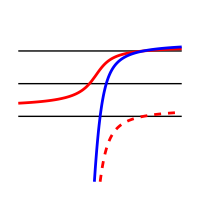

NIntegrate::inumr: The integrand (3.85391 ⅇ^(1/2 (-4.35391+energy) t))/((1-ⅇ^(-3.85391 t)) √(1-ⅇ^-t))-1/t^(3/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/100000,100000}}.

NIntegrate::inumr: The integrand (3.85391 ⅇ^((-3.85391+1/2 (-4.35391+energy)) t))/((1-ⅇ^(-3.85391 t)) √(1-ⅇ^-t))-1/t^(3/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/100000,100000}}.

NIntegrate::inumr: The integrand (3.85391 ⅇ^(1/2 (-4.35391+energy) t))/((1-ⅇ^(-3.85391 t)) √(1-ⅇ^-t))-1/t^(3/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/100000,100000}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

-Graphics-

```mathematica
(*Plot vs magnetic field *)
thicknessStates = 0.01;
thicknessLines = 0.005;
Plot[{E0+2, E0+1, E0,E2[B],E1[B]+2,E1[B]},{B,190,215}, PlotStyle -> {  {Black, Thickness[thicknessLines]},{Black, Thickness[thicknessLines ]},{Black, Thickness[thicknessLines ]},{Red,  Thickness[thicknessStates]},{Blue, Thickness[thicknessStates]},{Red, Dashed, Thickness[thicknessStates]}},PlotRange -> {{190,215},{E0-2,E0+3}}, ImageSize -> 200, AspectRatio -> 1, Axes -> None]
Plot[{E0+2, E0+1, E0,E2[B],E1[B]+2,E1[B]},{B,190,215}, PlotStyle -> {  {Black, Thickness[thicknessLines]},{Black, Thickness[thicknessLines ]},{Black, Thickness[thicknessLines ]},{Red,  Thickness[thicknessStates]},{Blue, Thickness[thicknessStates]},{Red, Dashed, Thickness[thicknessStates]}},PlotRange -> {{190,215},{E0-2,E0+3}}, ImageSize -> 100, AspectRatio -> 2, Axes -> None]
```

InterpolatingFunction::dmval: Input value {0.0000245143} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0000245143} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

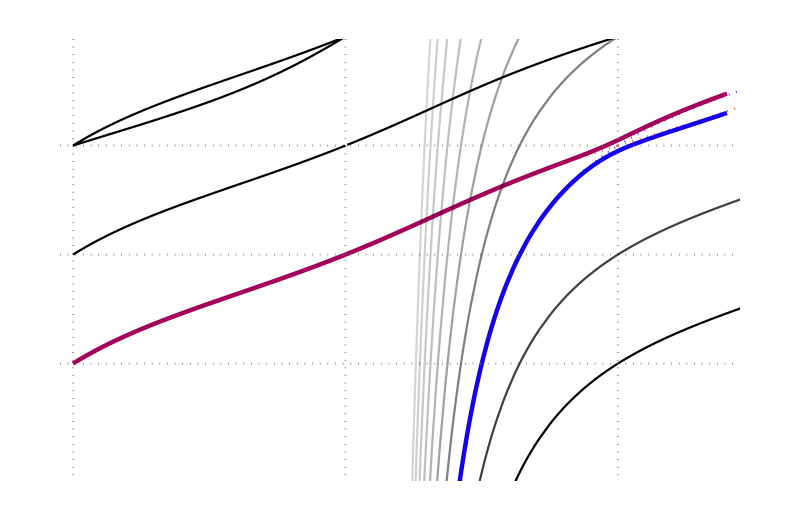

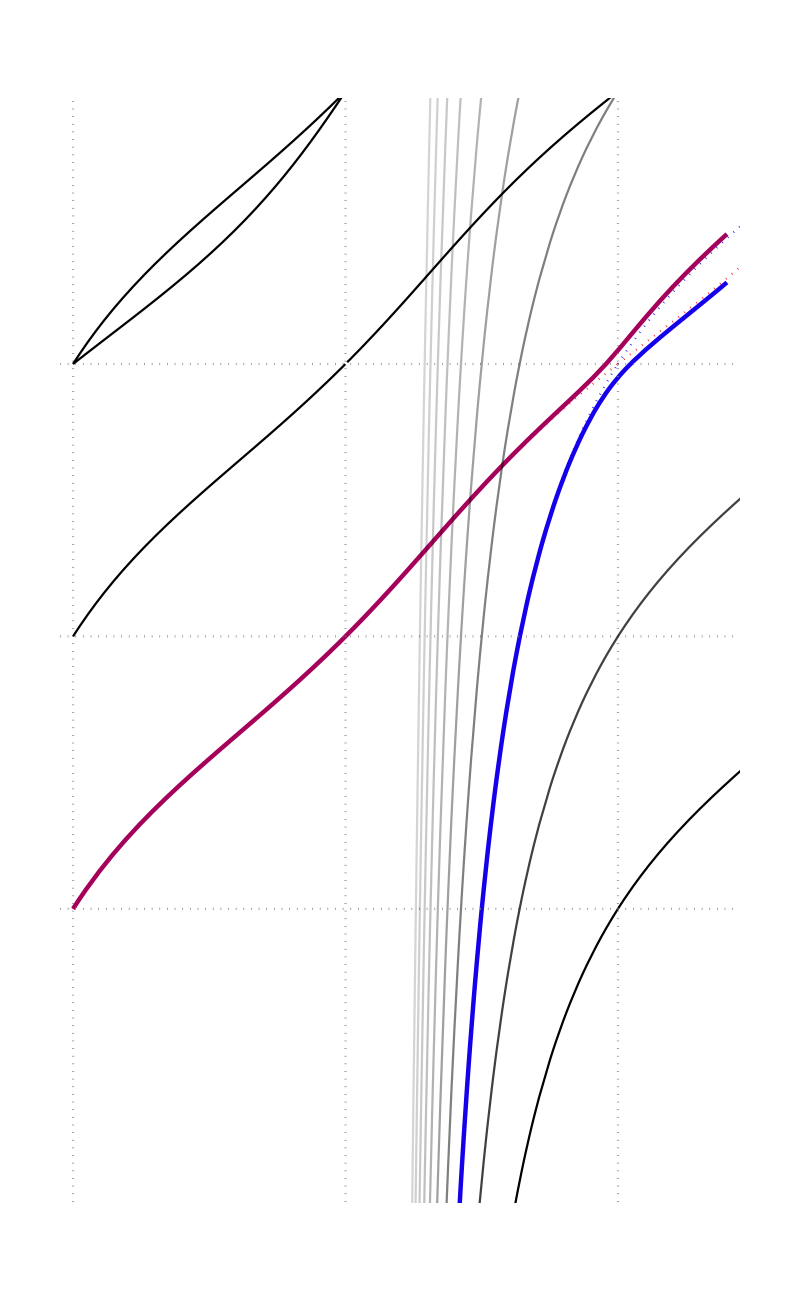

```mathematica
(*Make the complicated plot *)

(*Set the overall plot range and aspect ratio*)
gmin =0.0;
gmax = 1.2;
Emin =0; 
Emax = 3.9;
AspectToUse1 =0.65; 
AspectToUse2 =0.65*2.5; 
colorForOtherStates = Black;
colorForBackgroundLines = Gray;

pltTable = {}; (*to be filled*)

(*Main 2 states, have to define them for the 0 to 1 interactions, and then redefine them again for going past the 0 crossing to the right*)
AppendTo[pltTable,plotSpecificState0toInfAndBack[1/2,1/2+2, 0,0,gmin,gmax,Emin,Emax,{Red, Dotted}]];
	 (*Ground state increasing interactions*)
AppendTo[pltTable,plotSpecificState0toInfAndBack[1/2+2,1/2+4, 0,1,gmin,gmax,Emin,Emax,{Red, Dotted}]];
	(*excited state increasing interactions, shifted right by 1*)
AppendTo[pltTable,plotSpecificState0toInfAndBack[-100,1/2, 2,0,gmin,gmax,Emin,Emax,{Blue, Dotted}] ];
	(*bound molecule increasing interactions*)
AppendTo[pltTable,plotSpecificState0toInfAndBack[1/2,1/2+2, 2,1,gmin,gmax,Emin,Emax,{Blue, Dotted}] ];
	(*Ground state increasing interactions, shifted up by 2*)
(*Main states after fake coupling*)
lineThickness= 0.004;
plotUpper = Plot[{redblueUpper[g]},{g,gmin,gmax},ColorFunction ->{Function[{g}, upperStateColor[redblueRelativeDetuning[g]] ]},ColorFunctionScaling->False, PlotStyle -> Thickness[lineThickness],PlotRange -> {Full,Full},ImageSize-> 300, TicksStyle ->Medium, AspectRatio  -> 1 , Axes -> None];
plotLower = Plot[{redblueLower[g]},{g,gmin,gmax},ColorFunction ->{Function[{g}, lowerStateColor[redblueRelativeDetuning[g]] ]},ColorFunctionScaling->False, PlotStyle ->  Thickness[lineThickness],PlotRange -> {Full,Full},ImageSize-> 300, TicksStyle ->Medium, AspectRatio  -> 1 , Axes -> None];
AppendTo[pltTable,plotUpper];
AppendTo[pltTable,plotLower];

(*Lowest molecule state*)
AppendTo[pltTable,plotSpecificState0toInfAndBack[-100,1/2, 0,0,gmin,gmax,Emin,Emax,{colorForOtherStates,Opacity[1]}] ];
AppendTo[pltTable,plotSpecificState0toInfAndBack[1/2,1/2+2, 0,1,gmin,gmax,Emin,Emax,{colorForOtherStates,Opacity[1]}] ];
(*A vertical line at 0 and 1 interactions*)
AppendTo[pltTable,ParametricPlot[{0,x},{x,-100,100},PlotRange->{{gmin,gmax},{Emin,Emax}},PlotStyle -> {colorForBackgroundLines, Dotted}]];
AppendTo[pltTable,ParametricPlot[{1,x},{x,-100,100},PlotRange->{{gmin,gmax},{Emin,Emax}},PlotStyle -> {colorForBackgroundLines, Dotted}]];
AppendTo[pltTable,ParametricPlot[{0.5,x},{x,-100,100},PlotRange->{{gmin,gmax},{Emin,Emax}},PlotStyle -> {colorForBackgroundLines, Dotted}]];
(*Horizontal lines *)
(*AppendTo[pltTable,ParametricPlot[{x,0},{x,-100,100},PlotRange->{{gmin,gmax},{Emin,Emax}},PlotStyle -> {colorForBackgroundLines, Thin}]]; *)
AppendTo[pltTable,ParametricPlot[{x,1},{x,-100,100},PlotRange->{{gmin,gmax},{Emin,Emax}},PlotStyle -> {colorForBackgroundLines, Dotted}]];
AppendTo[pltTable,ParametricPlot[{x,2},{x,-100,100},PlotRange->{{gmin,gmax},{Emin,Emax}},PlotStyle -> {colorForBackgroundLines, Dotted}]];
AppendTo[pltTable,ParametricPlot[{x,3},{x,-100,100},PlotRange->{{gmin,gmax},{Emin,Emax}},PlotStyle -> {colorForBackgroundLines, Dotted}]];
AppendTo[pltTable,ParametricPlot[{x,4},{x,-100,100},PlotRange->{{gmin,gmax},{Emin,Emax}},PlotStyle -> {colorForBackgroundLines, Dotted}]];
AppendTo[pltTable,ParametricPlot[{x,5},{x,-100,100},PlotRange->{{gmin,gmax},{Emin,Emax}},PlotStyle -> {colorForBackgroundLines, Dotted}]];
AppendTo[pltTable,ParametricPlot[{x,6},{x,-100,100},PlotRange->{{gmin,gmax},{Emin,Emax}},PlotStyle -> {colorForBackgroundLines, Dotted}]];
AppendTo[pltTable,ParametricPlot[{x,7},{x,-100,100},PlotRange->{{gmin,gmax},{Emin,Emax}},PlotStyle -> {colorForBackgroundLines, Dotted}]];
AppendTo[pltTable,ParametricPlot[{x,8},{x,-100,100},PlotRange->{{gmin,gmax},{Emin,Emax}},PlotStyle -> {colorForBackgroundLines, Dotted}]];

(*Other non-molecule states similar to 0, with varying opacity. Each one is plotted twice from 0 to 1 and from 1 to larger.  *)
AppendTo[pltTable,plotSpecificState0toInfAndBack[1/2,1/2+2, 1,0,gmin,gmax,Emin,Emax,colorForOtherStates] ];
AppendTo[pltTable,plotSpecificState0toInfAndBack[1/2+2,1/2+4, 1,1,gmin,gmax,Emin,Emax,colorForOtherStates] ];
AppendTo[pltTable,plotSpecificState0toInfAndBack[1/2,1/2+2, 2,0,gmin,gmax,Emin,Emax,{colorForOtherStates,Opacity[1]}] ];
AppendTo[pltTable,plotSpecificState0toInfAndBack[1/2+2,1/2+4, 2,1,gmin,gmax,Emin,Emax,{colorForOtherStates,Opacity[1]}] ];
AppendTo[pltTable,plotSpecificState0toInfAndBack[1/2,1/2+2, 3,0,gmin,gmax,Emin,Emax,colorForOtherStates] ];
AppendTo[pltTable,plotSpecificState0toInfAndBack[1/2+2,1/2+4, 3,1,gmin,gmax,Emin,Emax,colorForOtherStates] ];
AppendTo[pltTable,plotSpecificState0toInfAndBack[1/2,1/2+2, 4,0,gmin,gmax,Emin,Emax,colorForOtherStates] ];
AppendTo[pltTable,plotSpecificState0toInfAndBack[1/2+2,1/2+4, 4,1,gmin,gmax,Emin,Emax,colorForOtherStates] ];
AppendTo[pltTable,plotSpecificState0toInfAndBack[1/2,1/2+2, 5,0,gmin,gmax,Emin,Emax,colorForOtherStates] ];
AppendTo[pltTable,plotSpecificState0toInfAndBack[1/2+2,1/2+4, 5,1,gmin,gmax,Emin,Emax,colorForOtherStates] ];
(*Other non-molecule states similar to 2 *)
AppendTo[pltTable,plotSpecificState0toInfAndBack[1/2+2,1/2+4, 0,0,gmin,gmax,Emin,Emax,{colorForOtherStates,Opacity[1]}] ];
AppendTo[pltTable,plotSpecificState0toInfAndBack[1/2+4,1/2+6, 0,1,gmin,gmax,Emin,Emax,{colorForOtherStates,Opacity[1]}] ];
AppendTo[pltTable,plotSpecificState0toInfAndBack[1/2+2,1/2+4, 1,0,gmin,gmax,Emin,Emax,colorForOtherStates] ];
AppendTo[pltTable,plotSpecificState0toInfAndBack[1/2+4,1/2+6, 1,1,gmin,gmax,Emin,Emax,colorForOtherStates] ];
AppendTo[pltTable,plotSpecificState0toInfAndBack[1/2+2,1/2+4, 2,0,gmin,gmax,Emin,Emax,{colorForOtherStates,Opacity[1]}] ];
AppendTo[pltTable,plotSpecificState0toInfAndBack[1/2+4,1/2+6, 2,1,gmin,gmax,Emin,Emax,{colorForOtherStates,Opacity[1]}] ];
(*Other non-molecule states similar to 4 *)
AppendTo[pltTable,plotSpecificState0toInfAndBack[1/2+4,1/2+6, 0,0,gmin,gmax,Emin,Emax,{colorForOtherStates,Opacity[1]}] ];
AppendTo[pltTable,plotSpecificState0toInfAndBack[1/2+6,1/2+8, 0,1,gmin,gmax,Emin,Emax,{colorForOtherStates,Opacity[1]}] ];
(*other molecule states*)
AppendTo[pltTable,plotSpecificState0toInfAndBack[-100,1/2, 1,0,gmin,gmax,Emin,Emax,{colorForOtherStates, Opacity[1.5/2]}] ];
AppendTo[pltTable,plotSpecificState0toInfAndBack[1/2,1/2+2, 1,1,gmin,gmax,Emin,Emax,{colorForOtherStates, Opacity[1.5/2]}] ];
AppendTo[pltTable,plotSpecificState0toInfAndBack[-100,1/2, 3,0,gmin,gmax,Emin,Emax,{colorForOtherStates, Opacity[1.5/3]}] ];
AppendTo[pltTable,plotSpecificState0toInfAndBack[1/2,1/2+2, 3,1,gmin,gmax,Emin,Emax,{colorForOtherStates, Opacity[1.5/3]}] ];
AppendTo[pltTable,plotSpecificState0toInfAndBack[-100,1/2, 4,0,gmin,gmax,Emin,Emax,{colorForOtherStates, Opacity[1.5/4]}] ];
AppendTo[pltTable,plotSpecificState0toInfAndBack[1/2,1/2+2, 4,1,gmin,gmax,Emin,Emax,{colorForOtherStates, Opacity[1.5/4]}] ];
AppendTo[pltTable,plotSpecificState0toInfAndBack[-100,1/2, 5,0,gmin,gmax,Emin,Emax,{colorForOtherStates, Opacity[1.5/5]}] ];
AppendTo[pltTable,plotSpecificState0toInfAndBack[1/2,1/2+2, 5,1,gmin,gmax,Emin,Emax,{colorForOtherStates, Opacity[1.5/5]}] ];
AppendTo[pltTable,plotSpecificState0toInfAndBack[-100,1/2, 6,0,gmin,gmax,Emin,Emax,{colorForOtherStates, Opacity[1.5/6]}] ];
AppendTo[pltTable,plotSpecificState0toInfAndBack[1/2,1/2+2, 6,1,gmin,gmax,Emin,Emax,{colorForOtherStates, Opacity[1.5/6]}] ];
AppendTo[pltTable,plotSpecificState0toInfAndBack[-100,1/2, 7,0,gmin,gmax,Emin,Emax,{colorForOtherStates, Opacity[1.5/7]}] ];
AppendTo[pltTable,plotSpecificState0toInfAndBack[1/2,1/2+2, 7,1,gmin,gmax,Emin,Emax,{colorForOtherStates, Opacity[1.5/7]}] ];
AppendTo[pltTable,plotSpecificState0toInfAndBack[-100,1/2, 8,0,gmin,gmax,Emin,Emax,{colorForOtherStates, Opacity[1.5/8]}] ];
AppendTo[pltTable,plotSpecificState0toInfAndBack[1/2,1/2+2, 8,1,gmin,gmax,Emin,Emax,{colorForOtherStates, Opacity[1.5/8]}] ];
AppendTo[pltTable,plotSpecificState0toInfAndBack[-100,1/2, 9,0,gmin,gmax,Emin,Emax,{colorForOtherStates, Opacity[1.5/9]}] ];
AppendTo[pltTable,plotSpecificState0toInfAndBack[1/2,1/2+2, 9,1,gmin,gmax,Emin,Emax,{colorForOtherStates, Opacity[1.5/9]}] ];
(*figInteractionTheoryPlot = Show[pltTable, ImageSize-> 400, TicksStyle ->Medium, AspectRatio ->AspectToUse1 ] *)
figInteractionTheoryPlot = Show[pltTable, ImageSize-> 800, TicksStyle ->Medium, AspectRatio ->AspectToUse1, Axes -> None]
figInteractionTheoryPlot = Show[pltTable, ImageSize-> 800, TicksStyle ->Medium, AspectRatio ->AspectToUse2, Axes -> None]
```

Now make a plot where we zoom in on the avoided crossing

NIntegrate::inumr: The integrand (3.85391 ⅇ^(1/2 (-4.35391+energy) t))/((1-ⅇ^(-3.85391 t)) √(1-ⅇ^-t))-1/t^(3/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/100000,100000}}.

NIntegrate::inumr: The integrand (3.85391 ⅇ^((-3.85391+1/2 (-4.35391+energy)) t))/((1-ⅇ^(-3.85391 t)) √(1-ⅇ^-t))-1/t^(3/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/100000,100000}}.

NIntegrate::inumr: The integrand (3.85391 ⅇ^(1/2 (-4.35391+energy) t))/((1-ⅇ^(-3.85391 t)) √(1-ⅇ^-t))-1/t^(3/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/100000,100000}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand (3.85391 ⅇ^(1/2 (-4.35391+energy) t))/((1-ⅇ^(-3.85391 t)) √(1-ⅇ^-t))-1/t^(3/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/100000,100000}}.

NIntegrate::inumr: The integrand (3.85391 ⅇ^((-3.85391+1/2 (-4.35391+energy)) t))/((1-ⅇ^(-3.85391 t)) √(1-ⅇ^-t))-1/t^(3/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/100000,100000}}.

NIntegrate::inumr: The integrand (3.85391 ⅇ^(1/2 (-4.35391+energy) t))/((1-ⅇ^(-3.85391 t)) √(1-ⅇ^-t))-1/t^(3/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/100000,100000}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand (3.85391 ⅇ^(1/2 (-4.35391+energy) t))/((1-ⅇ^(-3.85391 t)) √(1-ⅇ^-t))-1/t^(3/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/100000,100000}}.

NIntegrate::inumr: The integrand (3.85391 ⅇ^((-3.85391+1/2 (-4.35391+energy)) t))/((1-ⅇ^(-3.85391 t)) √(1-ⅇ^-t))-1/t^(3/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/100000,100000}}.

NIntegrate::inumr: The integrand (3.85391 ⅇ^(1/2 (-4.35391+energy) t))/((1-ⅇ^(-3.85391 t)) √(1-ⅇ^-t))-1/t^(3/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/100000,100000}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand (3.85391 ⅇ^(1/2 (-4.35391+energy) t))/((1-ⅇ^(-3.85391 t)) √(1-ⅇ^-t))-1/t^(3/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/100000,100000}}.

NIntegrate::inumr: The integrand (3.85391 ⅇ^((-3.85391+1/2 (-4.35391+energy)) t))/((1-ⅇ^(-3.85391 t)) √(1-ⅇ^-t))-1/t^(3/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/100000,100000}}.

NIntegrate::inumr: The integrand (3.85391 ⅇ^(1/2 (-4.35391+energy) t))/((1-ⅇ^(-3.85391 t)) √(1-ⅇ^-t))-1/t^(3/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/100000,100000}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

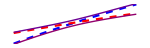

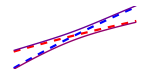

```mathematica
AvoidedCrossingPlotBMin =BCross-0.5;
AvoidedCrossingPlotBMax = BCross+0.5;
(*
If interactions only went to 1, and aspect ratio was 1 for the main graph, then the slope of the red line in the main graph would be 1/2. But aspect ratio is 0.5 so slope becomes 1/4, and then we extend it further so slope is 0.25/1.15. 
*)

AspectToUse1 =0.25/1.1;
AspectToUse2 =0.5;

plotUpper = Plot[{(EUpper[B]-(E0+2))},{B,AvoidedCrossingPlotBMin,AvoidedCrossingPlotBMax},ColorFunction ->{Function[{B}, upperStateColor[relativeDetuning[B]] ]},ColorFunctionScaling->False, PlotStyle -> Thick,PlotRange -> {Full,Full},ImageSize-> 300, TicksStyle ->Medium, AspectRatio  -> 1 , Axes -> None];
plotLower = Plot[{(ELower[B]-(E0+2))},{B,AvoidedCrossingPlotBMin,AvoidedCrossingPlotBMax},ColorFunction ->{Function[{B}, lowerStateColor[relativeDetuning[B]] ]},ColorFunctionScaling->False,PlotStyle -> Thick, PlotRange -> {Full,Full},ImageSize-> 300, TicksStyle ->Medium, AspectRatio  -> 1 , Axes -> None];
plotDashedBlue = Plot[{(E2C0R[B]-(E0+2))},{B,AvoidedCrossingPlotBMin,AvoidedCrossingPlotBMax},PlotStyle -> {{Blue, Dashed}},  PlotRange -> {Full,Full},ImageSize-> 300, TicksStyle ->Medium, AspectRatio  -> 1 , Axes -> None];
plotDashedRed = Plot[{(E0C2R[B]-(E0+2))},{B,AvoidedCrossingPlotBMin,AvoidedCrossingPlotBMax},PlotStyle -> { {Red, Dashed}},  PlotRange -> {Full,Full},ImageSize-> 300, TicksStyle ->Medium, AspectRatio  -> 1 , Axes -> None];
Show[{plotDashedBlue,plotDashedRed,plotUpper,plotLower}, ImageResolution -> 600, ImageSize -> 150,AspectRatio -> AspectToUse1]
Show[{plotDashedBlue,plotDashedRed,plotUpper,plotLower}, ImageResolution -> 600, ImageSize -> 150,AspectRatio -> AspectToUse2]
```

#### Get real energy of states (in Hz) vs real interaction strength and vs real B field in an anisotropic 3D SHO with our measured parameters

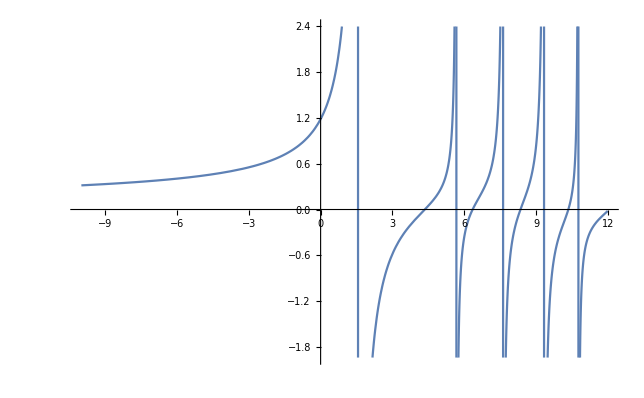

```mathematica
Plot[a3DForNonIntegernForAnisotropic3DSHO[en, ηeff], {en,-10,7 + 5}]
```

NIntegrate::inumr: The integrand (3.85339 ⅇ^(1/2 (-4.35339+energy) t))/((1-ⅇ^(-3.85339 t)) √(1-ⅇ^-t))-1/t^(3/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/100000,100000}}.

NIntegrate::inumr: The integrand (3.85339 ⅇ^((-3.85339+1/2 (-4.35339+energy)) t))/((1-ⅇ^(-3.85339 t)) √(1-ⅇ^-t))-1/t^(3/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/100000,100000}}.

NIntegrate::inumr: The integrand (3.85339 ⅇ^(1/2 (-4.35339+energy) t))/((1-ⅇ^(-3.85339 t)) √(1-ⅇ^-t))-1/t^(3/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/100000,100000}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

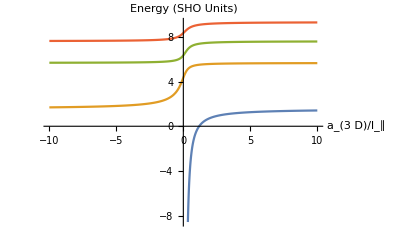

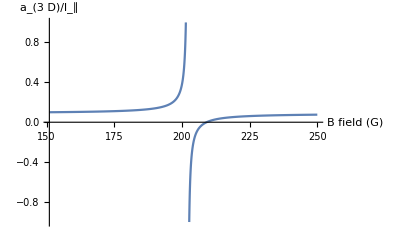

```mathematica
Plot[{EbForAlla[a],E1ForAlla[a],E2ForAlla[a],E3ForAlla[a]}, {a,-10,10},AxesLabel -> {"a_(3  D)/l_∥", "Energy (SHO Units)"}] 
Plot[a3D[B], {B,151, 250}, PlotRange ->{-1,1}, AxesLabel -> {"B field (G)","a_(3  D)/l_∥"}]
```

NIntegrate::inumr: The integrand (3.85339 ⅇ^(1/2 (-4.35339+energy) t))/((1-ⅇ^(-3.85339 t)) √(1-ⅇ^-t))-1/t^(3/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/100000,100000}}.

NIntegrate::inumr: The integrand (3.85339 ⅇ^((-3.85339+1/2 (-4.35339+energy)) t))/((1-ⅇ^(-3.85339 t)) √(1-ⅇ^-t))-1/t^(3/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/100000,100000}}.

NIntegrate::inumr: The integrand (3.85339 ⅇ^(1/2 (-4.35339+energy) t))/((1-ⅇ^(-3.85339 t)) √(1-ⅇ^-t))-1/t^(3/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/100000,100000}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

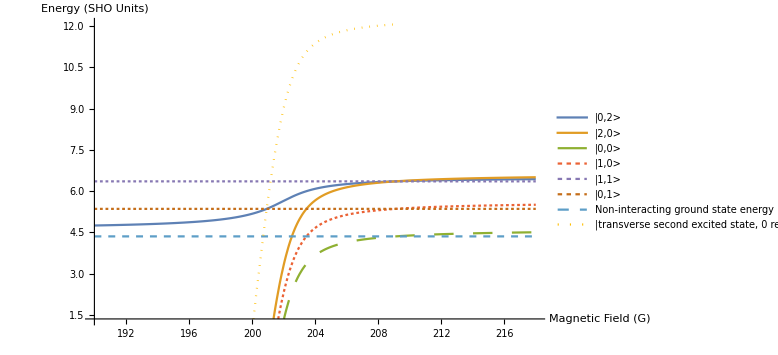

```mathematica
BstartEplot =190;
BendEplot = 218;
Eplotmin = E0-3;
Eplotmax=E0+2ηeff;
Plot[{E2[B],E1[B]+2,E1[B],E1[B]+1, E0+2, E0+1, E0,E1[B]+2*ηeff},{B,BstartEplot,BendEplot}, PlotStyle -> {Automatic, Automatic,  Dashing[Large], Dashing[Tiny],Dashing[Tiny], Dashing[Tiny], Dashed, Dotted},PlotRange -> {{BstartEplot,BendEplot},{Eplotmin ,Eplotmax}},PlotLegends -> {"|0,2>","|2,0>", "|0,0>" , "|1,0>","|1,1>", "|0,1>", "Non-interacting ground state energy","|transverse second excited state, 0 relative>"}, AxesLabel -> {"Magnetic Field (G)", "Energy (SHO Units)"}, ImageSize -> Large]
```

NIntegrate::inumr: The integrand (3.85339 ⅇ^(1/2 (-4.35339+energy) t))/((1-ⅇ^(-3.85339 t)) √(1-ⅇ^-t))-1/t^(3/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/100000,100000}}.

NIntegrate::inumr: The integrand (3.85339 ⅇ^((-3.85339+1/2 (-4.35339+energy)) t))/((1-ⅇ^(-3.85339 t)) √(1-ⅇ^-t))-1/t^(3/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/100000,100000}}.

NIntegrate::inumr: The integrand (3.85339 ⅇ^(1/2 (-4.35339+energy) t))/((1-ⅇ^(-3.85339 t)) √(1-ⅇ^-t))-1/t^(3/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/100000,100000}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand (3.85339 ⅇ^(1/2 (-4.35339+energy) t))/((1-ⅇ^(-3.85339 t)) √(1-ⅇ^-t))-1/t^(3/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/100000,100000}}.

NIntegrate::inumr: The integrand (3.85339 ⅇ^((-3.85339+1/2 (-4.35339+energy)) t))/((1-ⅇ^(-3.85339 t)) √(1-ⅇ^-t))-1/t^(3/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/100000,100000}}.

NIntegrate::inumr: The integrand (3.85339 ⅇ^(1/2 (-4.35339+energy) t))/((1-ⅇ^(-3.85339 t)) √(1-ⅇ^-t))-1/t^(3/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/100000,100000}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand (3.85339 ⅇ^(1/2 (-4.35339+energy) t))/((1-ⅇ^(-3.85339 t)) √(1-ⅇ^-t))-1/t^(3/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/100000,100000}}.

NIntegrate::inumr: The integrand (3.85339 ⅇ^((-3.85339+1/2 (-4.35339+energy)) t))/((1-ⅇ^(-3.85339 t)) √(1-ⅇ^-t))-1/t^(3/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/100000,100000}}.

NIntegrate::inumr: The integrand (3.85339 ⅇ^(1/2 (-4.35339+energy) t))/((1-ⅇ^(-3.85339 t)) √(1-ⅇ^-t))-1/t^(3/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/100000,100000}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

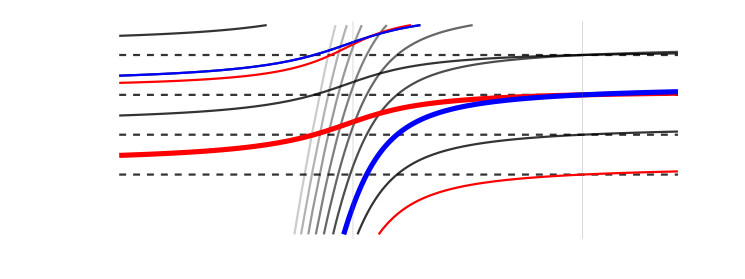

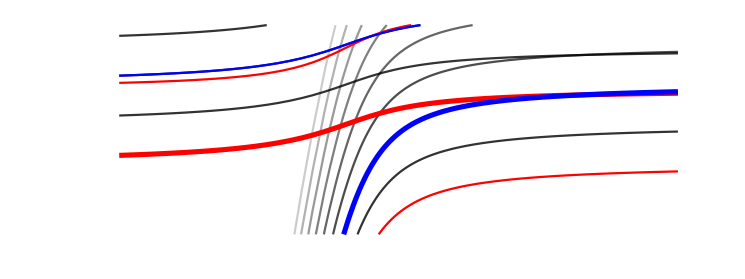

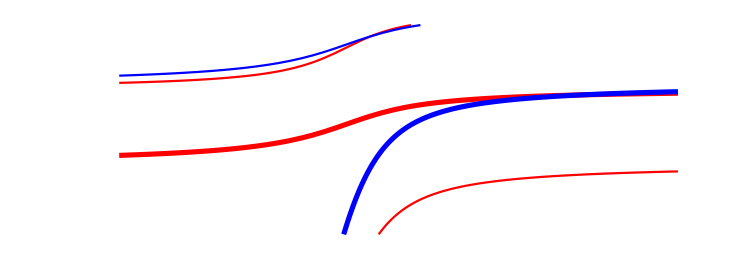

```mathematica
BstartEplot =195;
BendEplot = 212;
Eplotmin = E0-1.5 ;
Eplotmax=E0+3.75;
imgSizeToUse = 745;
AspectRatioToUse= 0.375;

pltMain = Plot[{E2[B],E1[B]+2,E1[B], E3[B],E2[B]+2},{B,BstartEplot,BendEplot}, PlotStyle -> 
{{Red, Thickness[imgSizeToUse/150000]}, {Blue,  Thickness[imgSizeToUse/150000]},  {Red},{Red}, {Blue}},
PlotRange -> {{BstartEplot,BendEplot},{Eplotmin ,Eplotmax}
}, AxesLabel -> {"Magnetic Field (G)", "Energy (SHO Units)"}, ImageSize ->imgSizeToUse, AspectRatio -> AspectRatioToUse, Axes -> None];
pltLines = Plot[{ E0+3,E0+2, E0+1, E0},{B,BstartEplot,BendEplot}, PlotStyle -> 
{{Black, Opacity[0.8],Dashed},{Black, Opacity[0.8],Dashed},{Black, Opacity[0.8],Dashed},{Black, Opacity[0.8], Dashed}},
GridLines->{{{B0, {Gray, Thickness[0.002]}},{BCross, {Gray, Thickness[0.002]}}}},
PlotRange -> {{BstartEplot,BendEplot},{Eplotmin ,Eplotmax}
}, AxesLabel -> {"Magnetic Field (G)", "Energy (SHO Units)"}, ImageSize ->imgSizeToUse, AspectRatio ->AspectRatioToUse, Axes -> None];
pltMolecules = Plot[{ E1[B]+1,E1[B]+3,E1[B]+4,E1[B]+5,E1[B]+6,E1[B]+7,E1[B]+8},{B,BstartEplot,BendEplot}, PlotStyle -> 
{{Black, Opacity[0.8]},{Black, Opacity[0.7]},{Black, Opacity[0.6]},{Black, Opacity[0.5]},{Black, Opacity[0.4]},{Black, Opacity[0.3]},{Black, Opacity[0.2]}},
PlotRange -> {{BstartEplot,BendEplot},{Eplotmin ,Eplotmax}
}, AxesLabel -> {"Magnetic Field (G)", "Energy (SHO Units)"}, ImageSize ->imgSizeToUse, AspectRatio -> AspectRatioToUse, Axes -> None];
pltOtherInteractingStates = Plot[{ E2[B]+1,E2[B]+2,E2[B]+3},{B,BstartEplot,BendEplot}, PlotStyle -> 
{{Black, Opacity[0.8]},{Black, Opacity[0.8]},{Black, Opacity[0.8]}},
PlotRange -> {{BstartEplot,BendEplot},{Eplotmin ,Eplotmax}
}, AxesLabel -> {"Magnetic Field (G)", "Energy (SHO Units)"}, ImageSize ->imgSizeToUse, AspectRatio -> AspectRatioToUse, Axes -> None];  
Show[{pltLines,pltMolecules,pltOtherInteractingStates, pltMain}]
Show[{pltMolecules,pltOtherInteractingStates, pltMain}]
Show[{pltMain}]
```

NIntegrate::inumr: The integrand (3.85339 ⅇ^(1/2 (-4.35339+energy) t))/((1-ⅇ^(-3.85339 t)) √(1-ⅇ^-t))-1/t^(3/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/100000,100000}}.

NIntegrate::inumr: The integrand (3.85339 ⅇ^((-3.85339+1/2 (-4.35339+energy)) t))/((1-ⅇ^(-3.85339 t)) √(1-ⅇ^-t))-1/t^(3/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/100000,100000}}.

NIntegrate::inumr: The integrand (3.85339 ⅇ^(1/2 (-4.35339+energy) t))/((1-ⅇ^(-3.85339 t)) √(1-ⅇ^-t))-1/t^(3/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/100000,100000}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand (3.85339 ⅇ^(1/2 (-4.35339+energy) t))/((1-ⅇ^(-3.85339 t)) √(1-ⅇ^-t))-1/t^(3/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/100000,100000}}.

NIntegrate::inumr: The integrand (3.85339 ⅇ^((-3.85339+1/2 (-4.35339+energy)) t))/((1-ⅇ^(-3.85339 t)) √(1-ⅇ^-t))-1/t^(3/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/100000,100000}}.

NIntegrate::inumr: The integrand (3.85339 ⅇ^(1/2 (-4.35339+energy) t))/((1-ⅇ^(-3.85339 t)) √(1-ⅇ^-t))-1/t^(3/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/100000,100000}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand (3.85339 ⅇ^(1/2 (-4.35339+energy) t))/((1-ⅇ^(-3.85339 t)) √(1-ⅇ^-t))-1/t^(3/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/100000,100000}}.

NIntegrate::inumr: The integrand (3.85339 ⅇ^((-3.85339+1/2 (-4.35339+energy)) t))/((1-ⅇ^(-3.85339 t)) √(1-ⅇ^-t))-1/t^(3/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/100000,100000}}.

NIntegrate::inumr: The integrand (3.85339 ⅇ^(1/2 (-4.35339+energy) t))/((1-ⅇ^(-3.85339 t)) √(1-ⅇ^-t))-1/t^(3/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/100000,100000}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

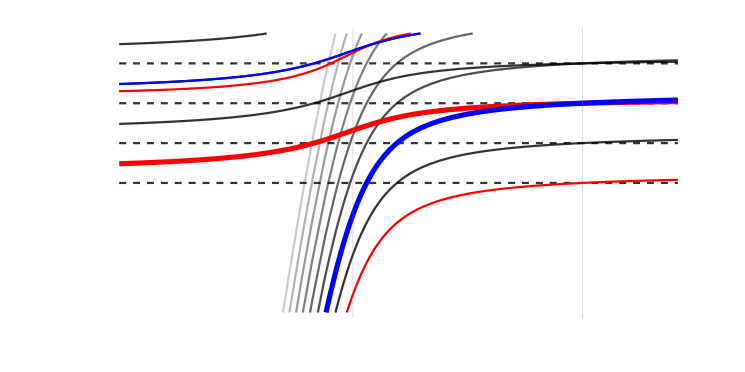

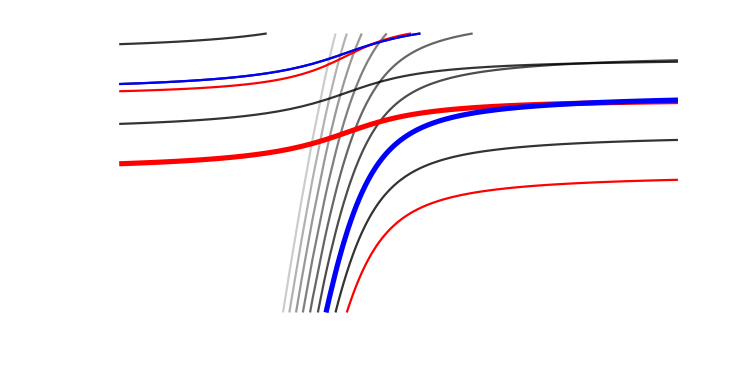

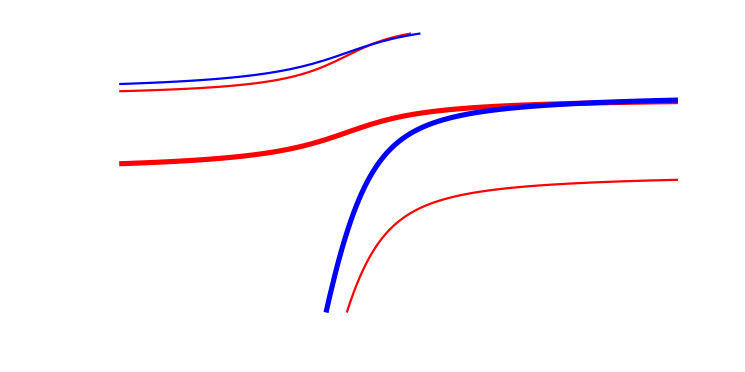

```mathematica
BstartEplot =195;
BendEplot = 212;
Eplotmin = E0-1.5 - 5.25*1/3;
Eplotmax=E0+3.75;
imgSizeToUse = 745;
AspectRatioToUse= 0.375*4/3;

pltMain = Plot[{E2[B],E1[B]+2,E1[B], E3[B],E2[B]+2},{B,BstartEplot,BendEplot}, PlotStyle -> 
{{Red, Thickness[imgSizeToUse/150000]}, {Blue,  Thickness[imgSizeToUse/150000]},  {Red},{Red}, {Blue}},
PlotRange -> {{BstartEplot,BendEplot},{Eplotmin ,Eplotmax}
}, AxesLabel -> {"Magnetic Field (G)", "Energy (SHO Units)"}, ImageSize ->imgSizeToUse, AspectRatio -> AspectRatioToUse, Axes -> None];
pltLines = Plot[{ E0+3,E0+2, E0+1, E0},{B,BstartEplot,BendEplot}, PlotStyle -> 
{{Black, Opacity[0.8],Dashed},{Black, Opacity[0.8],Dashed},{Black, Opacity[0.8],Dashed},{Black, Opacity[0.8], Dashed}},
GridLines->{{{B0, {Gray, Thickness[0.002]}},{BCross, {Gray, Thickness[0.002]}}}},
PlotRange -> {{BstartEplot,BendEplot},{Eplotmin ,Eplotmax}
}, AxesLabel -> {"Magnetic Field (G)", "Energy (SHO Units)"}, ImageSize ->imgSizeToUse, AspectRatio ->AspectRatioToUse, Axes -> None];
pltMolecules = Plot[{ E1[B]+1,E1[B]+3,E1[B]+4,E1[B]+5,E1[B]+6,E1[B]+7,E1[B]+8},{B,BstartEplot,BendEplot}, PlotStyle -> 
{{Black, Opacity[0.8]},{Black, Opacity[0.7]},{Black, Opacity[0.6]},{Black, Opacity[0.5]},{Black, Opacity[0.4]},{Black, Opacity[0.3]},{Black, Opacity[0.2]}},
PlotRange -> {{BstartEplot,BendEplot},{Eplotmin ,Eplotmax}
}, AxesLabel -> {"Magnetic Field (G)", "Energy (SHO Units)"}, ImageSize ->imgSizeToUse, AspectRatio -> AspectRatioToUse, Axes -> None];
pltOtherInteractingStates = Plot[{ E2[B]+1,E2[B]+2,E2[B]+3},{B,BstartEplot,BendEplot}, PlotStyle -> 
{{Black, Opacity[0.8]},{Black, Opacity[0.8]},{Black, Opacity[0.8]}},
PlotRange -> {{BstartEplot,BendEplot},{Eplotmin ,Eplotmax}
}, AxesLabel -> {"Magnetic Field (G)", "Energy (SHO Units)"}, ImageSize ->imgSizeToUse, AspectRatio -> AspectRatioToUse, Axes -> None];  
Show[{pltLines,pltMolecules,pltOtherInteractingStates, pltMain}]
Show[{pltMolecules,pltOtherInteractingStates, pltMain}]
Show[{pltMain}]
```

NIntegrate::inumr: The integrand (3.85339 ⅇ^(1/2 (-4.35339+energy) t))/((1-ⅇ^(-3.85339 t)) √(1-ⅇ^-t))-1/t^(3/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/100000,100000}}.

NIntegrate::inumr: The integrand (3.85339 ⅇ^((-3.85339+1/2 (-4.35339+energy)) t))/((1-ⅇ^(-3.85339 t)) √(1-ⅇ^-t))-1/t^(3/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/100000,100000}}.

NIntegrate::inumr: The integrand (3.85339 ⅇ^(1/2 (-4.35339+energy) t))/((1-ⅇ^(-3.85339 t)) √(1-ⅇ^-t))-1/t^(3/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/100000,100000}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand (3.85339 ⅇ^(1/2 (-4.35339+energy) t))/((1-ⅇ^(-3.85339 t)) √(1-ⅇ^-t))-1/t^(3/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/100000,100000}}.

NIntegrate::inumr: The integrand (3.85339 ⅇ^((-3.85339+1/2 (-4.35339+energy)) t))/((1-ⅇ^(-3.85339 t)) √(1-ⅇ^-t))-1/t^(3/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/100000,100000}}.

NIntegrate::inumr: The integrand (3.85339 ⅇ^(1/2 (-4.35339+energy) t))/((1-ⅇ^(-3.85339 t)) √(1-ⅇ^-t))-1/t^(3/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/100000,100000}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand (3.85339 ⅇ^(1/2 (-4.35339+energy) t))/((1-ⅇ^(-3.85339 t)) √(1-ⅇ^-t))-1/t^(3/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/100000,100000}}.

NIntegrate::inumr: The integrand (3.85339 ⅇ^((-3.85339+1/2 (-4.35339+energy)) t))/((1-ⅇ^(-3.85339 t)) √(1-ⅇ^-t))-1/t^(3/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/100000,100000}}.

NIntegrate::inumr: The integrand (3.85339 ⅇ^(1/2 (-4.35339+energy) t))/((1-ⅇ^(-3.85339 t)) √(1-ⅇ^-t))-1/t^(3/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/100000,100000}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

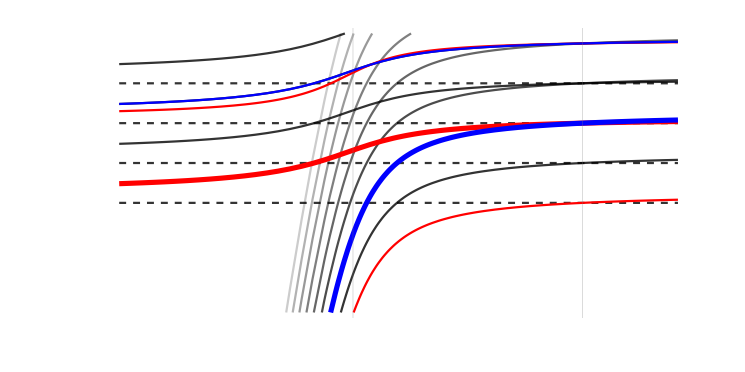

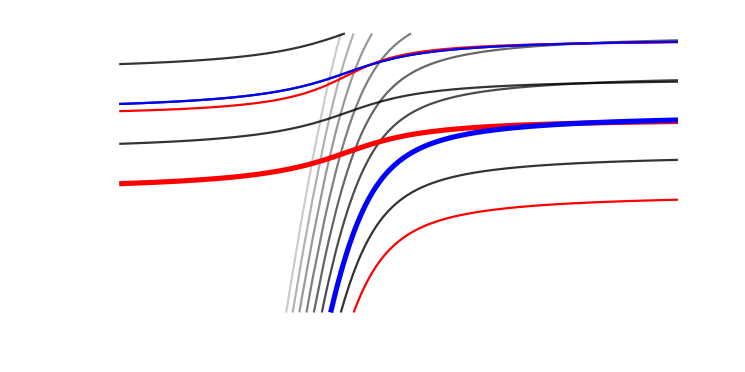

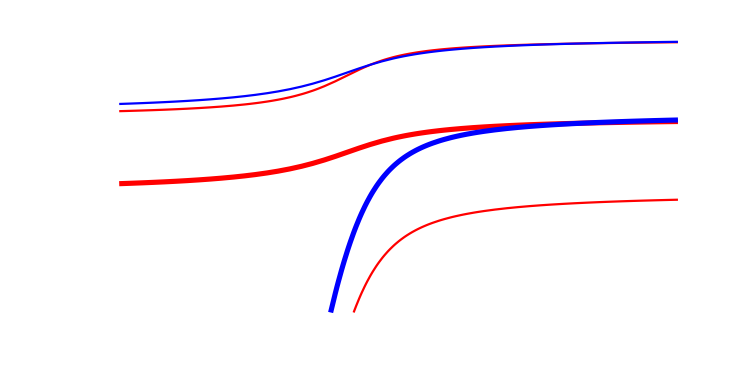

```mathematica
BstartEplot =195;
BendEplot = 212;
Eplotmin = E0-1.5 - 5.25*1/3+0.5;
Eplotmax=E0+3.75+0.5;
imgSizeToUse = 745;
AspectRatioToUse= 0.375*4/3;

pltMain = Plot[{E2[B],E1[B]+2,E1[B], E3[B],E2[B]+2},{B,BstartEplot,BendEplot}, PlotStyle -> 
{{Red, Thickness[imgSizeToUse/150000]}, {Blue,  Thickness[imgSizeToUse/150000]},  {Red},{Red}, {Blue}},
PlotRange -> {{BstartEplot,BendEplot},{Eplotmin ,Eplotmax}
}, AxesLabel -> {"Magnetic Field (G)", "Energy (SHO Units)"}, ImageSize ->imgSizeToUse, AspectRatio -> AspectRatioToUse, Axes -> None];
pltLines = Plot[{ E0+3,E0+2, E0+1, E0},{B,BstartEplot,BendEplot}, PlotStyle -> 
{{Black, Opacity[0.8],Dashed},{Black, Opacity[0.8],Dashed},{Black, Opacity[0.8],Dashed},{Black, Opacity[0.8], Dashed}},
GridLines->{{{B0, {Gray, Thickness[0.002]}},{BCross, {Gray, Thickness[0.002]}}}},
PlotRange -> {{BstartEplot,BendEplot},{Eplotmin ,Eplotmax}
}, AxesLabel -> {"Magnetic Field (G)", "Energy (SHO Units)"}, ImageSize ->imgSizeToUse, AspectRatio ->AspectRatioToUse, Axes -> None];
pltMolecules = Plot[{ E1[B]+1,E1[B]+3,E1[B]+4,E1[B]+5,E1[B]+6,E1[B]+7,E1[B]+8},{B,BstartEplot,BendEplot}, PlotStyle -> 
{{Black, Opacity[0.8]},{Black, Opacity[0.7]},{Black, Opacity[0.6]},{Black, Opacity[0.5]},{Black, Opacity[0.4]},{Black, Opacity[0.3]},{Black, Opacity[0.2]}},
PlotRange -> {{BstartEplot,BendEplot},{Eplotmin ,Eplotmax}
}, AxesLabel -> {"Magnetic Field (G)", "Energy (SHO Units)"}, ImageSize ->imgSizeToUse, AspectRatio -> AspectRatioToUse, Axes -> None];
pltOtherInteractingStates = Plot[{ E2[B]+1,E2[B]+2,E2[B]+3},{B,BstartEplot,BendEplot}, PlotStyle -> 
{{Black, Opacity[0.8]},{Black, Opacity[0.8]},{Black, Opacity[0.8]}},
PlotRange -> {{BstartEplot,BendEplot},{Eplotmin ,Eplotmax}
}, AxesLabel -> {"Magnetic Field (G)", "Energy (SHO Units)"}, ImageSize ->imgSizeToUse, AspectRatio -> AspectRatioToUse, Axes -> None];  
Show[{pltLines,pltMolecules,pltOtherInteractingStates, pltMain}]
Show[{pltMolecules,pltOtherInteractingStates, pltMain}]
Show[{pltMain}]
```

NIntegrate::inumr: The integrand (3.85391 ⅇ^(1/2 (-4.35391+energy) t))/((1-ⅇ^(-3.85391 t)) √(1-ⅇ^-t))-1/t^(3/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/100000,100000}}.

NIntegrate::inumr: The integrand (3.85391 ⅇ^((-3.85391+1/2 (-4.35391+energy)) t))/((1-ⅇ^(-3.85391 t)) √(1-ⅇ^-t))-1/t^(3/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/100000,100000}}.

NIntegrate::inumr: The integrand (3.85391 ⅇ^(1/2 (-4.35391+energy) t))/((1-ⅇ^(-3.85391 t)) √(1-ⅇ^-t))-1/t^(3/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/100000,100000}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

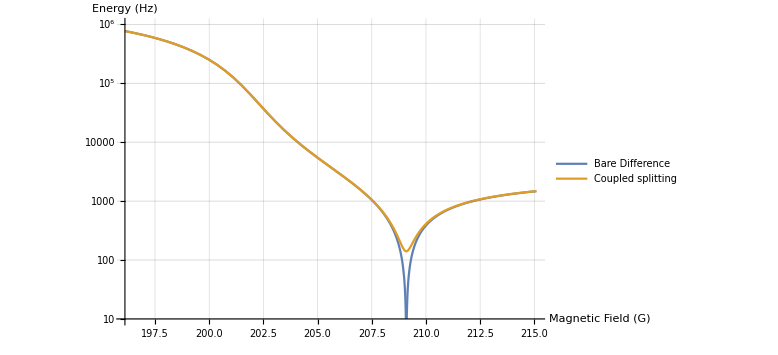

```mathematica
pltRamsey = LogPlot[{Abs[(E0C2R[B]-(E0+2))ωPar/(2π)-(E2C0R[B]-(E0+2))ωPar/(2π)],Abs[(EUpper[B]-(E0+2))ωPar/(2π)-(ELower[B]-(E0+2))ωPar/(2π)]},{B,B0-6,BCross+6},AxesLabel -> {"Magnetic Field (G)", "Energy (Hz)"},
PlotStyle -> {Automatic}, PlotRange ->{{B0-6,BCross+6},{10^1, 10^6}},GridLines -> Automatic,
PlotLegends -> {"Bare Difference", "Coupled splitting"}, ImageSize -> Large]
```

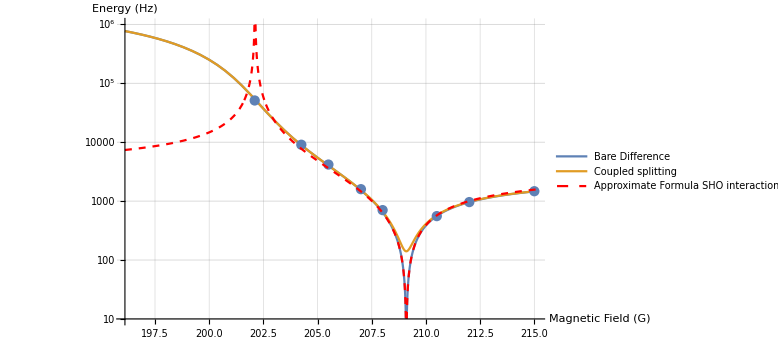

```mathematica
expPrelimData = {{215,1471}, {202.1, 51000}, {205.5,4170}, {207, 1594}, {212, 962}, {210.5, 556}, {208, 703}, {204.25, 9050}};
pltPrelimRamseyData = ListPlot[expPrelimData,  PlotRange ->{{B0-6,BCross+6},{10^1, 10^6}}, ScalingFunctions -> {Automatic, "Log"}];
pltApproxUFormula = LogPlot[{ApproxInteractionFreqGuess[B]},{B,B0-6,BCross+6},AxesLabel -> {"Magnetic Field (G)", "Energy (Hz)"},
PlotStyle -> {Red, Dashed}, PlotRange ->{{B0-6,BCross+6},{10^1, 10^6}},GridLines -> Automatic,
PlotLegends -> {"Approximate Formula SHO interaction"}, ImageSize -> Large];
Show[{pltRamsey ,pltPrelimRamseyData,pltApproxUFormula}]
```

#### Generate Theory Data for Qubit Splitting Vs Field for Ramsey Figure

Now generate a set of datapoints to plot with the experimental data for each experimental and theory curve

```mathematica
BStart=B0-6;
BStop = BCross +12;
BSpacing = 0.092457*2; (*Some random number to avoid infinities at the feshbach resonance*)
BStartZoom= BCross -0.3; (*for zoom in on 0 crossing*)
BStopZoom = BCross +0.3;
BSpacingZoom = 0.005; (*Some random number to avoid infinities at the feshbach resonance*)

tabOfFieldSetpoints = Table[B, {B,BStart, BStop, BSpacing}];
tabOfFieldSetpoints =Join[tabOfFieldSetpoints , Table[B, {B,BStartZoom, BStopZoom, BSpacingZoom}]]; (*Add more dense points near resonance*)
tabOfFieldSetpoints= Sort[tabOfFieldSetpoints];
tabOfThBareDifference = Table[Abs[(E0C2R[B]-(E0+2))ωPar/(2π)-(E2C0R[B]-(E0+2))ωPar/(2π)], {B,tabOfFieldSetpoints}];
tabOfThCoupledDifference = Table[Abs[(EUpper[B]-(E0+2))ωPar/(2π)-(ELower[B]-(E0+2))ωPar/(2π)], {B,tabOfFieldSetpoints}];
tabOfThBareDifferenceApproxFormula = Table[ApproxInteractionFreqGuess[B], {B,tabOfFieldSetpoints}];
```

NIntegrate::inumr: The integrand (3.85339 ⅇ^(1/2 (-4.35339+energy) t))/((1-ⅇ^(-3.85339 t)) √(1-ⅇ^-t))-1/t^(3/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/100000,100000}}.

NIntegrate::inumr: The integrand (3.85339 ⅇ^((-3.85339+1/2 (-4.35339+energy)) t))/((1-ⅇ^(-3.85339 t)) √(1-ⅇ^-t))-1/t^(3/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/100000,100000}}.

NIntegrate::inumr: The integrand (3.85339 ⅇ^(1/2 (-4.35339+energy) t))/((1-ⅇ^(-3.85339 t)) √(1-ⅇ^-t))-1/t^(3/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/100000,100000}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand (3.85339 ⅇ^(1/2 (-4.35339+energy) t))/((1-ⅇ^(-3.85339 t)) √(1-ⅇ^-t))-1/t^(3/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/100000,100000}}.

NIntegrate::inumr: The integrand (3.85339 ⅇ^((-3.85339+1/2 (-4.35339+energy)) t))/((1-ⅇ^(-3.85339 t)) √(1-ⅇ^-t))-1/t^(3/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/100000,100000}}.

NIntegrate::inumr: The integrand (3.85339 ⅇ^(1/2 (-4.35339+energy) t))/((1-ⅇ^(-3.85339 t)) √(1-ⅇ^-t))-1/t^(3/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/100000,100000}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

```mathematica
Export["interactionEnergyTheoryPredictions.txt", {tabOfFieldSetpoints ,tabOfThBareDifference ,tabOfThCoupledDifference,tabOfThBareDifferenceApproxFormula}, "Table"]
```

interactionEnergyTheoryPredictions.txt

#### Convert Feshbach coil modulation amplitude to actual magnetic field amplitude and theoretical interaction energy.

Lawrence’s thesis quotes a Feshbach coil field offset of 2.196 Gauss per Amp at z= 9.5 mm (we can measure this as well). 
3V setpoint for Feshbach coil is 100 amps. 
This implies that 1 mV of Feshbach coil modulation of the voltage setpoint is 0.0732 Gauss per mV

```mathematica
FBFieldInGaussPermVOffset =0.082342  (*Gauss per mV on the Fesbach coil from measurement by Botond using MW shelving*)  (* 2.196*100/(3*1000) Gauss per mV on the Fesbach coil from stated values in theses*)
```

0.082342

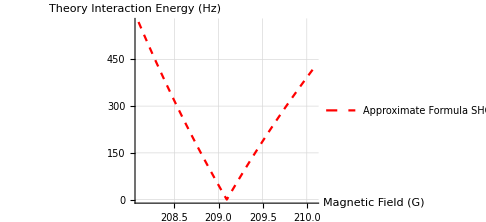

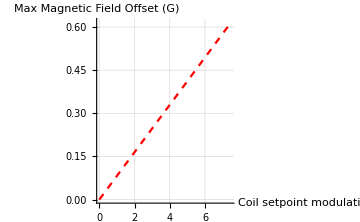

-Graphics-

```mathematica
pltApproxUFormula = Plot[{ApproxInteractionFreqGuess[B]},{B,BCross-1,BCross+1},AxesLabel -> {"Magnetic Field (G)", "Theory Interaction Energy (Hz)"},
PlotStyle -> {Red, Dashed}, PlotRange ->{{BCross-1,BCross+1},All},GridLines -> Automatic,
PlotLegends -> {"Approximate Formula SHO interaction"}, ImageSize ->Medium]
pltImpliedFeshbachFieldAmp=Plot[{FBFieldInGaussPermVOffset *mV},{mV,0,7.5},AxesLabel -> {"Coil setpoint modulation (mV)", "Max Magnetic Field Offset (G)"},
PlotStyle -> {Red, Dashed}, PlotRange ->All,GridLines -> Automatic, ImageSize -> Medium]
pltImpliedFeshbachInteractionAmp=Plot[{ApproxInteractionFreqGuess[BCross +FBFieldInGaussPermVOffset *mV],ApproxInteractionFreqGuess[BCross -FBFieldInGaussPermVOffset *mV]},{mV,0,7.5},AxesLabel -> {"Coil setpoint modulation (mV)", "Theory Static Interaction Energy (Hz)"}, PlotLabels -> {"Positive offset", "Negative offset"}, PlotRange ->All,GridLines -> Automatic, ImageSize -> Medium]
```

```mathematica
{{0, Subscript[Ω, staticGap]/2},{Subscript[Ω, staticGap]/2,0}} // MatrixForm
```

(0 | Ω_staticGap/2
Ω_staticGap/2 | 0)

```mathematica
({{0, Subscript[Ω, staticGap]/2}, {Subscript[Ω, staticGap]/2, 0}}) 
({{0, Subscript[Ω, staticGap]/2 Cos[ω t]}, {Subscript[Ω, staticGap]/2 Cos[ω t], 0}}) (*Make it oscillate with that static gap amplitude from + to minus (ie modulation of 1.25 mV goes from +1.25 mV to -1.25 mV*)
({{0, Subscript[Ω, staticGap]/2 ⅇ^(-ⅈ ω t)/2}, {Subscript[Ω, staticGap]/2 ⅇ^(+ⅈ ω t)/2, 0}}) (*rotating wave approximation*)
({{0, Subscript[Ω, staticGap]/4}, {Subscript[Ω, staticGap]/4, 0}}) (*In rotating frame *)
(*Thus the energy gap in the rotating frame is half the static gap corresponding to the maximum energy difference produced by the coil at it's maximum amplitude*)

Subscript[Ω, RabiEffective] = Subscript[Ω, staticGap]/2
```

{{0,Ω_staticGap/2},{Ω_staticGap/2,0}}

{{0,1/2 Cos[t ω] Ω_staticGap},{1/2 Cos[t ω] Ω_staticGap,0}}

{{0,1/4 ⅇ^(-ⅈ t ω) Ω_staticGap},{1/4 ⅇ^(ⅈ t ω) Ω_staticGap,0}}

{{0,Ω_staticGap/4},{Ω_staticGap/4,0}}

Ω_staticGap/2

```mathematica
expPrelimRabiData = {{7.5,140.65}, {2.5, 47.422}, {1.25, 23.898}, {0.65, 12.232}, {0.325,6.283},{0.1625, 3.090} };
pltPrelimRabiData = ListPlot[expPrelimRabiData,  PlotRange ->{{0.1,7.7},{1,152}}, ScalingFunctions -> {"Log", "Log"}];
pltImpliedFeshbachInteractionRabiRate=Plot[{1/2(ApproxInteractionFreqGuess[BCross +FBFieldInGaussPermVOffset *mV]/2+ApproxInteractionFreqGuess[BCross -FBFieldInGaussPermVOffset *mV]/2),ApproxInteractionFreqGuess[BCross +FBFieldInGaussPermVOffset *mV]/2,ApproxInteractionFreqGuess[BCross -FBFieldInGaussPermVOffset *mV]/2},{mV,0.1,7.7},AxesLabel -> {"Coil setpoint modulation (mV)", "Theory Rabi oscillation rate (Hz)"}, PlotLabels -> {"Average of pos/neg offset","Positive offset", "Negative offset"},
 PlotRange ->{{0.1,7.5},{1,152}},GridLines -> Automatic, ImageSize ->Large, ScalingFunctions -> {"Log", "Log"}];
Show[{pltImpliedFeshbachInteractionRabiRate,pltPrelimRabiData}]
expPrelimRabiData = {{7.5,140.65}, {2.5, 47.422}, {1.25, 23.898}, {0.65, 12.232}, {0.325,6.283},{0.1625, 3.090} };
pltPrelimRabiData = ListPlot[expPrelimRabiData,  PlotRange ->{{0.1,7.7},{1,152}}];
pltImpliedFeshbachInteractionRabiRate=Plot[{1/2(ApproxInteractionFreqGuess[BCross +FBFieldInGaussPermVOffset *mV]/2+ApproxInteractionFreqGuess[BCross -FBFieldInGaussPermVOffset *mV]/2),ApproxInteractionFreqGuess[BCross +FBFieldInGaussPermVOffset *mV]/2,ApproxInteractionFreqGuess[BCross -FBFieldInGaussPermVOffset *mV]/2},{mV,0.1,7.5},AxesLabel -> {"Coil setpoint modulation (mV)", "Theory Rabi oscillation rate (Hz)"}, PlotLabels -> {"Average of pos/neg offset","Positive offset", "Negative offset"},
 PlotRange ->{{0.1,7.7},{1,152}},GridLines -> Automatic, ImageSize ->Large];
Show[{pltImpliedFeshbachInteractionRabiRate,pltPrelimRabiData}]
```

-Graphics-

-Graphics-

```mathematica
(*Compare exact theory and approximate theory at small interactions, they agree very well, so just use approximate theory. *)
Plot[{(1/2 Abs[(E0C2R[BCross +FBFieldInGaussPermVOffset *mV]-(E0+2))ωPar/(2π)-(E2C0R[BCross +FBFieldInGaussPermVOffset *mV]-(E0+2))ωPar/(2π)]+1/2 Abs[(E0C2R[BCross -FBFieldInGaussPermVOffset *mV]-(E0+2))ωPar/(2π)-(E2C0R[BCross -FBFieldInGaussPermVOffset *mV]-(E0+2))ωPar/(2π)])/2,1/2 Abs[(E0C2R[BCross +FBFieldInGaussPermVOffset *mV]-(E0+2))ωPar/(2π)-(E2C0R[BCross +FBFieldInGaussPermVOffset *mV]-(E0+2))ωPar/(2π)],
1/2 Abs[(E0C2R[BCross -FBFieldInGaussPermVOffset *mV]-(E0+2))ωPar/(2π)-(E2C0R[BCross -FBFieldInGaussPermVOffset *mV]-(E0+2))ωPar/(2π)],
1/2(ApproxInteractionFreqGuess[BCross +FBFieldInGaussPermVOffset *mV]/2+ApproxInteractionFreqGuess[BCross -FBFieldInGaussPermVOffset *mV]/2),ApproxInteractionFreqGuess[BCross +FBFieldInGaussPermVOffset *mV]/2,ApproxInteractionFreqGuess[BCross -FBFieldInGaussPermVOffset *mV]/2},{mV,0.1,7.5}, PlotStyle -> {Automatic,Automatic, Automatic, Dashed, Dashed, Dashed},AxesLabel -> {"Coil setpoint modulation (mV)", "Theory Rabi oscillation rate (Hz)"}, PlotLabels -> {"Average of pos/neg offset","Positive offset", "Negative offset"},
 PlotRange ->{{0.1,7.7},{1,152}},GridLines -> Automatic, ImageSize ->Large, PlotPoints -> 3]
```

NIntegrate::inumr: The integrand (3.85339 ⅇ^(1/2 (-4.35339+energy) t))/((1-ⅇ^(-3.85339 t)) √(1-ⅇ^-t))-1/t^(3/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/100000,100000}}.

NIntegrate::inumr: The integrand (3.85339 ⅇ^((-3.85339+1/2 (-4.35339+energy)) t))/((1-ⅇ^(-3.85339 t)) √(1-ⅇ^-t))-1/t^(3/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/100000,100000}}.

NIntegrate::inumr: The integrand (3.85339 ⅇ^(1/2 (-4.35339+energy) t))/((1-ⅇ^(-3.85339 t)) √(1-ⅇ^-t))-1/t^(3/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/100000,100000}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

-Graphics-

Now let’s generate the list of experimental values and theory implied interactions and magnetic field offsets in Gauss. 
	We will use the average of the positive and negative offset energies. 
	We will provide the energy gap of the two states at that offset field in the uncoupled case (no anharmonicity).

```mathematica
expFBModAmpsmV = {0.1, 0.1625, 0.325, 0.65, 1.25, 2.5, 7.5}
expFBFieldOffsetG = FBFieldInGaussPermVOffset*expFBModAmpsmV
expFBFieldTotalPlusG = BCross + expFBFieldOffsetG
expFBFieldTotalMinusG = BCross - expFBFieldOffsetG
thFBOffsetStaticIntEnergyHz  = (Map[ApproxInteractionFreqGuess,expFBFieldTotalPlusG]/2+Map[ApproxInteractionFreqGuess,expFBFieldTotalMinusG ]/2)/2
```

{0.1,0.1625,0.325,0.65,1.25,2.5,7.5}

{0.0082342,0.0133806,0.0267612,0.0535223,0.102928,0.205855,0.617565}

{209.102,209.107,209.121,209.148,209.197,209.3,209.712}

{209.086,209.081,209.067,209.04,208.991,208.888,208.476}

{2.01039,3.26688,6.53385,13.0685,25.1367,50.3068,151.977}

```mathematica
Export["rabiOscillationMagnitudeCalibrations.txt", {expFBModAmpsmV,expFBFieldOffsetG,thFBOffsetStaticIntEnergyHz,expFBFieldTotalPlusG ,expFBFieldTotalMinusG}, "Table"]
```

rabiOscillationMagnitudeCalibrations.txt

#### Exploration (junk stuff)

```mathematica
(*Check for a particular B field that leads to 36 kHz*)
 Table[{B,Abs[(E0C2R[B]-(E0+2))ωPar/(2π)-(E2C0R[B]-(E0+2))ωPar/(2π)]}, {B,Table[bbb,{bbb,202.5,202.6,0.01}]}]
```

NIntegrate::inumr: The integrand (3.85391 ⅇ^(1/2 (-4.35391+energy) t))/((1-ⅇ^(-3.85391 t)) √(1-ⅇ^-t))-1/t^(3/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/100000,100000}}.

NIntegrate::inumr: The integrand (3.85391 ⅇ^((-3.85391+1/2 (-4.35391+energy)) t))/((1-ⅇ^(-3.85391 t)) √(1-ⅇ^-t))-1/t^(3/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/100000,100000}}.

NIntegrate::inumr: The integrand (3.85391 ⅇ^(1/2 (-4.35391+energy) t))/((1-ⅇ^(-3.85391 t)) √(1-ⅇ^-t))-1/t^(3/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/100000,100000}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{{202.5,37002.4},{202.51,36660.4},{202.52,36321.8},{202.53,35986.6},{202.54,35654.6},{202.55,35326.},{202.56,35000.7},{202.57,34678.6},{202.58,34359.8},{202.59,34044.1},{202.6,33731.7}}

```mathematica
(*Explore the B field setpoint and actual values for figure 4, and try to understand the noise*)
BsetVals= {209.126, 207, 204.25, 202.1}
BactualVals= Bactual[BsetVals]
numBs = Length[tabOfFieldSetpoints];
datToInterp =Table[{ tabOfFieldSetpoints[[jj]],tabOfThBareDifference [[jj]]}, {jj,1,numBs}];
ListPlot[datToInterp]
deltaEofBInterp = Interpolation[datToInterp]
deltaEofBInterp[203]

epsB = 0.01;
energySlopedB[BB_] :=Abs[(deltaEofBInterp[BB + epsB/2]-deltaEofBInterp[BB - epsB/2])/epsB]
Plot[energySlopedB[B], {B,202, 212}, PlotRange -> All]
dEdBVals= energySlopedB[BactualVals]
```

{209.126,207,204.25,202.1}

{209.094,206.976,204.235,202.091}

-Graphics-

Interpolation::innd: First argument in {} does not contain a list of data and coordinates.

Interpolation[{}]

Interpolation[{}][203]

-Graphics-

100. Abs[-Interpolation[{}][{209.089,206.971,204.23,202.086}]+Interpolation[{}][{209.099,206.981,204.24,202.096}]]

```mathematica
1/(dEdBVals/dEdBVals[[4]])
```

{105.46,45.5209,8.0855,1.}

### Anharmonic Correction Calculations

#### Summary of results

Ultimately, we expect something of the following form. We will derive these expressions below

```mathematica
(*Analytic values from calculations below*)
c0 = -1/16;
c1 = -9/16;
c2 = -35/16;
ϵ0eff[VV_] := (2 √VV(1/2)-1/4) + c0/(√VV)
ϵ1eff[VV_] := (2 √VV(1/2+1)-1-1/4) + c1/(√VV)
ϵ2eff[VV_] := (2 √VV(1/2+2)-3-1/4) + c2/(√VV)
```

Fully general formula for the nth state is derived below.
Anharmonic qubit splitting is therefore Er*(1+9/(8 √VVt)) including the next order corrections, where VVt is the lattice depth in Er units.
The harmonic oscillator energy splitting is just 2 √VV Er though. 

Let’s quickly calculate the scale of relative fluctuation if you use the recoil qubit as opposed to the harmonic qubit.

```mathematica
harmSens=D[2 √VV,VV]/(2 √VV) (*Harmonic qubit*)
anharmSens=D[9/(8 √VV),VV]/1(*recoil qubit*)
anharmSens/harmSens
```

1/(2 VV)

-9/(16 VV^(3/2))

-9/(8 √VV)

#### Direct calculation of 4th and 6th order terms in perturbation theory

```mathematica
Series[V Sin[π z/a]^2, {z,0,6}]
(*(π^2 V z^2)/a^2 = 1/2 m ω^2 z^2, or V = 1/2 m ω^2 a^2/π^2*)
```

(π^2 V z^2)/a^2-((π^4 V) z^4)/(3 a^4)+(2 π^6 V z^6)/(45 a^6)+O[z]^7

```mathematica
% /. V -> 1/2 m ω^2 a^2/π^2 (*plug in for omega in terms of V*)
```

1/2 m ω^2 z^2-((m π^2 ω^2) z^4)/(6 a^2)+(m π^4 ω^2 z^6)/(45 a^4)+O[z]^7

```mathematica
(*Or in other words ω is proportional to sqrt V, and since V = VV Er when we plug in Er units, this is saying that
 VV Er π^2/a^2 = 1/2 m ω^2 or ω^2 = VV (ℏ^2 π^2)/(2 m a^2)/(1/2 m a^2/π^2)
ℏ ω = √VV √((π^4 ℏ^4)/(a^4 m^2)) = 2 Er √VV
*)
```

```mathematica
(*now let's put things in SHO length units*)
FullSimplify[1/2 m ω^2 z^2-((m π^2 ω^2) z^4)/(6 a^2)+(m π^4 ω^2 z^6)/(45 a^4)/. z ->( z0 √(ℏ/(m ω)))]
```

-(1.82937×10^-68 z0^4)/(a^2 m)+(2.53872×10^-102 z0^6)/(a^4 m^2 ω)+5.27286×10^-35 z0^2 ω

```mathematica
(*subtract off lowest order term*)
FullSimplify[1/90 z0^2 ℏ (45 ω-(15 π^2 z0^2 ℏ)/(a^2 m)+(2 π^4 z0^4 ℏ^2)/(a^4 m^2 ω)) - 1/2 z0^2 ℏ ω]
```

(2.53872×10^-102 z0^6-1.82937×10^-68 a^2 m z0^4 ω)/(a^4 m^2 ω)

```mathematica
(*Quartic term*)
-(π^2 z0^4 ℏ^2)/(6 a^2 m)
(*Sixth order term*)
(π^4 z0^6 ℏ^3)/(45 a^4 m^2 ω)
```

-(1.82937×10^-68 z0^4)/(a^2 m)

(2.53872×10^-102 z0^6)/(a^4 m^2 ω)

```mathematica
(*Quartic term*)
-Er/3 z0^4
(*Sixth order term*)
(2^2 z0^6 ℏ^4 π^4)/(45 2^2 a^4 m^2)1/(ℏ ω) = 4/45(ℏ^4 π^4)/(2^2 a^4 m^2)1/(ℏ ω)  z0^6 = 4/45 Er Er/(ℏ ω)z0^6
4/45 Er Er/(ℏ ω)z0^6
```

-(Er z0^4)/3

Set::write: Tag Times in (4 3.01192×10^-135 z0^6 9.48252×10^33)/(45 (a^4 m^2) ω) is Protected.

Set::write: Tag Times in ((2.67727×10^-136 z0^6) 9.48252×10^33)/((a^4 m^2) ω) is Protected.

(8.42891×10^32 Er^2 z0^6)/ω

(8.42891×10^32 Er^2 z0^6)/ω

Also note that l^2 π^2/a^2 is precisely 2 Er, in harmonic oscillator energy units (ie it is l^2 π^2/a^2 =2 Er/(ℏ ω) ), so we can alternatively write these as 

Another way of saying this is to put ℏ ω = 2*Er * √V_inErUnits, so that in terms of V and Er to get Er/(ℏ ω) = 1/(2 √VV_inErUnits) and

```mathematica
(*Quartic term*)
Er(-1/3)z0^4 = Er(-1/3)1/4(a + SuperDagger[a])^4  = Er(-1/12)(a + SuperDagger[a])^4 
(*Sixth order term*)
Er (2/(45 √V)) z0^6=Er (2/(45 √V)) 1/8(a + SuperDagger[a])^6 = Er (1/(180 √V))(a + SuperDagger[a])^6
```

Set::write: Tag Times in -(Er (a+a^†)^4)/(3 4) is Protected.

Set::write: Tag Times in -(Er z0^4)/3 is Protected.

-1/12 Er (a+a^†)^4

Set::write: Tag Times in (Er 2 (a+a^†)^6)/(8 (45 √V)) is Protected.

Set::write: Tag Times in (Er 2 z0^6)/(45 √V) is Protected.

(Er (a+a^†)^6)/(180 √V)

We need expectation values of products of a and adagger up to 4th order, or 6th order. 
I don’t see a particularly good way to get this from scratch other than converting everything to normal order.

#### Expressing operators in normal order

```mathematica
(a + SuperDagger[a])^2 =a^2 + SuperDagger[a]^2 + 2 SuperDagger[a] a + 1;
(a + SuperDagger[a])^4 = ((a + SuperDagger[a])^2)^2 =(a^2 + SuperDagger[a]^2 + 2 SuperDagger[a] a + 1)^2 = a^4 + SuperDagger[a]^4 + (2 SuperDagger[a] a)^2 + 1 + (2*(a^2 + SuperDagger[a]^2 + 2 SuperDagger[a] a ) + (SuperDagger[a]^2 + 2 SuperDagger[a] a )a^2  + a^2 (SuperDagger[a]^2 + 2 SuperDagger[a] a )+2 SuperDagger[a]^2 SuperDagger[a] a + 2 SuperDagger[a] a SuperDagger[a]^2);
 = a^4 + SuperDagger[a]^4 + 1 + 2 a^2 + 2 SuperDagger[a]^2 + 4 SuperDagger[a] a  + SuperDagger[a]^2 a^2 +  2 (SuperDagger[a] a^3   +SuperDagger[a]^3 a) + 2 SuperDagger[a] a SuperDagger[a]^2+4 SuperDagger[a] a SuperDagger[a] a +  a^2 SuperDagger[a]^2 + 2 a^2  SuperDagger[a] a 
 = a^4 + SuperDagger[a]^4 + 1 + 2 a^2 + 2 SuperDagger[a]^2 + 4 SuperDagger[a] a  + SuperDagger[a]^2 a^2 +  2 (SuperDagger[a] a^3   +SuperDagger[a]^3 a) + 2 SuperDagger[a](1+SuperDagger[a] a )SuperDagger[a]+4 SuperDagger[a](1+SuperDagger[a] a )a +  a (1+SuperDagger[a] a )SuperDagger[a] + 2a(1+SuperDagger[a] a )a 
 = a^4 + SuperDagger[a]^4 + 1 + 2 a^2 + 2 SuperDagger[a]^2 + 4 SuperDagger[a] a  + SuperDagger[a]^2 a^2 +  2 (SuperDagger[a] a^3   +SuperDagger[a]^3 a) + 2 SuperDagger[a] SuperDagger[a]+ 2 SuperDagger[a] SuperDagger[a] a SuperDagger[a]+4 SuperDagger[a] a +4 SuperDagger[a] SuperDagger[a] a a +  a SuperDagger[a] + a SuperDagger[a] a SuperDagger[a] + 2a a + 2a SuperDagger[a] a a 
 = a^4 + SuperDagger[a]^4 + 1 + 2 a^2 + 2 SuperDagger[a]^2 + 4 SuperDagger[a] a  + SuperDagger[a]^2 a^2 +  2 (SuperDagger[a] a^3   +SuperDagger[a]^3 a) + 2 SuperDagger[a]^2+ 2 SuperDagger[a] SuperDagger[a](1+SuperDagger[a] a )+4 SuperDagger[a] a +4 SuperDagger[a] SuperDagger[a] a a +  (1+SuperDagger[a] a )+ (1+SuperDagger[a] a )(1+SuperDagger[a] a ) + 2 a^2 + 2(1+SuperDagger[a] a )a a 
 = a^4 + SuperDagger[a]^4 + 1 + 2 a^2 + 2 SuperDagger[a]^2 + 4 SuperDagger[a] a  + SuperDagger[a]^2 a^2 +  2 (SuperDagger[a] a^3   +SuperDagger[a]^3 a) + 2 SuperDagger[a]^2+ 2 SuperDagger[a] SuperDagger[a]+2 SuperDagger[a] SuperDagger[a] SuperDagger[a] a +4 SuperDagger[a] a +4 SuperDagger[a] SuperDagger[a] a a +  1+SuperDagger[a] a + 1 +2 SuperDagger[a] a + SuperDagger[a] a SuperDagger[a] a+ 2 a^2 + 2a a  + 2 SuperDagger[a] a a a 
 = a^4 + SuperDagger[a]^4 + 1 + 2 a^2 + 2 SuperDagger[a]^2 + 4 SuperDagger[a] a  + SuperDagger[a]^2 a^2 +  2 (SuperDagger[a] a^3   +SuperDagger[a]^3 a) + 2 SuperDagger[a]^2+ 2 SuperDagger[a] SuperDagger[a]+2 SuperDagger[a] SuperDagger[a] SuperDagger[a] a +4 SuperDagger[a] a +4 SuperDagger[a] SuperDagger[a] a a +  1+SuperDagger[a] a + 1 +2 SuperDagger[a] a + SuperDagger[a](1+SuperDagger[a] a )a+ 2 a^2 + 2a a  + 2 SuperDagger[a] a a a 
 = a^4 + SuperDagger[a]^4 + 1 + 2 a^2 + 2 SuperDagger[a]^2 + 4 SuperDagger[a] a  + SuperDagger[a]^2 a^2 +  2 (SuperDagger[a] a^3   +SuperDagger[a]^3 a) + 4 SuperDagger[a]^2+2 SuperDagger[a]^3 a +4 SuperDagger[a] a +4 SuperDagger[a]^2 a^2  +  2+SuperDagger[a] a +2 SuperDagger[a] a + SuperDagger[a] a+SuperDagger[a]^2 a^2 + 4 a^2   + 2 SuperDagger[a] a^3   (*Now consolidate terms with like powers*)
 = a^4 + SuperDagger[a]^4 + 1 + 2 a^2 + 2 SuperDagger[a]^2 + 4 SuperDagger[a] a  + SuperDagger[a]^2 a^2 +  2 (SuperDagger[a] a^3   +SuperDagger[a]^3 a) + 4 (SuperDagger[a]^2+a^2)+2 (SuperDagger[a]^3 a +SuperDagger[a] a^3)+8 SuperDagger[a] a +5 SuperDagger[a]^2 a^2+2
 = a^4 + SuperDagger[a]^4 + 3+ 6( a^2 + SuperDagger[a]^2) + 12 SuperDagger[a] a  +6 SuperDagger[a]^2 a^2 +  4 (SuperDagger[a] a^3   +SuperDagger[a]^3 a)
```

Set::write: Tag Power in (a+a^†)^2 is Protected.

Set::write: Tag Power in (1+a^2+2 a a^†+(a^†)^2)^2 is Protected.

Set::write: Tag Power in ((a+a^†)^2)^2 is Protected.

Set::write: Tag Power in (a+a^†)^4 is Protected.

General::stop: Further output of Set::write will be suppressed during this calculation.

```mathematica
Expand[ a^4 + SuperDagger[a]^4 + 3+ 6( a^2 + SuperDagger[a]^2) + 12 SuperDagger[a] a  +6 SuperDagger[a]^2 a^2 +  4 (SuperDagger[a] a^3   +SuperDagger[a]^3 a) ]
```

3+6 a^2+a^4+12 a a^†+4 a^3 a^†+6 (a^†)^2+6 a^2 (a^†)^2+4 a (a^†)^3+(a^†)^4

```mathematica
3+6 a^2+a^4+12 a SuperDagger[a]+4 a^3 SuperDagger[a]+6 (SuperDagger[a])^2+6 a^2 (SuperDagger[a])^2+4 a (SuperDagger[a])^3+(SuperDagger[a])^4
(*put it back in normal order *)
3+(a^4+(SuperDagger[a])^4)+6 (a^2+(SuperDagger[a])^2)+4( SuperDagger[a] a^3+(SuperDagger[a])^3 a) +6 (SuperDagger[a])^2 a^2 +12 SuperDagger[a] a
```

3+6 a^2+a^4+12 a a^†+4 a^3 a^†+6 (a^†)^2+6 a^2 (a^†)^2+4 a (a^†)^3+(a^†)^4

3+a^4+12 a a^†+6 a^2 (a^†)^2+(a^†)^4+6 (a^2+(a^†)^2)+4 (a^3 a^†+a (a^†)^3)

Note that this is symmetric in a and adagger.
Now we need  (a + a^†)^6

```mathematica
=( a^4 + SuperDagger[a]^4 + 3+ 6( a^2 + SuperDagger[a]^2) + 12 SuperDagger[a] a  +6 SuperDagger[a]^2 a^2 +  4 (SuperDagger[a] a^3   +SuperDagger[a]^3 a) )(a^2 + SuperDagger[a]^2 + 2 SuperDagger[a] a + 1)
= ( a^4 + SuperDagger[a]^4 + 3+ 6( a^2 + SuperDagger[a]^2) + 12 SuperDagger[a] a  +6 SuperDagger[a]^2 a^2 +  4 (SuperDagger[a] a^3   +SuperDagger[a]^3 a) )(a^2 + 1) + ( a^4 + SuperDagger[a]^4 + 3+ 6( a^2 + SuperDagger[a]^2) + 12 SuperDagger[a] a  +6 SuperDagger[a]^2 a^2 +  4 (SuperDagger[a] a^3   +SuperDagger[a]^3 a) )(SuperDagger[a]^2 + 2 SuperDagger[a] a )
(*Now we have to bring the adagger terms through again... Not going to be fun. 
[a^n, a^†] = n a^(n-1) I think
[a^n, (a^†)^2] = [a^n, a^†] a^† + a^†a^n a^† - (a^†)^2 a^n =  [a^n, a^†] a^† + a^†[a^n, a^†] = n(a^(n-1) a^† + a^† a^(n-1))= n((n-1)a^(n-2) + 2 a^† a^(n-1))= (n(n-1)+2n a^†a)a^(n-2) 
^if n is 2 or larger. If n is 1 then it is  a (a^†)^2 -  (a^†)^2 a  =  a^† +  a^†a a^†-  (a^†)^2 a = a^† +  a^†(a a^†-  a^† a)  = 2 a^† 
*)
= ( a^4 + SuperDagger[a]^4 + 3+ 6( a^2 + SuperDagger[a]^2) + 12 SuperDagger[a] a  +6 SuperDagger[a]^2 a^2 +  4 (SuperDagger[a] a^3   +SuperDagger[a]^3 a) )(a^2 + 1) 
+ ( SuperDagger[a]^4 + 3+ 6 SuperDagger[a]^2 )(SuperDagger[a]^2 + 2 SuperDagger[a] a )
+ ( a^4 + 6 a^2  + 12 SuperDagger[a] a  +6 SuperDagger[a]^2 a^2 +  4 (SuperDagger[a] a^3   +SuperDagger[a]^3 a) )(SuperDagger[a]^2 + 2 SuperDagger[a] a )
(*Now use the commutation relations on the lower stuff*)
= ( a^4 + SuperDagger[a]^4 + 3+ 6( a^2 + SuperDagger[a]^2) + 12 SuperDagger[a] a  +6 SuperDagger[a]^2 a^2 +  4 (SuperDagger[a] a^3   +SuperDagger[a]^3 a) )(a^2 + 1) + ( SuperDagger[a]^4 + 3+ 6 SuperDagger[a]^2 )(SuperDagger[a]^2 + 2 SuperDagger[a] a )
+ ( a^4 + 6 a^2  + 12 SuperDagger[a] a  +6 SuperDagger[a]^2 a^2 +  4 (SuperDagger[a] a^3   +SuperDagger[a]^3 a) )SuperDagger[a]^2
+ 2( a^4 + 6 a^2  + 12 SuperDagger[a] a  +6 SuperDagger[a]^2 a^2 +  4 (SuperDagger[a] a^3   +SuperDagger[a]^3 a) ) SuperDagger[a] a 

= ( a^4 + SuperDagger[a]^4 + 3+ 6( a^2 + SuperDagger[a]^2) + 12 SuperDagger[a] a  +6 SuperDagger[a]^2 a^2 +  4 (SuperDagger[a] a^3   +SuperDagger[a]^3 a) )(a^2 + 1) + ( SuperDagger[a]^4 + 3+ 6 SuperDagger[a]^2 )(SuperDagger[a]^2 + 2 SuperDagger[a] a )
+ SuperDagger[a]^2( a^4 + 6 a^2  + 12 SuperDagger[a] a  +6 SuperDagger[a]^2 a^2 +  4 (SuperDagger[a] a^3   +SuperDagger[a]^3 a) ) + [( a^4 + 6 a^2  + 12 SuperDagger[a] a  +6 SuperDagger[a]^2 a^2 +  4 (SuperDagger[a] a^3   +SuperDagger[a]^3 a) ),SuperDagger[a]^2]
+ 2 SuperDagger[a]( a^4 + 6 a^2  + 12 SuperDagger[a] a  +6 SuperDagger[a]^2 a^2 +  4 (SuperDagger[a] a^3   +SuperDagger[a]^3 a) ) a + 2[( a^4 + 6 a^2  + 12 SuperDagger[a] a  +6 SuperDagger[a]^2 a^2 +  4 (SuperDagger[a] a^3   +SuperDagger[a]^3 a) ), SuperDagger[a]]a 

= ( a^4 + SuperDagger[a]^4 + 3+ 6( a^2 + SuperDagger[a]^2) + 12 SuperDagger[a] a  +6 SuperDagger[a]^2 a^2 +  4 (SuperDagger[a] a^3   +SuperDagger[a]^3 a) )(a^2 + 1) + ( SuperDagger[a]^4 + 3+ 6 SuperDagger[a]^2 )(SuperDagger[a]^2 + 2 SuperDagger[a] a )
+ SuperDagger[a]^2( a^4 + 6 a^2  + 12 SuperDagger[a] a  +6 SuperDagger[a]^2 a^2 +  4 (SuperDagger[a] a^3   +SuperDagger[a]^3 a) ) + 2 SuperDagger[a]( a^4 + 6 a^2  + 12 SuperDagger[a] a  +6 SuperDagger[a]^2 a^2 +  4 (SuperDagger[a] a^3   +SuperDagger[a]^3 a) ) a 
+ [( a^4 +  4 SuperDagger[a] a^3+ 6(1+SuperDagger[a]^2)a^2  + (12 SuperDagger[a]+4 SuperDagger[a]^3 )a),SuperDagger[a]^2]+ 2[( a^4 +  4 SuperDagger[a] a^3+ 6(1+SuperDagger[a]^2)a^2  + (12 SuperDagger[a]+4 SuperDagger[a]^3 )a ), SuperDagger[a]]a 

= ( a^4 + SuperDagger[a]^4 + 3+ 6( a^2 + SuperDagger[a]^2) + 12 SuperDagger[a] a  +6 SuperDagger[a]^2 a^2 +  4 (SuperDagger[a] a^3   +SuperDagger[a]^3 a) )(a^2 + 1) + ( SuperDagger[a]^4 + 3+ 6 SuperDagger[a]^2 )(SuperDagger[a]^2 + 2 SuperDagger[a] a )
+ SuperDagger[a]^2( a^4 + 6 a^2  + 12 SuperDagger[a] a  +6 SuperDagger[a]^2 a^2 +  4 (SuperDagger[a] a^3   +SuperDagger[a]^3 a) ) + 2 SuperDagger[a]( a^4 + 6 a^2  + 12 SuperDagger[a] a  +6 SuperDagger[a]^2 a^2 +  4 (SuperDagger[a] a^3   +SuperDagger[a]^3 a) ) a 
+ 2( 4 a^3 +  4 SuperDagger[a] 3 a^2+ 6(1+SuperDagger[a]^2)2a  + (12 SuperDagger[a]+4 SuperDagger[a]^3 )1 )a 
+ [a^4,SuperDagger[a]^2]+ 4 SuperDagger[a][a^3,SuperDagger[a]^2]+ 6(1+SuperDagger[a]^2)[a^2 ,SuperDagger[a]^2]+(12 SuperDagger[a]+4 SuperDagger[a]^3 )[a,SuperDagger[a]^2]

= ( a^4 + SuperDagger[a]^4 + 3+ 6( a^2 + SuperDagger[a]^2) + 12 SuperDagger[a] a  +6 SuperDagger[a]^2 a^2 +  4 (SuperDagger[a] a^3   +SuperDagger[a]^3 a) )(a^2 + 1) + ( SuperDagger[a]^4 + 3+ 6 SuperDagger[a]^2 )(SuperDagger[a]^2 + 2 SuperDagger[a] a )
+ SuperDagger[a]^2( a^4 + 6 a^2  + 12 SuperDagger[a] a  +6 SuperDagger[a]^2 a^2 +  4 (SuperDagger[a] a^3   +SuperDagger[a]^3 a) ) + 2 SuperDagger[a]( a^4 + 6 a^2  + 12 SuperDagger[a] a  +6 SuperDagger[a]^2 a^2 +  4 (SuperDagger[a] a^3   +SuperDagger[a]^3 a) ) a 
+ 2( 4 a^3 +  4 SuperDagger[a] 3 a^2+ 6(1+SuperDagger[a]^2)2a  + (12 SuperDagger[a]+4 SuperDagger[a]^3 )1 )a 
+ ((n(n-1)+2n SuperDagger[a] a)a^(n-2) /. n-> 4)+ 4 SuperDagger[a]((n(n-1)+2n SuperDagger[a] a)a^(n-2)/. n-> 3)+ 6(1+SuperDagger[a]^2)((n(n-1)+2n SuperDagger[a] a)a^(n-2)/. n-> 2)+(12 SuperDagger[a]+4 SuperDagger[a]^3 )(2 SuperDagger[a])
```

```mathematica
(*Result in normal order*)
Expand[( a^4 + SuperDagger[a]^4 + 3+ 6( a^2 + SuperDagger[a]^2) + 12 SuperDagger[a] a  +6 SuperDagger[a]^2 a^2 +  4 (SuperDagger[a] a^3   +SuperDagger[a]^3 a) )(a^2 + 1) + ( SuperDagger[a]^4 + 3+ 6 SuperDagger[a]^2 )(SuperDagger[a]^2 + 2 SuperDagger[a] a )+ SuperDagger[a]^2( a^4 + 6 a^2  + 12 SuperDagger[a] a  +6 SuperDagger[a]^2 a^2 +  4 (SuperDagger[a] a^3   +SuperDagger[a]^3 a) ) + 2 SuperDagger[a]( a^4 + 6 a^2  + 12 SuperDagger[a] a  +6 SuperDagger[a]^2 a^2 +  4 (SuperDagger[a] a^3   +SuperDagger[a]^3 a) ) a + 2( 4 a^3 +  4 SuperDagger[a] 3 a^2+ 6(1+SuperDagger[a]^2)2a  + (12 SuperDagger[a]+4 SuperDagger[a]^3 )1 )a + ((n(n-1)+2n SuperDagger[a] a)a^(n-2) /. n-> 4)+ 4 SuperDagger[a]((n(n-1)+2n SuperDagger[a] a)a^(n-2)/. n-> 3)+ 6(1+SuperDagger[a]^2)((n(n-1)+2n SuperDagger[a] a)a^(n-2)/. n-> 2)+(12 SuperDagger[a]+4 SuperDagger[a]^3 )(2 SuperDagger[a])]
```

15+45 a^2+15 a^4+a^6+90 a a^†+60 a^3 a^†+6 a^5 a^†+45 (a^†)^2+90 a^2 (a^†)^2+15 a^4 (a^†)^2+60 a (a^†)^3+20 a^3 (a^†)^3+15 (a^†)^4+15 a^2 (a^†)^4+6 a (a^†)^5+(a^†)^6

```mathematica
(*Lets check it's symmetric in a and adgg
NOTE THIS IS IN NORMAL ORDER, ie should be INTERPRETED/reordered in normal order*)
15+(a^6+(SuperDagger[a])^6)+15 (a^4+(SuperDagger[a])^4)+45 (a^2+(SuperDagger[a])^2)+6( a^5 SuperDagger[a]+ a (SuperDagger[a])^5)+15 (a^4 (SuperDagger[a])^2+a^2 (SuperDagger[a])^4)+60( a^3 SuperDagger[a]+a (SuperDagger[a])^3)+20 a^3 (SuperDagger[a])^3+90 a^2 (SuperDagger[a])^2+90 a SuperDagger[a]
(*Put it back in normal order*)
15+(a^6+(SuperDagger[a])^6)+15 (a^4+(SuperDagger[a])^4)+45 (a^2+(SuperDagger[a])^2)+6( SuperDagger[a] a^5 + (SuperDagger[a])^5 a)+15 ((SuperDagger[a])^2 a^4 +(SuperDagger[a])^4 a^2)+60( SuperDagger[a] a^3 +(SuperDagger[a])^3 a )+20 (SuperDagger[a])^3 a^3 +90(SuperDagger[a])^2 a^2 +90 SuperDagger[a] a 
(*So this is (a + adag)^6, but z0^6 is this divided by 2^3 = 8*)
```

15+a^6+90 a a^†+90 a^2 (a^†)^2+20 a^3 (a^†)^3+(a^†)^6+45 (a^2+(a^†)^2)+60 (a^3 a^†+a (a^†)^3)+15 (a^4+(a^†)^4)+15 (a^4 (a^†)^2+a^2 (a^†)^4)+6 (a^5 a^†+a (a^†)^5)

15+a^6+90 a a^†+90 a^2 (a^†)^2+20 a^3 (a^†)^3+(a^†)^6+45 (a^2+(a^†)^2)+60 (a^3 a^†+a (a^†)^3)+15 (a^4+(a^†)^4)+15 (a^4 (a^†)^2+a^2 (a^†)^4)+6 (a^5 a^†+a (a^†)^5)

#### Result for expectation value of new energy terms (first order correction due to these terms), still not including change in state and resulting energy change in original hamiltonian terms

```mathematica
(*Fourth order term*)
Er (-1/12)(3+(a^4+(SuperDagger[a])^4)+6 (a^2+(SuperDagger[a])^2)+4( SuperDagger[a] a^3+(SuperDagger[a])^3 a) +6 (SuperDagger[a])^2 a^2 +12 SuperDagger[a] a )
```

-1/12 Er (3+a^4+12 a a^†+6 a^2 (a^†)^2+(a^†)^4+6 (a^2+(a^†)^2)+4 (a^3 a^†+a (a^†)^3))

```mathematica
(*Sixth order term*)
Er 1/(180 √V)(15+(a^6+(SuperDagger[a])^6)+15 (a^4+(SuperDagger[a])^4)+45 (a^2+(SuperDagger[a])^2)+6( SuperDagger[a] a^5 + (SuperDagger[a])^5 a)+15 ((SuperDagger[a])^2 a^4 +(SuperDagger[a])^4 a^2)+60( SuperDagger[a] a^3 +(SuperDagger[a])^3 a )+20 (SuperDagger[a])^3 a^3 +90(SuperDagger[a])^2 a^2 +90 SuperDagger[a] a )
```

(Er (15+a^6+90 a a^†+90 a^2 (a^†)^2+20 a^3 (a^†)^3+(a^†)^6+45 (a^2+(a^†)^2)+60 (a^3 a^†+a (a^†)^3)+15 (a^4+(a^†)^4)+15 (a^4 (a^†)^2+a^2 (a^†)^4)+6 (a^5 a^†+a (a^†)^5)))/(180 √V)

Now let' s evaluate these for the nth harmonic oscillator state, what are their values? The only terms that matter are the ones that conserve excitation number, so let’s focus on those. 
	⟨n|Fourth|n⟩ = -Er/12⟨n|(3+6 (a^†)^2 a^2 +12 a^†a )|n⟩ 
	⟨n|Sixth|n⟩ = Er 1/(180 √V)⟨n|15+20 (a^†)^3 a^3 +90(a^†)^2 a^2 +90 a^†a|n⟩ 
	
	Generically, ⟨n|(a^†)^m a^m|n⟩  = (n!)/((n-m)!)? But only if n>=m.

```mathematica
FullSimplify[-Er/12(3+6 (nthState(nthState-1)) +12nthState )]
fourthOrderTermInEr[nthState_]:= 1/4 (-1-2 nthState (1+nthState))
fourthOrderTermInEr[0]
fourthOrderTermInEr[1]
fourthOrderTermInEr[2]
```

-1/4 Er (1+2 nthState (1+nthState))

-1/4

-5/4

-13/4

```mathematica
FullSimplify[Er 1/(180 √V)(15+20 (nthState(nthState-1)(nthState-2))+90(nthState(nthState-1)) +90 nthState)]
sixthOrderTermInEr[nthState_, VVDepthInEr_]:=(3+8 nthState+6 nthState^2+4 nthState^3)/(36 √VVDepthInEr)
sixthOrderTermInEr[0, VVt]
sixthOrderTermInEr[1, VVt]
sixthOrderTermInEr[2, VVt]
```

(Er (3+2 nthState (4+nthState (3+2 nthState))))/(36 √V)

1/(12 √VVt)

7/(12 √VVt)

25/(12 √VVt)

This is saying, in my notation above, that there are contributions to: c0 = 1/12, c1 = 7/12, and c2 = 25/12.

#### What about fourth order corrections due to coupling to off resonant states? ie V^2/delta terms? These should be the same order as the 6th order terms since they get another power of omega in the denominator.

```mathematica
(*Fourth order term*)
Er (-1/12)(3+(a^4+(SuperDagger[a])^4)+6 (a^2+(SuperDagger[a])^2)+4( SuperDagger[a] a^3+(SuperDagger[a])^3 a) +6 (SuperDagger[a])^2 a^2 +12 SuperDagger[a] a )
```

-1/12 Er (3+a^4+12 a a^†+6 a^2 (a^†)^2+(a^†)^4+6 (a^2+(a^†)^2)+4 (a^3 a^†+a (a^†)^3))

Now let' s evaluate these for the nth harmonic oscillator state to the mth, where m not equal != n, what are their values?
	Let’s get rid of the extra factor of Er for now.
	⟨m|Fourth|n⟩ = -1/12⟨m|(a^4+(a^†)^4)+6 (a^2+(a^†)^2)+4( a^†a^3+(a^†)^3 a)|n⟩ 
	These only matter for m = n+/-4, or 2
	
	These terms (in the brackets) are what? 
	n -> n+4
		(-1/12)√((n+1)(n+2)(n+3)(n+4))
	n -> n-4
		(-1/12)√(n (n-1)(n-2)(n-3))
	n -> n+2
		(-1/12)(6 √((n+1)(n+2))+4 √(n n (n+1)(n+2)))
	n -> n-2
		(-1/12)(6 √(n (n-1))+4 √(n (n-1)(n-2)(n-2)))

The second order correction in perturbation theory is Ω^2/(E -E')  = - Ω^2/Δ where E is the original state, so if you couple to a higher energy state, you get pushed down. Δ is E’- E
	So what are the effects of these various perturbations? 
	
	Remember omega is in Er units, so let’s put delta in Er units as well 
		ℏ ω = 2 √VV in Er units, which is easy, then the resulting perturbation is in units of Er. 
	
	n -> n+4
		Ω = -√((n+1)(n+2)(n+3)(n+4))/12
		Δ =  8√VV or in lab units  4ℏ ω
	n -> n-4
		Ω = -√(n (n-1)(n-2)(n-3))/12
		Δ = - 8√VV or in lab units  -4ℏ ω
	n -> n+2
		Ω =-(6 √((n+1)(n+2))+4 √(n n (n+1)(n+2)))/12
		Δ =  4√VV or in lab units  2ℏ ω
	n -> n-2
		Ω = -(6 √(n (n-1))+4 √(n (n-1)(n-2)(n-2)))/12
		Δ =  -4√VV or in lab units  -2ℏ ω

	Now let’s add them all together...

```mathematica
(*Second order corrections from 4th order term *)
FullSimplify[1/12^2((n+1)(n+2)(n+3)(n+4))/(-8 √VVVTest)+1/12^2((n)(n-1)(n-2)(n-3))/(8 √VVVTest)+(-(6 √((n+1)(n+2))+4 √(n n(n+1)(n+2)))/12)^2 1/(-4 √VVVTest)+(-(6 √(n (n-1))+4 √(n (n-1)(n-2)(n-2)))/12)^2 1/(4 √VVVTest)]
```

(n (-59+(21-34 n) n)+3 (-7+4 √((-1+n) n) √((-2+n)^2 (-1+n) n)-4 √((1+n) (2+n)) √(n^2 (1+n) (2+n))))/(144 √VVVTest)

```mathematica
(*We can simplify this a little further with the square roots combined manually*)
FullSimplify[(n (-59+(21-34 n) n)+3 (-7+4 (n-2)(n-1) n -4 (n+2)(n+1) n ))/(144 √VVVTest)]
```

-((1+2 n) (21+17 n (1+n)))/(144 √VVVTest)

```mathematica
fourthOrderTermCorrectionInEr[nthState_, VVDepthInEr_]:=-((1+2 nthState) (21+17 nthState (1+nthState)))/(144 √VVDepthInEr)
fourthOrderTermCorrectionInEr[0, VVDepthInEr]
fourthOrderTermCorrectionInEr[1, VVDepthInEr]
fourthOrderTermCorrectionInEr[2, VVDepthInEr]
```

-7/(48 √VVDepthInEr)

-55/(48 √VVDepthInEr)

-205/(48 √VVDepthInEr)

These are the second order perturbation theory corrections from the 4th order term in z in the hamiltonian.

#### Results combining all terms up to 1/√VVorder

```mathematica
FullSimplify[fourthOrderTermInEr[nnTest]+sixthOrderTermInEr[nnTest, VVt]+fourthOrderTermCorrectionInEr[nnTest, VVt] ]
FullSimplify[sixthOrderTermInEr[nnTest, VVt]+fourthOrderTermCorrectionInEr[nnTest, VVt] ]
```

(-1-3 nnTest-3 nnTest^2-2 nnTest^3-4 (1+2 nnTest (1+nnTest)) √VVt)/(16 √VVt)

-((1+2 nnTest) (1+nnTest+nnTest^2))/(16 √VVt)

```mathematica
(*Look at just the 1/√VV terms, ie ignore main 4th order*)
FullSimplify[sixthOrderTermInEr[nnTest, VVt]+fourthOrderTermCorrectionInEr[nnTest, VVt] ] /. nnTest -> 0
FullSimplify[sixthOrderTermInEr[nnTest, VVt]+fourthOrderTermCorrectionInEr[nnTest, VVt] ] /. nnTest -> 1
FullSimplify[sixthOrderTermInEr[nnTest, VVt]+fourthOrderTermCorrectionInEr[nnTest, VVt] ] /. nnTest -> 2
```

-1/(16 √VVt)

-9/(16 √VVt)

-35/(16 √VVt)

Overall the actual energy of the nth state is

```mathematica
ϵnth[nthState_, VVDepthInEr_]:= 2 √VVDepthInEr(1/2+nthState) +fourthOrderTermInEr[nthState]+sixthOrderTermInEr[nthState, VVDepthInEr]+fourthOrderTermCorrectionInEr[nthState,VVDepthInEr]
FullSimplify[ϵnth[nnTest, VVt]]
```

(-1-3 nnTest-3 nnTest^2-2 nnTest^3-4 (1+2 nnTest (1+nnTest)) √VVt+16 (1+2 nnTest) VVt)/(16 √VVt)

```mathematica
FullSimplify[ϵnth[0, VVt]]
FullSimplify[ϵnth[1, VVt]]
FullSimplify[ϵnth[2, VVt]]
```

-1/4-1/(16 √VVt)+√VVt

-5/4+(3 (-3+16 VVt))/(16 √VVt)

-13/4+(5 (-7+16 VVt))/(16 √VVt)

Look at the two states in the anharmonic qubit, and their difference

```mathematica
FullSimplify[ϵnth[1, VVt]+ϵnth[1, VVt]]
FullSimplify[ϵnth[2, VVt]+ϵnth[0, VVt]]
FullSimplify[(ϵnth[1, VVt]+ϵnth[1, VVt])- (ϵnth[2, VVt]+ϵnth[0, VVt])]
```

-5/2+(3 (-3+16 VVt))/(8 √VVt)

-7/2+(3 (-3+8 VVt))/(4 √VVt)

1+9/(8 √VVt)

Anharmonic qubit splitting is therefore Er*(1+9/(8 √VVt)) including the next order corrections, where VVt is the lattice depth in Er units.

#### Comparison to Mathieu equation.

To do :
	Get analytic solution for the energy eigenvalues at large depth? Or at least check what the width is somehow and make sure it is small.
	Double check lattice depth in z direction in its own Er units

Differential equation to solve is 
	-y''[x]ℏ^2/2m+VlatinEr*(ℏ^2 π^2)/(2 m a_z^2)((Cos[2 πx/a_z]+1)/2) y[x]==ℰ y[x]
	Then divide everything through by Er and put everything in terms of the lattice spacing length unit
	-y''[x]π^2+VlatinEr((Cos[2 πx]+1)/2) y[x]==ℰinEr y[x]

```mathematica
ClearAll[ℏ,m]
FullSimplify[DSolve[-y''[x] 1/π^2+VlatinEr((Cos[2 πx]+1)/2) y[x]==ℰinEr y[x],y[x],x]]
```

{{y[x]→C[1] MathieuC[-VlatinEr/2+ℰinEr,VlatinEr/4,π x]+C[2] MathieuS[-VlatinEr/2+ℰinEr,VlatinEr/4,π x]}}

That is, the Mathieu equation solution with 
	energy ϵ in Er units, 
	q parameter in Mathieu equation formula equal to  (1/4)×Lattice depth in Er units.

Delocalized solutions exist only for certain values of epsilon, where the resulting Mathieu solutions are not localized. Whether these solutions are localized  can be found by looking at the imaginary part of the characteristic exponent of the Mathieu equation, which is nonzero in the band gaps (leading to decay).  

So we want regions where the imaginary part IS IN FACT 0 (inside the bands) so that the solutions are delocalized.

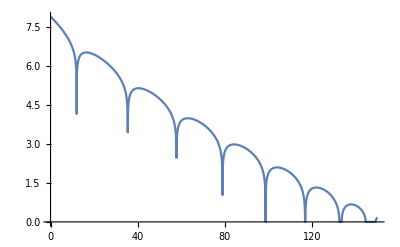

```mathematica
VV=150;
Plot[Im[MathieuCharacteristicExponent[ϵ-VV/2,VV/4]], {ϵ,0,VV}]
```

Indeed the solution for a potential depth of 150 Er is 2 (√VV)/2. √150.0 is around 12.24

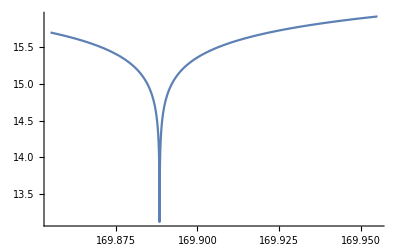

```mathematica
(*Zoom in on some large depth excited energy to see spread *)
VV = 1200;
Plot[Im[MathieuCharacteristicExponent[ϵ- VV/2,VV/4]], {ϵ,2 √VV(1/2+2)-3-1/4 - 0.1, 2 √VV(1/2+2)-3-1/4 -0.0}, PlotRange -> All]
```

Now let' s find the locations of these minima automatically and see how they compare to the supposed anharmonic corrections.

```mathematica
VV=150;
ϵ0 = ϵ /. FindMinimum [Im[MathieuCharacteristicExponent[ϵ- VV/2,VV/4]],{ϵ,2 √VV(1/2)}][[2]];
ϵ1 = ϵ /. FindMinimum [Im[MathieuCharacteristicExponent[ϵ- VV/2,VV/4]],{ϵ,2 √VV(1/2+1)}][[2]];
ϵ2 = ϵ /. FindMinimum [Im[MathieuCharacteristicExponent[ϵ- VV/2,VV/4]],{ϵ,2 √VV(1/2+2)}][[2]];
{ϵ0,ϵ1,ϵ2}
ϵ1-ϵ0
```

FindMinimum::sdprec: Line search unable to find a sufficient decrease in the function value with MachinePrecision digit precision.

{11.992,35.4409,57.7757}

23.4489

Let' s look at some expressions compared to the analytical values derived, then we can consider error/convergence.
Values of energies should be 2 √VV harmonic energy (so 1/2 3/2, and 5/2 times that), with shifts down by 1/4 Er, 1 + 1/4 Er, and 3 + 1/4 Er, and even higher order corrections beyond that.

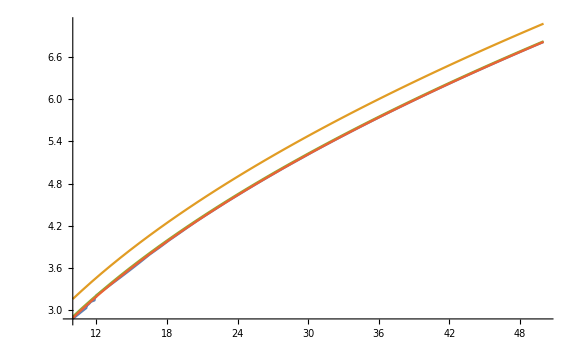
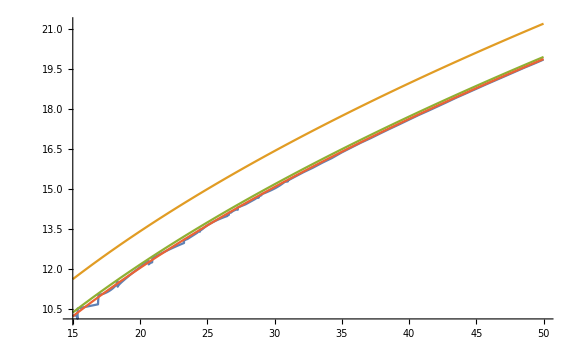
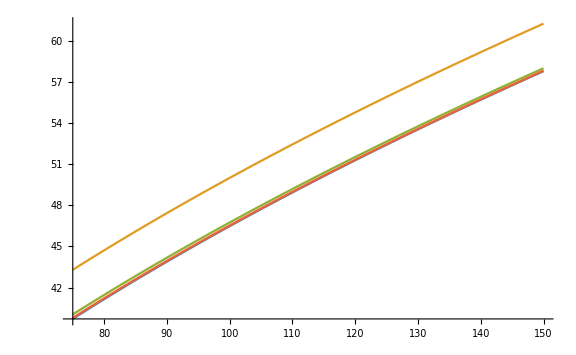

```mathematica
{(*First state, with a reasonable initial guess*)
Plot[{ϵ /. FindMinimum [Im[MathieuCharacteristicExponent[ϵ- VV/2,VV/4]],{ϵ,2 √VV(1/2)}][[2]],2 √VV(1/2),2 √VV(1/2)-1/4,2 √VV(1/2)-1/4-1/16 1/(√VV)},{VV,10,50}, WorkingPrecision -> 10, ImageSize -> Large],
(*Second state*)
Plot[{ϵ /. FindMinimum [Im[MathieuCharacteristicExponent[ϵ- VV/2,VV/4]],{ϵ,2 √VV(1/2+1)}][[2]],2 √VV(1/2+1),2 √VV(1/2+1)-1-1/4,2 √VV(1/2+1)-1-1/4-9/16 1/(√VV)},{VV,15,50}, WorkingPrecision -> 10, ImageSize -> Large],
(*Third state*)
Plot[{ϵ /. FindMinimum [Im[MathieuCharacteristicExponent[ϵ- VV/2,VV/4]],{ϵ,2 √VV(1/2+2)}][[2]],2 √VV(1/2+2),2 √VV(1/2+2)-3-1/4,2 √VV(1/2+2)-3-1/4-35/16 1/(√VV)},{VV,75,150}, WorkingPrecision -> 16, ImageSize -> Large]
}
```

Now let' s subtract off the formula with the fourth order corrections, and with the 6th order corrections

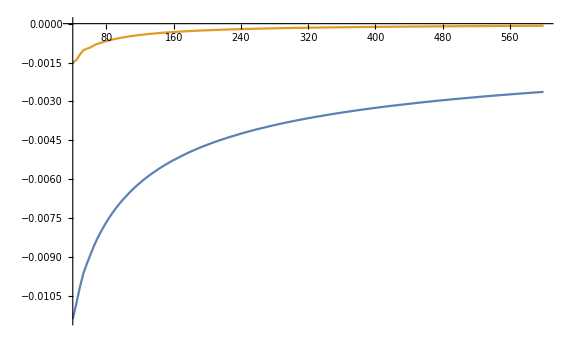
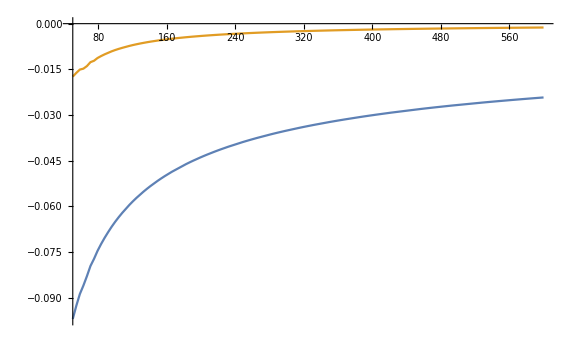
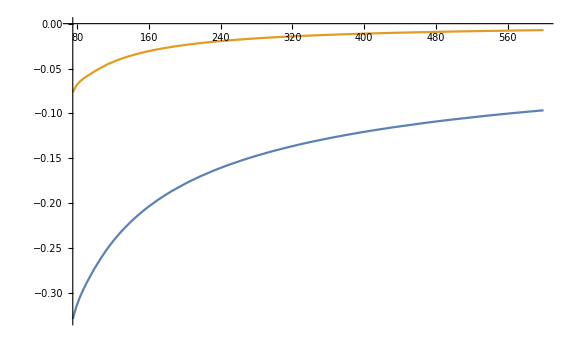

```mathematica
{(*First state*)
Plot[{(ϵ /. FindMinimum [Im[MathieuCharacteristicExponent[ϵ- VV/2,VV/4]],{ϵ,2 √VV(1/2)}][[2]]) - (2 √VV(1/2)-1/4),(ϵ /. FindMinimum [Im[MathieuCharacteristicExponent[ϵ- VV/2,VV/4]],{ϵ,2 √VV(1/2)}][[2]]) - (2 √VV(1/2)-1/4-1/16 1/(√VV))},{VV,40,600}, PlotPoints -> 3, ImageSize -> Large],
(*Second state*)
Plot[{(ϵ /. FindMinimum [Im[MathieuCharacteristicExponent[ϵ- VV/2,VV/4]],{ϵ,2 √VV(1/2+1)}][[2]]) - (2 √VV(1/2+1)-1-1/4),(ϵ /. FindMinimum [Im[MathieuCharacteristicExponent[ϵ- VV/2,VV/4]],{ϵ,2 √VV(1/2+1)}][[2]]) - (2 √VV(1/2+1)-1-1/4-9/16 1/(√VV))},{VV,50,600}, PlotPoints -> 3, ImageSize -> Large],
(*Third state*)
Plot[{(ϵ /. FindMinimum [Im[MathieuCharacteristicExponent[ϵ- VV/2,VV/4]],{ϵ,2 √VV(1/2+2)}][[2]]) - (2 √VV(1/2+2)-3-1/4),(ϵ /. FindMinimum [Im[MathieuCharacteristicExponent[ϵ- VV/2,VV/4]],{ϵ,2 √VV(1/2+2)}][[2]]) - (2 √VV(1/2+2)-3-1/4-35/16 1/(√VV))},{VV,75,600}, PlotPoints -> 3, ImageSize -> Large]
}
```

Now lets explicitly compare the approximation to the real thing for the actual qubit state

```mathematica
{(*First state*)
Plot[{2*(ϵ /. FindMinimum [Im[MathieuCharacteristicExponent[ϵ- VV/2,VV/4]],{ϵ,2 √VV(1/2+1)}][[2]])- ((ϵ /. FindMinimum [Im[MathieuCharacteristicExponent[ϵ- VV/2,VV/4]],{ϵ,2 √VV(1/2)}][[2]]) +(ϵ /. FindMinimum [Im[MathieuCharacteristicExponent[ϵ- VV/2,VV/4]],{ϵ,2 √VV(1/2+2)}][[2]])) ,
1+9/(8 √VV)},{VV,50,600}, PlotPoints -> 3, ImageSize -> Large]
}
```

$Aborted

```mathematica
{(*First state*)
Plot[{2*(ϵ /. FindMinimum [Im[MathieuCharacteristicExponent[ϵ- VV/2,VV/4]],{ϵ,2 √VV(1/2+1)}][[2]])- ((ϵ /. FindMinimum [Im[MathieuCharacteristicExponent[ϵ- VV/2,VV/4]],{ϵ,2 √VV(1/2)}][[2]]) +(ϵ /. FindMinimum [Im[MathieuCharacteristicExponent[ϵ- VV/2,VV/4]],{ϵ,2 √VV(1/2+2)}][[2]])) -1,
1+9/(8 √VV)-1},{VV,100,600}, PlotPoints -> 3, ImageSize -> Large]
}
```

Now let' s quickly estimate whether this makes any sense with our data: 
	First extract the lattice depth in Er units from the measured harmonic frequency and known rough Er depth
		fz = 2 * √(V * Er) where V is in Hz and so is Er, so then

```mathematica
ErTestz = 137;
VVofF[fz_ ,Erz_]:= fz^2/(4 Erz);
VVNormedofF[fz_ ,Erz_]:= fz^2/(4 Erz^2);
Plot[VVNormedofF[fz ,ErTestz], {fz, 25000,52000}];
data= {{25100,140.82},{38500,139}, {52000,137.45}};
guessEr = 137;
plt1 = ListPlot[data, PlotRange -> {Automatic, {135,143}}, PlotLabels -> "Data", PlotStyle -> Red, Mesh -> Full, Joined -> True];
plt2 = Plot[guessEr(1 + 9/8 1/(√VVNormedofF[fz ,guessEr])),{fz,20000,55000}, PlotRange -> {Automatic, {135,143}}, AxesLabel -> {"Z harmonic frequency (Hz)", "Anharmonic energy splitting (Hz)"}, ImageSize -> Large,PlotLabels -> "Theory"];
Show[{plt2,plt1}]
```

-Graphics-

### 1D solution analytic -FAILS

Hamiltonian to solve is 
	H=-1/2((∂_z)^2+(∂_Z)^2) + 1/2 (z^2+Z)^2 + g1D δ(z)
	
We will find unnormalized solutions, so we know what to plot, and go from there. 

Solve relative problem only
Expand in SHO solutions at z=0 and only take the even function
	Ψ = Subscript[∑, n = 0]c_n ϕ^n(0)
	Then plug this into the schrodinger equation.
	
	Project eigenvalue equation onto a specific oscillator state to get
	c_n(E_n-E) + g_(1D)(ϕ^n)^*(0) (∑_m c_m ϕ^m(0))
	
	c_n= A ((ϕ^n)^*(0))/(E_n-E)
	
	And the energy eigenvalue equation is 
	 A ((ϕ^n)^*(0))/(E_n-E)(E_n-E) + g_(1D)(ϕ^n)^*(0) (∑_m A ((ϕ^m)^*(0))/(E_m-E)ϕ^m(0)) or 
	  1+ g_(1D)(∑_m  (|ϕ^m(0)|^2)/(E_m-E)) or ∑_m  (|ϕ^m(0)|^2)/(E_m-E)= -1/(g_(1D))
	
Now all we need to know is the value of the SHO wavefunctions at the origin. That’s relatively simple. 
	-Graphics-
	-Graphics-
	
	-Graphics-

```mathematica
Table[HermiteH[2n,0],{n,0,10}]
Table[(-1)^((2n)/2)((2n)!)/(((2n)/2)!),{n,0,10}]
```

{1,-2,12,-120,1680,-30240,665280,-17297280,518918400,-17643225600,670442572800}

{1,-2,12,-120,1680,-30240,665280,-17297280,518918400,-17643225600,670442572800}

```mathematica
shoEvenStateZeros[n_]:= (-1)^(n/2)((n)!)/((n/2)!)1/(√(2^n n!))1/π^(1/4)
shoStateN[n_,x_] := HermiteH[n,x] 1/(√(2^n n!))1/π^(1/4)ⅇ^(-x^2/2)
FullSimplify[shoEvenStateZeros[n]]
shoStateN[0,0]
shoStateN[2,0]
shoEvenStateZeros[0]
shoEvenStateZeros[2]
(*Formula for zeros seems to work*)
```

((ⅈ/2)^n √(2^n n!))/(π^(1/4) n/2!)

1/π^(1/4)

-1/(√2 π^(1/4))

1/π^(1/4)

-1/(√2 π^(1/4))

```mathematica
(*Now we can get the wavefunction*)
(*We know the normalization because the sum of cn^2 is 1*)
mMax= 10;
sqrtsumOfcnSquaredForNormalization[Eval_] :=  √Sum[(shoEvenStateZeros[2m]/(2m + 1/2 - Eval))^2, {m,0,mMax}]
psi1D[Eval_,x_] := Sum[shoStateN[2m,x] shoEvenStateZeros[2m]/(2m + 1/2 - Eval)1/sqrtsumOfcnSquaredForNormalization[Eval], {m,0,mMax}]
```

```mathematica
N[psi1D[2, 0]]
```

0.370078

```mathematica
Plot[psi1D[-1, x],{x,-4,4}]
```

$Aborted

```mathematica
Table[N[psi1D[2.1, x]], {x,-2,2,0.1}]
```

{-0.436617,-0.489338,-0.538492,-0.580522,-0.612365,-0.631941,-0.638305,-0.631389,-0.611421,-0.578249,-0.530908,-0.467673,-0.386738,-0.287389,-0.17134,-0.0437524,0.086503,0.207613,0.306566,0.371514,0.394158,0.371514,0.306566,0.207613,0.086503,-0.0437524,-0.17134,-0.287389,-0.386738,-0.467673,-0.530908,-0.578249,-0.611421,-0.631389,-0.638305,-0.631941,-0.612365,-0.580522,-0.538492,-0.489338,-0.436617}

```mathematica
NDSolve[{z^2/2-u''[z]/2+0.1 u[0]- Eval u[z] ==0, u[0]==1}, u, {z,0,10}]
```

NDSolve::litarg: To avoid possible ambiguity, the arguments of the dependent variable in {z^2/2+0.1 u[0]-Eval u[z]-u''[z]/2==0} should literally match the independent variables.

NDSolve[{z^2/2+0.1 u[0]-Eval u[z]-u''[z]/2==0,u[0]==1},u,{z,0,10}]

```mathematica
D[u[z],{z,2}]
```

u''[z]

```mathematica
ConfluentHypergeometricFunction
```

```mathematica
FullSimplify[HypergeometricU[x,1,0]]
```

HypergeometricU[x,1,0]

```mathematica
HypergeometricU[a,b,z]
```

-Graphics-
E0 is the energy of the lowest state, so η + 0.5

```mathematica
FullSimplify[k/ηTest- (Eval - (ηTest+1/2))/(2ηTest)]
```

(1-2 Eval+4 k+2 ηTest)/(4 ηTest)

```mathematica
ηTest= 10; 
kMax = 10;
psiZ[Eval_,z_] := (ⅇ^(-z^2/2))/(2 π^(3/2))Sum[(-1)^k/(2^(2k)k!)HermiteH[2k,z]Gamma[k/ηTest- (Eval - (ηTest+1/2))/(2ηTest)]HypergeometricU[k/ηTest- (Eval - (ηTest+1/2))/(2ηTest),1,0], {k,0,kMax}]
psiZ[Eval_,z_] := (ⅇ^(-z^2/2))/(2 π^(3/2))Sum[(-1)^k/(2^(2k)k!)HermiteH[2k,z]Gamma[k/ηTest- (Eval - (ηTest+1/2))/(2ηTest)], {k,0,kMax}]
```

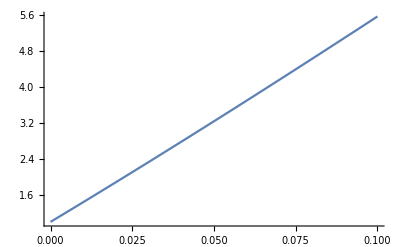

```mathematica
Plot[Abs[HypergeometricU[x,1,0.0000000000000000001]],{x,0.0000000001,0.1}, PlotRange -> All]
```

```mathematica
psiZ[50,0.323423]
```

2.1831

```mathematica
Series[Gamma[x],{x,0,2}]
```

1/x-EulerGamma+1/12 (6 EulerGamma^2+π^2) x+1/6 (-EulerGamma^3-(EulerGamma π^2)/2+PolyGamma[2,1]) x^2+O[x]^3

```mathematica
N[Series[HypergeometricU[x,1,y],{x,0,2}]]
```

1.+HypergeometricU^(1,0,0)[0.,1.,y] (x+0.)+0.5 HypergeometricU^(2,0,0)[0.,1.,y] (x+0.)^2+O[x+0.]^3